# VisibLie_E8 (The Isomorphism of H4 and E8 excerpts)

## A Theory Of Everything Visualizer

By J Gregory Moxness
TheoryOfEverything.orghttps://theoryofeverything.org/theToE/Nonehttps://theoryofeverything.org/theToE/HyperlinkActionNewHyperlinkActive

## Initializations

### General Global Initialization

Standard & Others’ Packages

```mathematica
(* Define conditionally applied doPrint, doQuiet and doOff processing *)
print:=If[doPrint,Print@##]&;

quiet[in_]:=If[doQuiet,Quiet[in],in];
Attributes[quiet]={HoldAll};

off[sym_]:=(
print["doOff=",doOff," off=",sym];
If[doOff,Off@sym]);
```

```mathematica
<< MultivariateStatistics`; 
<< ComputationalGeometry`;
```

```mathematica
(**)
If[doSuperLie,<<Quaternions`];
```

```mathematica
Off[General::munfl];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
(* Tetrahedral Mesh Generator package *)
<<TetGenLink`
```

```mathematica
Off[Set::shape];
```

```mathematica
Off[TetGenConvexHull::tetfc];
```

```mathematica
Off[Volume::nmet];
```

```mathematica
off[Volume::reg];
```

```mathematica
off[RegionCentroid::reg];
```

```mathematica
off[ViewPoint::nlist3];
```

```mathematica
Off[Export::autofix];
```

```mathematica
Off[General::stop];
```

```mathematica
Off[AffineTransform::inpf];
```

```mathematica
Off[BinaryWrite::nocoerce];
```

```mathematica
Off[XMLElement::attrhs];
```

```mathematica
off[HighlightMesh::meshreg];
```

```mathematica
Off[PropertyValue::pvobj];
(**)
```

```mathematica
off[ConvexHullMesh::affind]
```

```mathematica
off[ConvexHullMesh::pts]
```

```mathematica
Off[Show::gtype]
Off[Show::gcomb]
Off[Show::shx]
```

```mathematica
Off[TetGenTetrahedralize::reterr]
```

```mathematica
Off[TetGenDelaunay::tetgpts]
```

This is for either LieART or GroupMath.
Caution : It uses names that can step on my functions unless modified e.g. {An, Bn, Cn, Dn, E(4,5,6,7,8),F4,G2}

```mathematica
(* SuperLie Algebra **)
If[doSuperLie&&working,
off[Solve::svars];
off[ToExpression::sntx]]
(* This is a replacement rule that corrects my code that uses undefined symbols (which SuperLie replaces) *)
slRep:=If[doSuperLie,ToExpression@"{Global`GPlus→Global`Plus$,Global`GTimes→Global`Times$,Global`GPower→Global`Power$,GPlus→Plus$,GTimes→Times$,GPower→Power$}",xxx->1];
```

Off::mgre: Message group Equations may not give solutions for all "solve" variables. was not resolved to a list of messages of the form symbol::name or symbol::name::language.

```mathematica
(* LieART **)
If[doLieART&&working,
<<LieART`];
```

```mathematica
(* GroupTheory **)
If[doGroupTheory&&working,
off[Transpose::nmtx];
<<GroupTheory`];

If[doGroupTheory,
Unprotect[ex,a,b,c,d,F4]];
```

```mathematica
(* GroupMath **)
If[working&&doGroupMath,
(*)Unprotect@C;**)
Unprotect@BlockDiagonalMatrix;
(*)Clear[a,d,f,(* group names *)
e6,e7,e8,so10,so11,so12,so13,so14,so15,so16,so17,so3,so5,so6,so7,so8,so9,su2,su3,su4,su5,su6,su7,su8,u1];**)
<<GroupMath`;(*)
<<Sym2Int`**)];
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

Global

```mathematica
(* Alter the Fano UI based on sedenion selection *)
sedTrk=False;
sedUI:=If[sedTrk,{n1,n2,n3,n4},{n1,n2,n3}];
n1n4UI:={Subscript[ℯ, #]->Style[Subscript[ℯ, #],Darker@Cyan]&/@sedUI};

first=If[Length@#==0||#==={{}},#,First@Flatten@#]&;
position[x_,y_]:=first@Position[x,y,1,Heads->False];
```

```mathematica
(* The symbol φ is the main reference for resolving the Golden Ratios. 
It is only evaluated to a symbolic or numeric value using φRep replacement rules *)
Clear[ϕ,σ,Φ,τ,φ];
(* Upper (and lower) case Phi(Φ=(1+√5)/2) (and phi ϕ=(1-√5)/2)) represent large (and small) Golden Ratio (respectively) *)
ϕ=1/φ;
(* σ & τ are Galois conjugates, this will get stepped on from the CKM UI *)
σ=-1/φ/.slRep;
τ=Φ=φ;

(* 𝕌Det1f is a scale factor to make Det@𝕌=1 *)𝕌Det1f=2 √ϕ /.slRep;
```

```mathematica
(* Create assumptions and replacement rules for φ and ω for automated symbolics *)
φAssumptions:={φ∈Reals,φ^(1/2)∈Reals,φ^(3/2)∈Reals,N[(√5+1)/2]≥φ>N[(√5+1)/2]-chop^2(*),ω∈Complexes**)};
φRep:={φ->(√5+1)/2,ω->ⅇ^(ⅈ 2π/3)};
```

```mathematica
(* GroupMath steps on CircleTimes *)
If[working&&!doGroupMath,
CircleTimes[a_,b_]:=KroneckerProduct[a,b]];

KroneckerSum[a_,b_]/;MatrixQ[a]&&MatrixQ[b]:=Catch@
Module[{n,p,m,q},
{n,p}=Dimensions[a];
{m,q}=Dimensions[b];
If[n≠p||m≠q,Throw[$Failed]];
KroneckerProduct[a,IM@m]+
KroneckerProduct[IM@n,b]];

fb:=Fibonacci;

σP@i_:=PauliMatrix@i;
MatrixForm[σP@#⊗IdentityMatrix@#]&/@Range@3
```

{(0 | 1
1 | 0)⊗(1),(0 | -ⅈ
ⅈ | 0)⊗(1 | 0
0 | 1),(1 | 0
0 | -1)⊗(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

```mathematica
(* Tetration as ^n a := a^(a^(a^(...n))) *)
tetration[a_?NumericQ,0]:=1;
tetration[a_?NumericQ,n_]:=a^(Sign@n tetration[a,n-Sign@n]);
tetration[a_?ListQ,n_]:=MatrixPower[a,n];
MakeExpression[RowBox[{SuperscriptBox["",n_],a_}],StandardForm]:=
MakeExpression[RowBox[{"tetration","[",a,",",n,"]"}],StandardForm];
```

```mathematica
n=4;
Table[^i 2,{i,-n,n}]
```

{2^(-2^(-1/(√2))),2^(-1/(√2)),1/(√2),1/2,1,2,4,16,65536}

```mathematica
(* Fibonacci *)
^6({{1, 1}, {1, 0}})
```

(13 | 8
8 | 5)

```mathematica
Clear[fF,hyperV]
(* Complex Double Factorial *)
fF@k_:=√(2^(k+1)/π)(k/2)!;
```

```mathematica
fF@Range[0,8]
```

{√(2/π),1,2 √(2/π),3,8 √(2/π),15,48 √(2/π),105,384 √(2/π)}

```mathematica
(* HyperDimensional volumes for nSpheres 𝕊^(n-1) *)
hyperV[n_,r_:1]:=(2 (2π)^((n-1)/2))/(fF@n)r^n;
hyperV[#,r]&/@Range@8
```

{2 r,π r^2,(4 π r^3)/3,(π^2 r^4)/2,(8 π^2 r^5)/15,(π^3 r^6)/6,(16 π^3 r^7)/105,(π^4 r^8)/24}

```mathematica
hyperV/@Range@8
```

{2,π,(4 π)/3,π^2/2,(8 π^2)/15,π^3/6,(16 π^3)/105,π^4/24}

```mathematica
fixDo@initGlobal;
```

## Demonstration CodeBase

### Localized Pane Initializations (cloud mode) & UI Logic

Fano

Pane Inits

```mathematica
(* Option to use Mathematica IJK quaternion style for octonions - works with sedenions as well
notice the K=IJ and L prefixes I/J/K on octonions *)
(* Use the integer Subscript[ℯ, 0]=1 last to make Fano plane calculations easier, since they only deal in the imaginary parts *)
octIJKL:=If[sedenions,{I,J,I J,K,I K,J K,I J K,L,I L,J L,I J L,K L,I K L,J K L,I J K L, Subscript[ℯ, 0]},
{I,J,K,L,L I,L J,L K,Subscript[ℯ, 0]}];
oct:=If[sedenions,{Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3],Subscript[ℯ, 4],Subscript[ℯ, 5],Subscript[ℯ, 6],Subscript[ℯ, 7],Subscript[ℯ, 8],Subscript[ℯ, 9],Subscript[ℯ, 10],Subscript[ℯ, 11],Subscript[ℯ, 12],Subscript[ℯ, 13],Subscript[ℯ, 14],Subscript[ℯ, 15],Subscript[ℯ, 0]},
{Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3],Subscript[ℯ, 4],Subscript[ℯ, 5],Subscript[ℯ, 6],Subscript[ℯ, 7],Subscript[ℯ, 0]}];
octN:=RotateRight@oct;
```

```mathematica
(* Octonion math from the matrix using 8D vector representations for x and y, this has the Subscript[ℯ, 0]=1 first *)
octProduct[a_,b_]:=Block[{c3=Array[0&,Length@fm]},
Do[c3⟦If[i≠j,fMult⟦i,j⟧+1,1]⟧+=fSign⟦i,j⟧ a⟦i⟧ b⟦j⟧,
{i,Length@fm},{j,Length@fm}];
Chop@c3]/.slRep;
```

```mathematica
(* Complex, quaternion and octonian multiplication Subscript[ℯ, a]∘Subscript[ℯ, b] *)
quat2Oct@in_:=Block[{(**)a3(**)},
If[nonLocalDeploy,Print@"Quaternions disabled";in,
If[!QuaternionQ@in,Print@"not Quaternion";in,
a3=FromQuaternion@in;
Switch[Length@a3,
(* Length=0 implies Head=Complex and no K element *)
0,Re@a3+Im@a3 Subscript[ℯ, 1],
(* Length=2 and Head=Plus, etc., then convert and return the Complex first part along with the other part already converted *)
2,If[Head@a3===Plus&&Head@a3⟦1⟧===Complex&&Head@a3⟦2⟧===Times/.slRep,
Re@a3⟦1⟧+Im@a3⟦1⟧Subscript[ℯ, 1]+a3⟦2⟧,
(* Length=2 with a non-Plus Head, etc. and non-zero length first part (i.e not complex), 
it may be a Real product so just return the already converted a3 *)
If[Length@a3⟦1⟧>0,a3,
(* otherwise assume it is a sum of a Complex first part and already converted second ?Real? part *)
1∘(Re@a3⟦1⟧+Im@a3⟦1⟧Subscript[ℯ, 1])+a3⟦2⟧]],
(* Length=3 return the Complex first part and other 2 parts already converted *)
3,Re@a3⟦1⟧+Im@a3⟦1⟧Subscript[ℯ, 1]+a3⟦2;;⟧
]/.slRep
]/.
(* This replaces the JKL of Quaternion with the appropriate Subscript[ℯ, n], 
the Imaginary part is problematic so we do that manually *)
Most@Thread[octIJKL->oct]]];
```

```mathematica
(* Convert any list of complex numbers or symbols to a Re@L/Im@R octonion or (Bi)Quaternion list.
Put in⟦;;4⟧ into Re@L/Im@R halves.
BTW - this will also reformat any <8D input to an 8D list *)
biQuaternion@in_List:=FullSimplify[#/.slRep,Assumptions->φAssumptions]&@Join[Re@#,(*)Reverse@**)Im@#]&@(in⟦;;4⟧/.Subscript[ℯ, 1]->ⅈ);
biQuaternion@in_:=biQuaternion@oct2List@in;
```

```mathematica
(* Convert an octonion to a quaternion 4D list *)
oct2Quat@in_:=oct2List[in]⟦;;4⟧;
(* Convert an octonion to an Imaginary quaternion 3D list {Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3]} *)
oct2ImQuat@in_:=oct2List[in]⟦2;;4⟧;
```

```mathematica
(* Octonion math with conversions, leave final as octonion *)
SmallCircle[a_List,b_List]:=octonion@octProduct[a,b];
```

```mathematica
(* Conditionally set Quaternion and Complex to Octonion conversions *)
(* On localized deployments (!nonLocalDeploy) or using splitOctonions as (Bi)Quaternion, we can't/don't use MTM quaternions so we don't do quat2Oct either.
If we want splitOctonions (e.g. (BiQuaternions->L/R Octonions or BiOctonion->L/R Sedenions),
 we exclude ToQuaternion conversion for Complex and Quaternion math.
  We can also convert the complex quaternions to Left/Right octonion halves, and might also want to put complex octonions into sedenions (??) *)
If[!(nonLocalDeploy(*)||splitOctonion**)),
SmallCircle[a_Quaternion,b_Quaternion]:=quat2Oct@a∘quat2Oct@b;
SmallCircle[a_,b_Quaternion]:=a∘quat2Oct@b;
SmallCircle[a_Quaternion,b_]:=quat2Oct@a∘b;
If[!splitOctonion,
SmallCircle[a_Complex,b_Complex]:=ToQuaternion@a∘ToQuaternion@b;
SmallCircle[a_,b_Complex]:=a∘ToQuaternion@b;
SmallCircle[a_Complex,b_]:=ToQuaternion@a∘b]];
```

```mathematica
SmallCircle[a_,b_]:=oct2List@a∘oct2List@b;
(*)SmallCircle[a_,1]:=a;
SmallCircle[1,b_]:=b; **)
```

```mathematica
(* The associator vanishes or =0 where there are non-commuting structure constants f^(A,B,C) =1  *)
associator[a_List,b_List,c_List]:=(a∘b)∘c-a∘(b∘c)/.slRep;
associator[a_,b_,c_]:=associator[oct2List@a,oct2List@b,oct2List@c];
```

```mathematica
(* Jacobi Identity = -associator[a,b,c]3/2 *)
jacobi[a_List,b_List,c_List]:=a∘(b∘c)+b∘(c∘a)+c∘(a∘b)/.slRep;
jacobi[a_,b_,c_]:=jacobi[oct2List@a,oct2List@b,oct2List@c];
```

```mathematica
normedDivisor[a_,b_,c_,d_]:=(a+b)∘(c+d);
```

```mathematica
octConjugate@p_:=Total[oct2List[p/.slRep] octN Diagonal@fSign]/.slRep;
octConjugatePattern:SuperStar[p_]:=octConjugate@p;
```

```mathematica
octConjugateTranspose@p_:=Transpose[SuperStar[p]];
(* Take in a List:
either a symbolic list of octonions or an 8x8 matrix of oct2List octonions,
  and perform an octonionic ConjugateTranspose on it (m^ᵀ)^*=m^† w/†=ConjugateTranspose *)
octConjugateTranspose@p_List:=Transpose[
(* Need to make the input matrix a list if input is a symbolic octonion,
then take the octonion conjugate *)
If[Head@testQuat⟦1⟧===List,SuperStar[p],SuperStar[oct2List[#]]&/@p]];

octConjugateTransposePattern:SuperDagger[p_]:=octConjugateTranspose@p;
```

```mathematica
octRe@p_:=Simplify@Chop@((octonion@p+SuperStar[p])/2)/.slRep;
octIm@p_:=Simplify@Chop@((octonion@p-SuperStar[p])/2)/.slRep;
 
octAbs@p_:=p∘SuperStar[p]/.slRep;
octNorm@p_:=√(octAbs@p)/.slRep;
octInv@p_:=FullSimplify@(SuperStar[p]/(octAbs@p))/.slRep;

scalarProd[x_,y_]:=Simplify@Chop[SuperStar[x]∘y+SuperStar[y]∘x ]/2/.slRep;

scalarProdMinus[x_,y_]:=Simplify@Chop[SuperStar[x]∘y-SuperStar[y]∘x ]/2/.slRep;


CirclePlus[x_,y_]:=scalarProd[x,y]/(octNorm[x] octNorm[y])/.slRep;(**)

CircleMinus[x_,y_]:=scalarProdMinus[x,y]/(octNorm[x] octNorm[y])/.slRep;(**)

commutator[x_,y_]:=Simplify@Chop[x∘y-y∘x]/.slRep ;
CircleDot[x_,y_]:=commutator[x,y]/.slRep;

antiCommutator[x_,y_]:=Simplify@Chop[x∘y+y∘x]/.slRep;
Wedge[x_,y_]:=antiCommutator[x,y];
```

```mathematica
(* This is an alternate form when CircleDot is already used (**)
derivation[x_,y_][a_]:=commutator[commutator[x,y],a]-3associator[x,y,a]/.slRep; 
**)
derivation[x_,y_][a_]:=(x⊙y)⊙a-3associator[x,y,a]/.slRep;
Square[{x_,y_,a_}]:=derivation[x,y][a];

(* Derivation matrix and vector *)
derMatrix[x_,y_]:=Table[Coefficient[□{x,y,oct⟦i⟧},oct⟦j⟧],{j,7},{i,7}]/.slRep;
derMatrix[{x_,y_}]:=derMatrix[x,y];
derVector := Flatten@derMatrix@##&;

(* Define the "checking" function for the derivation D_{x,y} *)
checkD[a_,b_][x_,y_]:=(□{a,b,x∘y}==□{a,b,x}∘y+x∘□{a,b,y});
```

### Non-localized Pane Initializations (working mode)

#### Polytopes and Lie Groups

Define Permutations

```mathematica
(* Functions to generate positional and ± sign permutations of lists *)
EvenPermutationQ@p_:=Signature@p==-1;
OddPermutationQ@p_:=Signature@p==1;

pm@n_:=Flatten[Outer[List,Sequence@@Table[{-1,1},{n}]],n-1];
pm2@n_:=pm@n/2;
```

```mathematica
EvenPermutations@p_List:=Module[{(**)i,j(**)},
i=Range@Length@p;
j=Permutations@i;
(j/.Inner[Rule,i,p,List])⟦Flatten@Position[j,_?EvenPermutationQ,1,Heads->False]⟧];
OddPermutations@p_List:=Module[{(**)i,j(**)},
i=Range@Length@p;
j=Permutations@i;
(j/.Inner[Rule,i,p,List])⟦Flatten@Position[j,_?OddPermutationQ,1,Heads->False]⟧];
```

```mathematica
Eperms@in_List:=EvenPermutations[Inner[Times,in,Array[1&,Length@in],List]];
Operms@in_List:=  OddPermutations[Inner[Times,in,Array[1&,Length@in],List]];
```

```mathematica
(* Quaternion permutations in 3 or 4D 
Code in 14 types of permutations:
"AllNoSign",                 all permutations of position and no ± sign permutations (just like Permutations[]),
  "NoneNoSign",                no permutation of position or sign,
  "None",                      no permutation of position (just ± sign permutations on each position),
  "NoneEsign",                 no permutation of position (just Even ± sign permutations on each position),
  "NoneOsign",                 no permutation of position (just Odd ± sign permutations on each position),
  "All",                       full set of ± sign and positional permutations,
  "Rotate",                    RightRotations of {Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3]} with ± permutations on each position (cyclic with sign),
  "NoSign",                    no sign permutations, just RightRotation of positions            (cyclic only),
  "NoSignEpos" & "NoSignOpos", no sign permutations,  Even (or Odd) positional permutations,
  "Epos"       & "Opos",       full set of ± sign and Even (or Odd) positional permutations,
  "Esign"      & "Osign",      ± sign Permutation by count of Even (or Odd) + signs,
  "EsignEpos"  & "EsignOpos" & "OsignEPos"   & "OsignOPos" 
                             ± sign Permutation by count of Even (or Odd) + signs and Even (or Odd) position permutations *)
permRotate@in_List:=Module[{out=in},
Join[{out},(out=RotateRight@out)&/@Range[Length@in-1]]];

(* Permute in_List with a given permType_String and use select_List to pull out selected indices *)
Clear@perms;
```

```mathematica
perms[in_List,select_List:{},permType_String:"All"]:=Module[{inLength,noSelect, signPerms,permList,outList},
inLength=Length@in;
(* set noSelect if the permType needs all ± permutations *)
noSelect=permType=="Epos"||permType=="Opos"||permType=="Rotate"||permType=="All"||permType=="None";
(* If the permType contains "NoSign", return Array of +1s,
   If the permType doesn't require selecting Even or Odd sign counts, send all signPerms, 
       otherwise do the Select *)
signPerms=If[StringContainsQ[permType,"NoSign"],Array[1&,inLength],
If[noSelect,pm@inLength,
Select[pm@inLength,If[StringContainsQ[permType,"Osign"],OddQ,EvenQ]@Count[Sign@#,1]&]]];
(* Do the position perms *)
permList=Which[
StringTake[permType,3]=="Non",List,
StringContainsQ[permType,"All"]||permType=="Esign"||permType=="Osign",Permutations,
permType=="Rotate"||permType=="NoSign",permRotate,
(* Eperms and Operms processes all positional permutations of Even or Odd Signature (+1,-1) *)
StringContainsQ[permType,"Epos"],Eperms,
StringContainsQ[permType,"Opos"],Operms]@in;
(* Apply the sign perms and delete duplicates, not using Union due to it sorting, which may not be desired *)
outList=DeleteDuplicates@FullSimplify@Flatten[Table[# permList⟦i⟧&/@signPerms,{i,Length@permList}],1];
(* Apply the select list if needed *)
outList⟦If[select=={},Range@Length@outList,select]⟧];

(* This will allow us to process sign permutations of sums of symbolic octonion elements *)
octPerm[in_,select_List:{},permType_String:"All",noUnion_:False]:=
If[noUnion,Flatten,Union]@(octSimplify/@Flatten[Total/@perms[
print["in=",in," nonList Head@in=",Head@in," Length@in=",Length@in];
List@in⟦#⟧&/@Range@Length@in,select,permType]]);

octPerms[in_List,select_List:{},permType_String:"All",noUnion_:False]:=Module[{(*)inP,outP**)},
print["list Head@in=",Head@in," Length@in=",Length@in];
If[noUnion,Flatten,Union]@Flatten[
(* If # is not a sum Total (Head=List) but a single dimension (Subscript[ℯ, 0]=1 w/Head==Integer or Subscript[ℯ, n] with Head==Subscript ), 
just permute it without changing it to a sum Total list of individual octonion dimension elements *)
{print["in⟦#⟧=",in⟦#⟧];
inP=oct2List@in⟦#⟧;
If[Count[inP,0]==7,
print["7 zeros"];
outP=Flatten@perms[{in⟦#⟧},select,permType];
print["outP=",outP];
outP,
outP=octPerm[octonion@inP,select,permType,noUnion];
print["outP=",outP];
outP]
}&/@Range@Length@in]];
```

```mathematica
{#,outp=Union@perms[{x,y,z},(*){1,2},**)#],Length@outp}&/@{"AllNoSign","NoneNoSign","None","NoneEsign","NoneOsign","All","Rotate","NoSign","NoSignEpos","NoSignOpos","Epos","Opos","Esign","Osign","EsignEpos","EsignOpos","OsignEpos","OsignOpos"}//MatrixForm
```

(AllNoSign | (x | y | z
x | z | y
y | x | z
y | z | x
z | x | y
z | y | x) | 6
NoneNoSign | (x | y | z) | 1
None | (-x | -y | -z
-x | -y | z
-x | y | -z
-x | y | z
x | -y | -z
x | -y | z
x | y | -z
x | y | z) | 8
NoneEsign | (-x | -y | -z
-x | y | z
x | -y | z
x | y | -z) | 4
NoneOsign | (-x | -y | z
-x | y | -z
x | -y | -z
x | y | z) | 4
All | (-x | -y | -z
-x | -y | z
-x | y | -z
-x | y | z
-x | -z | -y
-x | -z | y
-x | z | -y
-x | z | y
x | -y | -z
x | -y | z
x | y | -z
x | y | z
x | -z | -y
x | -z | y
x | z | -y
x | z | y
-y | -x | -z
-y | -x | z
-y | x | -z
-y | x | z
-y | -z | -x
-y | -z | x
-y | z | -x
-y | z | x
y | -x | -z
y | -x | z
y | x | -z
y | x | z
y | -z | -x
y | -z | x
y | z | -x
y | z | x
-z | -x | -y
-z | -x | y
-z | x | -y
-z | x | y
-z | -y | -x
-z | -y | x
-z | y | -x
-z | y | x
z | -x | -y
z | -x | y
z | x | -y
z | x | y
z | -y | -x
z | -y | x
z | y | -x
z | y | x) | 48
Rotate | (-x | -y | -z
-x | -y | z
-x | y | -z
-x | y | z
x | -y | -z
x | -y | z
x | y | -z
x | y | z
-y | -z | -x
-y | -z | x
-y | z | -x
-y | z | x
y | -z | -x
y | -z | x
y | z | -x
y | z | x
-z | -x | -y
-z | -x | y
-z | x | -y
-z | x | y
z | -x | -y
z | -x | y
z | x | -y
z | x | y) | 24
NoSign | (x | y | z
y | z | x
z | x | y) | 3
NoSignEpos | (x | z | y
y | x | z
z | y | x) | 3
NoSignOpos | (x | y | z
y | z | x
z | x | y) | 3
Epos | (-x | -z | -y
-x | -z | y
-x | z | -y
-x | z | y
x | -z | -y
x | -z | y
x | z | -y
x | z | y
-y | -x | -z
-y | -x | z
-y | x | -z
-y | x | z
y | -x | -z
y | -x | z
y | x | -z
y | x | z
-z | -y | -x
-z | -y | x
-z | y | -x
-z | y | x
z | -y | -x
z | -y | x
z | y | -x
z | y | x) | 24
Opos | (-x | -y | -z
-x | -y | z
-x | y | -z
-x | y | z
x | -y | -z
x | -y | z
x | y | -z
x | y | z
-y | -z | -x
-y | -z | x
-y | z | -x
-y | z | x
y | -z | -x
y | -z | x
y | z | -x
y | z | x
-z | -x | -y
-z | -x | y
-z | x | -y
-z | x | y
z | -x | -y
z | -x | y
z | x | -y
z | x | y) | 24
Esign | (-x | -y | -z
-x | y | z
-x | -z | -y
-x | z | y
x | -y | z
x | y | -z
x | -z | y
x | z | -y
-y | -x | -z
-y | x | z
-y | -z | -x
-y | z | x
y | -x | z
y | x | -z
y | -z | x
y | z | -x
-z | -x | -y
-z | x | y
-z | -y | -x
-z | y | x
z | -x | y
z | x | -y
z | -y | x
z | y | -x) | 24
Osign | (-x | -y | z
-x | y | -z
-x | -z | y
-x | z | -y
x | -y | -z
x | y | z
x | -z | -y
x | z | y
-y | -x | z
-y | x | -z
-y | -z | x
-y | z | -x
y | -x | -z
y | x | z
y | -z | -x
y | z | x
-z | -x | y
-z | x | -y
-z | -y | x
-z | y | -x
z | -x | -y
z | x | y
z | -y | -x
z | y | x) | 24
EsignEpos | (-x | -z | -y
-x | z | y
x | -z | y
x | z | -y
-y | -x | -z
-y | x | z
y | -x | z
y | x | -z
-z | -y | -x
-z | y | x
z | -y | x
z | y | -x) | 12
EsignOpos | (-x | -y | -z
-x | y | z
x | -y | z
x | y | -z
-y | -z | -x
-y | z | x
y | -z | x
y | z | -x
-z | -x | -y
-z | x | y
z | -x | y
z | x | -y) | 12
OsignEpos | (-x | -z | y
-x | z | -y
x | -z | -y
x | z | y
-y | -x | z
-y | x | -z
y | -x | -z
y | x | z
-z | -y | x
-z | y | -x
z | -y | -x
z | y | x) | 12
OsignOpos | (-x | -y | z
-x | y | -z
x | -y | -z
x | y | z
-y | -z | x
-y | z | -x
y | -z | -x
y | z | x
-z | -x | y
-z | x | -y
z | -x | -y
z | x | y) | 12)

```mathematica
(**)
{#,outp=Union@perms[{x,y,z,w},#],Length@outp}&/@{"AllNoSign","NoneNoSign","None","NoneEsign","NoneOsign","All","Rotate","NoSign","NoSignEpos","NoSignOpos","Epos","Opos","Esign","Osign","EsignEpos","EsignOpos","OsignEpos","OsignOpos"}//MatrixForm
```

(AllNoSign | (w | x | y | z
w | x | z | y
w | y | x | z
w | y | z | x
w | z | x | y
w | z | y | x
x | w | y | z
x | w | z | y
x | y | w | z
x | y | z | w
x | z | w | y
x | z | y | w
y | w | x | z
y | w | z | x
y | x | w | z
y | x | z | w
y | z | w | x
y | z | x | w
z | w | x | y
z | w | y | x
z | x | w | y
z | x | y | w
z | y | w | x
z | y | x | w) | 24
NoneNoSign | (x | y | z | w) | 1
None | (-x | -y | -z | -w
-x | -y | -z | w
-x | -y | z | -w
-x | -y | z | w
-x | y | -z | -w
-x | y | -z | w
-x | y | z | -w
-x | y | z | w
x | -y | -z | -w
x | -y | -z | w
x | -y | z | -w
x | -y | z | w
x | y | -z | -w
x | y | -z | w
x | y | z | -w
x | y | z | w) | 16
NoneEsign | (-x | -y | -z | -w
-x | -y | z | w
-x | y | -z | w
-x | y | z | -w
x | -y | -z | w
x | -y | z | -w
x | y | -z | -w
x | y | z | w) | 8
NoneOsign | (-x | -y | -z | w
-x | -y | z | -w
-x | y | -z | -w
-x | y | z | w
x | -y | -z | -w
x | -y | z | w
x | y | -z | w
x | y | z | -w) | 8
All | (-w | -x | -y | -z
-w | -x | -y | z
-w | -x | y | -z
-w | -x | y | z
-w | -x | -z | -y
-w | -x | -z | y
-w | -x | z | -y
-w | -x | z | y
-w | x | -y | -z
-w | x | -y | z
-w | x | y | -z
-w | x | y | z
-w | x | -z | -y
-w | x | -z | y
-w | x | z | -y
-w | x | z | y
-w | -y | -x | -z
-w | -y | -x | z
-w | -y | x | -z
-w | -y | x | z
-w | -y | -z | -x
-w | -y | -z | x
-w | -y | z | -x
-w | -y | z | x
-w | y | -x | -z
-w | y | -x | z
-w | y | x | -z
-w | y | x | z
-w | y | -z | -x
-w | y | -z | x
-w | y | z | -x
-w | y | z | x
-w | -z | -x | -y
-w | -z | -x | y
-w | -z | x | -y
-w | -z | x | y
-w | -z | -y | -x
-w | -z | -y | x
-w | -z | y | -x
-w | -z | y | x
-w | z | -x | -y
-w | z | -x | y
-w | z | x | -y
-w | z | x | y
-w | z | -y | -x
-w | z | -y | x
-w | z | y | -x
-w | z | y | x
w | -x | -y | -z
w | -x | -y | z
w | -x | y | -z
w | -x | y | z
w | -x | -z | -y
w | -x | -z | y
w | -x | z | -y
w | -x | z | y
w | x | -y | -z
w | x | -y | z
w | x | y | -z
w | x | y | z
w | x | -z | -y
w | x | -z | y
w | x | z | -y
w | x | z | y
w | -y | -x | -z
w | -y | -x | z
w | -y | x | -z
w | -y | x | z
w | -y | -z | -x
w | -y | -z | x
w | -y | z | -x
w | -y | z | x
w | y | -x | -z
w | y | -x | z
w | y | x | -z
w | y | x | z
w | y | -z | -x
w | y | -z | x
w | y | z | -x
w | y | z | x
w | -z | -x | -y
w | -z | -x | y
w | -z | x | -y
w | -z | x | y
w | -z | -y | -x
w | -z | -y | x
w | -z | y | -x
w | -z | y | x
w | z | -x | -y
w | z | -x | y
w | z | x | -y
w | z | x | y
w | z | -y | -x
w | z | -y | x
w | z | y | -x
w | z | y | x
-x | -w | -y | -z
-x | -w | -y | z
-x | -w | y | -z
-x | -w | y | z
-x | -w | -z | -y
-x | -w | -z | y
-x | -w | z | -y
-x | -w | z | y
-x | w | -y | -z
-x | w | -y | z
-x | w | y | -z
-x | w | y | z
-x | w | -z | -y
-x | w | -z | y
-x | w | z | -y
-x | w | z | y
-x | -y | -w | -z
-x | -y | -w | z
-x | -y | w | -z
-x | -y | w | z
-x | -y | -z | -w
-x | -y | -z | w
-x | -y | z | -w
-x | -y | z | w
-x | y | -w | -z
-x | y | -w | z
-x | y | w | -z
-x | y | w | z
-x | y | -z | -w
-x | y | -z | w
-x | y | z | -w
-x | y | z | w
-x | -z | -w | -y
-x | -z | -w | y
-x | -z | w | -y
-x | -z | w | y
-x | -z | -y | -w
-x | -z | -y | w
-x | -z | y | -w
-x | -z | y | w
-x | z | -w | -y
-x | z | -w | y
-x | z | w | -y
-x | z | w | y
-x | z | -y | -w
-x | z | -y | w
-x | z | y | -w
-x | z | y | w
x | -w | -y | -z
x | -w | -y | z
x | -w | y | -z
x | -w | y | z
x | -w | -z | -y
x | -w | -z | y
x | -w | z | -y
x | -w | z | y
x | w | -y | -z
x | w | -y | z
x | w | y | -z
x | w | y | z
x | w | -z | -y
x | w | -z | y
x | w | z | -y
x | w | z | y
x | -y | -w | -z
x | -y | -w | z
x | -y | w | -z
x | -y | w | z
x | -y | -z | -w
x | -y | -z | w
x | -y | z | -w
x | -y | z | w
x | y | -w | -z
x | y | -w | z
x | y | w | -z
x | y | w | z
x | y | -z | -w
x | y | -z | w
x | y | z | -w
x | y | z | w
x | -z | -w | -y
x | -z | -w | y
x | -z | w | -y
x | -z | w | y
x | -z | -y | -w
x | -z | -y | w
x | -z | y | -w
x | -z | y | w
x | z | -w | -y
x | z | -w | y
x | z | w | -y
x | z | w | y
x | z | -y | -w
x | z | -y | w
x | z | y | -w
x | z | y | w
-y | -w | -x | -z
-y | -w | -x | z
-y | -w | x | -z
-y | -w | x | z
-y | -w | -z | -x
-y | -w | -z | x
-y | -w | z | -x
-y | -w | z | x
-y | w | -x | -z
-y | w | -x | z
-y | w | x | -z
-y | w | x | z
-y | w | -z | -x
-y | w | -z | x
-y | w | z | -x
-y | w | z | x
-y | -x | -w | -z
-y | -x | -w | z
-y | -x | w | -z
-y | -x | w | z
-y | -x | -z | -w
-y | -x | -z | w
-y | -x | z | -w
-y | -x | z | w
-y | x | -w | -z
-y | x | -w | z
-y | x | w | -z
-y | x | w | z
-y | x | -z | -w
-y | x | -z | w
-y | x | z | -w
-y | x | z | w
-y | -z | -w | -x
-y | -z | -w | x
-y | -z | w | -x
-y | -z | w | x
-y | -z | -x | -w
-y | -z | -x | w
-y | -z | x | -w
-y | -z | x | w
-y | z | -w | -x
-y | z | -w | x
-y | z | w | -x
-y | z | w | x
-y | z | -x | -w
-y | z | -x | w
-y | z | x | -w
-y | z | x | w
y | -w | -x | -z
y | -w | -x | z
y | -w | x | -z
y | -w | x | z
y | -w | -z | -x
y | -w | -z | x
y | -w | z | -x
y | -w | z | x
y | w | -x | -z
y | w | -x | z
y | w | x | -z
y | w | x | z
y | w | -z | -x
y | w | -z | x
y | w | z | -x
y | w | z | x
y | -x | -w | -z
y | -x | -w | z
y | -x | w | -z
y | -x | w | z
y | -x | -z | -w
y | -x | -z | w
y | -x | z | -w
y | -x | z | w
y | x | -w | -z
y | x | -w | z
y | x | w | -z
y | x | w | z
y | x | -z | -w
y | x | -z | w
y | x | z | -w
y | x | z | w
y | -z | -w | -x
y | -z | -w | x
y | -z | w | -x
y | -z | w | x
y | -z | -x | -w
y | -z | -x | w
y | -z | x | -w
y | -z | x | w
y | z | -w | -x
y | z | -w | x
y | z | w | -x
y | z | w | x
y | z | -x | -w
y | z | -x | w
y | z | x | -w
y | z | x | w
-z | -w | -x | -y
-z | -w | -x | y
-z | -w | x | -y
-z | -w | x | y
-z | -w | -y | -x
-z | -w | -y | x
-z | -w | y | -x
-z | -w | y | x
-z | w | -x | -y
-z | w | -x | y
-z | w | x | -y
-z | w | x | y
-z | w | -y | -x
-z | w | -y | x
-z | w | y | -x
-z | w | y | x
-z | -x | -w | -y
-z | -x | -w | y
-z | -x | w | -y
-z | -x | w | y
-z | -x | -y | -w
-z | -x | -y | w
-z | -x | y | -w
-z | -x | y | w
-z | x | -w | -y
-z | x | -w | y
-z | x | w | -y
-z | x | w | y
-z | x | -y | -w
-z | x | -y | w
-z | x | y | -w
-z | x | y | w
-z | -y | -w | -x
-z | -y | -w | x
-z | -y | w | -x
-z | -y | w | x
-z | -y | -x | -w
-z | -y | -x | w
-z | -y | x | -w
-z | -y | x | w
-z | y | -w | -x
-z | y | -w | x
-z | y | w | -x
-z | y | w | x
-z | y | -x | -w
-z | y | -x | w
-z | y | x | -w
-z | y | x | w
z | -w | -x | -y
z | -w | -x | y
z | -w | x | -y
z | -w | x | y
z | -w | -y | -x
z | -w | -y | x
z | -w | y | -x
z | -w | y | x
z | w | -x | -y
z | w | -x | y
z | w | x | -y
z | w | x | y
z | w | -y | -x
z | w | -y | x
z | w | y | -x
z | w | y | x
z | -x | -w | -y
z | -x | -w | y
z | -x | w | -y
z | -x | w | y
z | -x | -y | -w
z | -x | -y | w
z | -x | y | -w
z | -x | y | w
z | x | -w | -y
z | x | -w | y
z | x | w | -y
z | x | w | y
z | x | -y | -w
z | x | -y | w
z | x | y | -w
z | x | y | w
z | -y | -w | -x
z | -y | -w | x
z | -y | w | -x
z | -y | w | x
z | -y | -x | -w
z | -y | -x | w
z | -y | x | -w
z | -y | x | w
z | y | -w | -x
z | y | -w | x
z | y | w | -x
z | y | w | x
z | y | -x | -w
z | y | -x | w
z | y | x | -w
z | y | x | w) | 384
Rotate | (-w | -x | -y | -z
-w | -x | -y | z
-w | -x | y | -z
-w | -x | y | z
-w | x | -y | -z
-w | x | -y | z
-w | x | y | -z
-w | x | y | z
w | -x | -y | -z
w | -x | -y | z
w | -x | y | -z
w | -x | y | z
w | x | -y | -z
w | x | -y | z
w | x | y | -z
w | x | y | z
-x | -y | -z | -w
-x | -y | -z | w
-x | -y | z | -w
-x | -y | z | w
-x | y | -z | -w
-x | y | -z | w
-x | y | z | -w
-x | y | z | w
x | -y | -z | -w
x | -y | -z | w
x | -y | z | -w
x | -y | z | w
x | y | -z | -w
x | y | -z | w
x | y | z | -w
x | y | z | w
-y | -z | -w | -x
-y | -z | -w | x
-y | -z | w | -x
-y | -z | w | x
-y | z | -w | -x
-y | z | -w | x
-y | z | w | -x
-y | z | w | x
y | -z | -w | -x
y | -z | -w | x
y | -z | w | -x
y | -z | w | x
y | z | -w | -x
y | z | -w | x
y | z | w | -x
y | z | w | x
-z | -w | -x | -y
-z | -w | -x | y
-z | -w | x | -y
-z | -w | x | y
-z | w | -x | -y
-z | w | -x | y
-z | w | x | -y
-z | w | x | y
z | -w | -x | -y
z | -w | -x | y
z | -w | x | -y
z | -w | x | y
z | w | -x | -y
z | w | -x | y
z | w | x | -y
z | w | x | y) | 64
NoSign | (w | x | y | z
x | y | z | w
y | z | w | x
z | w | x | y) | 4
NoSignEpos | (w | x | y | z
w | y | z | x
w | z | x | y
x | w | z | y
x | y | w | z
x | z | y | w
y | w | x | z
y | x | z | w
y | z | w | x
z | w | y | x
z | x | w | y
z | y | x | w) | 12
NoSignOpos | (w | x | z | y
w | y | x | z
w | z | y | x
x | w | y | z
x | y | z | w
x | z | w | y
y | w | z | x
y | x | w | z
y | z | x | w
z | w | x | y
z | x | y | w
z | y | w | x) | 12
Epos | (-w | -x | -y | -z
-w | -x | -y | z
-w | -x | y | -z
-w | -x | y | z
-w | x | -y | -z
-w | x | -y | z
-w | x | y | -z
-w | x | y | z
-w | -y | -z | -x
-w | -y | -z | x
-w | -y | z | -x
-w | -y | z | x
-w | y | -z | -x
-w | y | -z | x
-w | y | z | -x
-w | y | z | x
-w | -z | -x | -y
-w | -z | -x | y
-w | -z | x | -y
-w | -z | x | y
-w | z | -x | -y
-w | z | -x | y
-w | z | x | -y
-w | z | x | y
w | -x | -y | -z
w | -x | -y | z
w | -x | y | -z
w | -x | y | z
w | x | -y | -z
w | x | -y | z
w | x | y | -z
w | x | y | z
w | -y | -z | -x
w | -y | -z | x
w | -y | z | -x
w | -y | z | x
w | y | -z | -x
w | y | -z | x
w | y | z | -x
w | y | z | x
w | -z | -x | -y
w | -z | -x | y
w | -z | x | -y
w | -z | x | y
w | z | -x | -y
w | z | -x | y
w | z | x | -y
w | z | x | y
-x | -w | -z | -y
-x | -w | -z | y
-x | -w | z | -y
-x | -w | z | y
-x | w | -z | -y
-x | w | -z | y
-x | w | z | -y
-x | w | z | y
-x | -y | -w | -z
-x | -y | -w | z
-x | -y | w | -z
-x | -y | w | z
-x | y | -w | -z
-x | y | -w | z
-x | y | w | -z
-x | y | w | z
-x | -z | -y | -w
-x | -z | -y | w
-x | -z | y | -w
-x | -z | y | w
-x | z | -y | -w
-x | z | -y | w
-x | z | y | -w
-x | z | y | w
x | -w | -z | -y
x | -w | -z | y
x | -w | z | -y
x | -w | z | y
x | w | -z | -y
x | w | -z | y
x | w | z | -y
x | w | z | y
x | -y | -w | -z
x | -y | -w | z
x | -y | w | -z
x | -y | w | z
x | y | -w | -z
x | y | -w | z
x | y | w | -z
x | y | w | z
x | -z | -y | -w
x | -z | -y | w
x | -z | y | -w
x | -z | y | w
x | z | -y | -w
x | z | -y | w
x | z | y | -w
x | z | y | w
-y | -w | -x | -z
-y | -w | -x | z
-y | -w | x | -z
-y | -w | x | z
-y | w | -x | -z
-y | w | -x | z
-y | w | x | -z
-y | w | x | z
-y | -x | -z | -w
-y | -x | -z | w
-y | -x | z | -w
-y | -x | z | w
-y | x | -z | -w
-y | x | -z | w
-y | x | z | -w
-y | x | z | w
-y | -z | -w | -x
-y | -z | -w | x
-y | -z | w | -x
-y | -z | w | x
-y | z | -w | -x
-y | z | -w | x
-y | z | w | -x
-y | z | w | x
y | -w | -x | -z
y | -w | -x | z
y | -w | x | -z
y | -w | x | z
y | w | -x | -z
y | w | -x | z
y | w | x | -z
y | w | x | z
y | -x | -z | -w
y | -x | -z | w
y | -x | z | -w
y | -x | z | w
y | x | -z | -w
y | x | -z | w
y | x | z | -w
y | x | z | w
y | -z | -w | -x
y | -z | -w | x
y | -z | w | -x
y | -z | w | x
y | z | -w | -x
y | z | -w | x
y | z | w | -x
y | z | w | x
-z | -w | -y | -x
-z | -w | -y | x
-z | -w | y | -x
-z | -w | y | x
-z | w | -y | -x
-z | w | -y | x
-z | w | y | -x
-z | w | y | x
-z | -x | -w | -y
-z | -x | -w | y
-z | -x | w | -y
-z | -x | w | y
-z | x | -w | -y
-z | x | -w | y
-z | x | w | -y
-z | x | w | y
-z | -y | -x | -w
-z | -y | -x | w
-z | -y | x | -w
-z | -y | x | w
-z | y | -x | -w
-z | y | -x | w
-z | y | x | -w
-z | y | x | w
z | -w | -y | -x
z | -w | -y | x
z | -w | y | -x
z | -w | y | x
z | w | -y | -x
z | w | -y | x
z | w | y | -x
z | w | y | x
z | -x | -w | -y
z | -x | -w | y
z | -x | w | -y
z | -x | w | y
z | x | -w | -y
z | x | -w | y
z | x | w | -y
z | x | w | y
z | -y | -x | -w
z | -y | -x | w
z | -y | x | -w
z | -y | x | w
z | y | -x | -w
z | y | -x | w
z | y | x | -w
z | y | x | w) | 192
Opos | (-w | -x | -z | -y
-w | -x | -z | y
-w | -x | z | -y
-w | -x | z | y
-w | x | -z | -y
-w | x | -z | y
-w | x | z | -y
-w | x | z | y
-w | -y | -x | -z
-w | -y | -x | z
-w | -y | x | -z
-w | -y | x | z
-w | y | -x | -z
-w | y | -x | z
-w | y | x | -z
-w | y | x | z
-w | -z | -y | -x
-w | -z | -y | x
-w | -z | y | -x
-w | -z | y | x
-w | z | -y | -x
-w | z | -y | x
-w | z | y | -x
-w | z | y | x
w | -x | -z | -y
w | -x | -z | y
w | -x | z | -y
w | -x | z | y
w | x | -z | -y
w | x | -z | y
w | x | z | -y
w | x | z | y
w | -y | -x | -z
w | -y | -x | z
w | -y | x | -z
w | -y | x | z
w | y | -x | -z
w | y | -x | z
w | y | x | -z
w | y | x | z
w | -z | -y | -x
w | -z | -y | x
w | -z | y | -x
w | -z | y | x
w | z | -y | -x
w | z | -y | x
w | z | y | -x
w | z | y | x
-x | -w | -y | -z
-x | -w | -y | z
-x | -w | y | -z
-x | -w | y | z
-x | w | -y | -z
-x | w | -y | z
-x | w | y | -z
-x | w | y | z
-x | -y | -z | -w
-x | -y | -z | w
-x | -y | z | -w
-x | -y | z | w
-x | y | -z | -w
-x | y | -z | w
-x | y | z | -w
-x | y | z | w
-x | -z | -w | -y
-x | -z | -w | y
-x | -z | w | -y
-x | -z | w | y
-x | z | -w | -y
-x | z | -w | y
-x | z | w | -y
-x | z | w | y
x | -w | -y | -z
x | -w | -y | z
x | -w | y | -z
x | -w | y | z
x | w | -y | -z
x | w | -y | z
x | w | y | -z
x | w | y | z
x | -y | -z | -w
x | -y | -z | w
x | -y | z | -w
x | -y | z | w
x | y | -z | -w
x | y | -z | w
x | y | z | -w
x | y | z | w
x | -z | -w | -y
x | -z | -w | y
x | -z | w | -y
x | -z | w | y
x | z | -w | -y
x | z | -w | y
x | z | w | -y
x | z | w | y
-y | -w | -z | -x
-y | -w | -z | x
-y | -w | z | -x
-y | -w | z | x
-y | w | -z | -x
-y | w | -z | x
-y | w | z | -x
-y | w | z | x
-y | -x | -w | -z
-y | -x | -w | z
-y | -x | w | -z
-y | -x | w | z
-y | x | -w | -z
-y | x | -w | z
-y | x | w | -z
-y | x | w | z
-y | -z | -x | -w
-y | -z | -x | w
-y | -z | x | -w
-y | -z | x | w
-y | z | -x | -w
-y | z | -x | w
-y | z | x | -w
-y | z | x | w
y | -w | -z | -x
y | -w | -z | x
y | -w | z | -x
y | -w | z | x
y | w | -z | -x
y | w | -z | x
y | w | z | -x
y | w | z | x
y | -x | -w | -z
y | -x | -w | z
y | -x | w | -z
y | -x | w | z
y | x | -w | -z
y | x | -w | z
y | x | w | -z
y | x | w | z
y | -z | -x | -w
y | -z | -x | w
y | -z | x | -w
y | -z | x | w
y | z | -x | -w
y | z | -x | w
y | z | x | -w
y | z | x | w
-z | -w | -x | -y
-z | -w | -x | y
-z | -w | x | -y
-z | -w | x | y
-z | w | -x | -y
-z | w | -x | y
-z | w | x | -y
-z | w | x | y
-z | -x | -y | -w
-z | -x | -y | w
-z | -x | y | -w
-z | -x | y | w
-z | x | -y | -w
-z | x | -y | w
-z | x | y | -w
-z | x | y | w
-z | -y | -w | -x
-z | -y | -w | x
-z | -y | w | -x
-z | -y | w | x
-z | y | -w | -x
-z | y | -w | x
-z | y | w | -x
-z | y | w | x
z | -w | -x | -y
z | -w | -x | y
z | -w | x | -y
z | -w | x | y
z | w | -x | -y
z | w | -x | y
z | w | x | -y
z | w | x | y
z | -x | -y | -w
z | -x | -y | w
z | -x | y | -w
z | -x | y | w
z | x | -y | -w
z | x | -y | w
z | x | y | -w
z | x | y | w
z | -y | -w | -x
z | -y | -w | x
z | -y | w | -x
z | -y | w | x
z | y | -w | -x
z | y | -w | x
z | y | w | -x
z | y | w | x) | 192
Esign | (-w | -x | -y | -z
-w | -x | y | z
-w | -x | -z | -y
-w | -x | z | y
-w | x | -y | z
-w | x | y | -z
-w | x | -z | y
-w | x | z | -y
-w | -y | -x | -z
-w | -y | x | z
-w | -y | -z | -x
-w | -y | z | x
-w | y | -x | z
-w | y | x | -z
-w | y | -z | x
-w | y | z | -x
-w | -z | -x | -y
-w | -z | x | y
-w | -z | -y | -x
-w | -z | y | x
-w | z | -x | y
-w | z | x | -y
-w | z | -y | x
-w | z | y | -x
w | -x | -y | z
w | -x | y | -z
w | -x | -z | y
w | -x | z | -y
w | x | -y | -z
w | x | y | z
w | x | -z | -y
w | x | z | y
w | -y | -x | z
w | -y | x | -z
w | -y | -z | x
w | -y | z | -x
w | y | -x | -z
w | y | x | z
w | y | -z | -x
w | y | z | x
w | -z | -x | y
w | -z | x | -y
w | -z | -y | x
w | -z | y | -x
w | z | -x | -y
w | z | x | y
w | z | -y | -x
w | z | y | x
-x | -w | -y | -z
-x | -w | y | z
-x | -w | -z | -y
-x | -w | z | y
-x | w | -y | z
-x | w | y | -z
-x | w | -z | y
-x | w | z | -y
-x | -y | -w | -z
-x | -y | w | z
-x | -y | -z | -w
-x | -y | z | w
-x | y | -w | z
-x | y | w | -z
-x | y | -z | w
-x | y | z | -w
-x | -z | -w | -y
-x | -z | w | y
-x | -z | -y | -w
-x | -z | y | w
-x | z | -w | y
-x | z | w | -y
-x | z | -y | w
-x | z | y | -w
x | -w | -y | z
x | -w | y | -z
x | -w | -z | y
x | -w | z | -y
x | w | -y | -z
x | w | y | z
x | w | -z | -y
x | w | z | y
x | -y | -w | z
x | -y | w | -z
x | -y | -z | w
x | -y | z | -w
x | y | -w | -z
x | y | w | z
x | y | -z | -w
x | y | z | w
x | -z | -w | y
x | -z | w | -y
x | -z | -y | w
x | -z | y | -w
x | z | -w | -y
x | z | w | y
x | z | -y | -w
x | z | y | w
-y | -w | -x | -z
-y | -w | x | z
-y | -w | -z | -x
-y | -w | z | x
-y | w | -x | z
-y | w | x | -z
-y | w | -z | x
-y | w | z | -x
-y | -x | -w | -z
-y | -x | w | z
-y | -x | -z | -w
-y | -x | z | w
-y | x | -w | z
-y | x | w | -z
-y | x | -z | w
-y | x | z | -w
-y | -z | -w | -x
-y | -z | w | x
-y | -z | -x | -w
-y | -z | x | w
-y | z | -w | x
-y | z | w | -x
-y | z | -x | w
-y | z | x | -w
y | -w | -x | z
y | -w | x | -z
y | -w | -z | x
y | -w | z | -x
y | w | -x | -z
y | w | x | z
y | w | -z | -x
y | w | z | x
y | -x | -w | z
y | -x | w | -z
y | -x | -z | w
y | -x | z | -w
y | x | -w | -z
y | x | w | z
y | x | -z | -w
y | x | z | w
y | -z | -w | x
y | -z | w | -x
y | -z | -x | w
y | -z | x | -w
y | z | -w | -x
y | z | w | x
y | z | -x | -w
y | z | x | w
-z | -w | -x | -y
-z | -w | x | y
-z | -w | -y | -x
-z | -w | y | x
-z | w | -x | y
-z | w | x | -y
-z | w | -y | x
-z | w | y | -x
-z | -x | -w | -y
-z | -x | w | y
-z | -x | -y | -w
-z | -x | y | w
-z | x | -w | y
-z | x | w | -y
-z | x | -y | w
-z | x | y | -w
-z | -y | -w | -x
-z | -y | w | x
-z | -y | -x | -w
-z | -y | x | w
-z | y | -w | x
-z | y | w | -x
-z | y | -x | w
-z | y | x | -w
z | -w | -x | y
z | -w | x | -y
z | -w | -y | x
z | -w | y | -x
z | w | -x | -y
z | w | x | y
z | w | -y | -x
z | w | y | x
z | -x | -w | y
z | -x | w | -y
z | -x | -y | w
z | -x | y | -w
z | x | -w | -y
z | x | w | y
z | x | -y | -w
z | x | y | w
z | -y | -w | x
z | -y | w | -x
z | -y | -x | w
z | -y | x | -w
z | y | -w | -x
z | y | w | x
z | y | -x | -w
z | y | x | w) | 192
Osign | (-w | -x | -y | z
-w | -x | y | -z
-w | -x | -z | y
-w | -x | z | -y
-w | x | -y | -z
-w | x | y | z
-w | x | -z | -y
-w | x | z | y
-w | -y | -x | z
-w | -y | x | -z
-w | -y | -z | x
-w | -y | z | -x
-w | y | -x | -z
-w | y | x | z
-w | y | -z | -x
-w | y | z | x
-w | -z | -x | y
-w | -z | x | -y
-w | -z | -y | x
-w | -z | y | -x
-w | z | -x | -y
-w | z | x | y
-w | z | -y | -x
-w | z | y | x
w | -x | -y | -z
w | -x | y | z
w | -x | -z | -y
w | -x | z | y
w | x | -y | z
w | x | y | -z
w | x | -z | y
w | x | z | -y
w | -y | -x | -z
w | -y | x | z
w | -y | -z | -x
w | -y | z | x
w | y | -x | z
w | y | x | -z
w | y | -z | x
w | y | z | -x
w | -z | -x | -y
w | -z | x | y
w | -z | -y | -x
w | -z | y | x
w | z | -x | y
w | z | x | -y
w | z | -y | x
w | z | y | -x
-x | -w | -y | z
-x | -w | y | -z
-x | -w | -z | y
-x | -w | z | -y
-x | w | -y | -z
-x | w | y | z
-x | w | -z | -y
-x | w | z | y
-x | -y | -w | z
-x | -y | w | -z
-x | -y | -z | w
-x | -y | z | -w
-x | y | -w | -z
-x | y | w | z
-x | y | -z | -w
-x | y | z | w
-x | -z | -w | y
-x | -z | w | -y
-x | -z | -y | w
-x | -z | y | -w
-x | z | -w | -y
-x | z | w | y
-x | z | -y | -w
-x | z | y | w
x | -w | -y | -z
x | -w | y | z
x | -w | -z | -y
x | -w | z | y
x | w | -y | z
x | w | y | -z
x | w | -z | y
x | w | z | -y
x | -y | -w | -z
x | -y | w | z
x | -y | -z | -w
x | -y | z | w
x | y | -w | z
x | y | w | -z
x | y | -z | w
x | y | z | -w
x | -z | -w | -y
x | -z | w | y
x | -z | -y | -w
x | -z | y | w
x | z | -w | y
x | z | w | -y
x | z | -y | w
x | z | y | -w
-y | -w | -x | z
-y | -w | x | -z
-y | -w | -z | x
-y | -w | z | -x
-y | w | -x | -z
-y | w | x | z
-y | w | -z | -x
-y | w | z | x
-y | -x | -w | z
-y | -x | w | -z
-y | -x | -z | w
-y | -x | z | -w
-y | x | -w | -z
-y | x | w | z
-y | x | -z | -w
-y | x | z | w
-y | -z | -w | x
-y | -z | w | -x
-y | -z | -x | w
-y | -z | x | -w
-y | z | -w | -x
-y | z | w | x
-y | z | -x | -w
-y | z | x | w
y | -w | -x | -z
y | -w | x | z
y | -w | -z | -x
y | -w | z | x
y | w | -x | z
y | w | x | -z
y | w | -z | x
y | w | z | -x
y | -x | -w | -z
y | -x | w | z
y | -x | -z | -w
y | -x | z | w
y | x | -w | z
y | x | w | -z
y | x | -z | w
y | x | z | -w
y | -z | -w | -x
y | -z | w | x
y | -z | -x | -w
y | -z | x | w
y | z | -w | x
y | z | w | -x
y | z | -x | w
y | z | x | -w
-z | -w | -x | y
-z | -w | x | -y
-z | -w | -y | x
-z | -w | y | -x
-z | w | -x | -y
-z | w | x | y
-z | w | -y | -x
-z | w | y | x
-z | -x | -w | y
-z | -x | w | -y
-z | -x | -y | w
-z | -x | y | -w
-z | x | -w | -y
-z | x | w | y
-z | x | -y | -w
-z | x | y | w
-z | -y | -w | x
-z | -y | w | -x
-z | -y | -x | w
-z | -y | x | -w
-z | y | -w | -x
-z | y | w | x
-z | y | -x | -w
-z | y | x | w
z | -w | -x | -y
z | -w | x | y
z | -w | -y | -x
z | -w | y | x
z | w | -x | y
z | w | x | -y
z | w | -y | x
z | w | y | -x
z | -x | -w | -y
z | -x | w | y
z | -x | -y | -w
z | -x | y | w
z | x | -w | y
z | x | w | -y
z | x | -y | w
z | x | y | -w
z | -y | -w | -x
z | -y | w | x
z | -y | -x | -w
z | -y | x | w
z | y | -w | x
z | y | w | -x
z | y | -x | w
z | y | x | -w) | 192
EsignEpos | (-w | -x | -y | -z
-w | -x | y | z
-w | x | -y | z
-w | x | y | -z
-w | -y | -z | -x
-w | -y | z | x
-w | y | -z | x
-w | y | z | -x
-w | -z | -x | -y
-w | -z | x | y
-w | z | -x | y
-w | z | x | -y
w | -x | -y | z
w | -x | y | -z
w | x | -y | -z
w | x | y | z
w | -y | -z | x
w | -y | z | -x
w | y | -z | -x
w | y | z | x
w | -z | -x | y
w | -z | x | -y
w | z | -x | -y
w | z | x | y
-x | -w | -z | -y
-x | -w | z | y
-x | w | -z | y
-x | w | z | -y
-x | -y | -w | -z
-x | -y | w | z
-x | y | -w | z
-x | y | w | -z
-x | -z | -y | -w
-x | -z | y | w
-x | z | -y | w
-x | z | y | -w
x | -w | -z | y
x | -w | z | -y
x | w | -z | -y
x | w | z | y
x | -y | -w | z
x | -y | w | -z
x | y | -w | -z
x | y | w | z
x | -z | -y | w
x | -z | y | -w
x | z | -y | -w
x | z | y | w
-y | -w | -x | -z
-y | -w | x | z
-y | w | -x | z
-y | w | x | -z
-y | -x | -z | -w
-y | -x | z | w
-y | x | -z | w
-y | x | z | -w
-y | -z | -w | -x
-y | -z | w | x
-y | z | -w | x
-y | z | w | -x
y | -w | -x | z
y | -w | x | -z
y | w | -x | -z
y | w | x | z
y | -x | -z | w
y | -x | z | -w
y | x | -z | -w
y | x | z | w
y | -z | -w | x
y | -z | w | -x
y | z | -w | -x
y | z | w | x
-z | -w | -y | -x
-z | -w | y | x
-z | w | -y | x
-z | w | y | -x
-z | -x | -w | -y
-z | -x | w | y
-z | x | -w | y
-z | x | w | -y
-z | -y | -x | -w
-z | -y | x | w
-z | y | -x | w
-z | y | x | -w
z | -w | -y | x
z | -w | y | -x
z | w | -y | -x
z | w | y | x
z | -x | -w | y
z | -x | w | -y
z | x | -w | -y
z | x | w | y
z | -y | -x | w
z | -y | x | -w
z | y | -x | -w
z | y | x | w) | 96
EsignOpos | (-w | -x | -z | -y
-w | -x | z | y
-w | x | -z | y
-w | x | z | -y
-w | -y | -x | -z
-w | -y | x | z
-w | y | -x | z
-w | y | x | -z
-w | -z | -y | -x
-w | -z | y | x
-w | z | -y | x
-w | z | y | -x
w | -x | -z | y
w | -x | z | -y
w | x | -z | -y
w | x | z | y
w | -y | -x | z
w | -y | x | -z
w | y | -x | -z
w | y | x | z
w | -z | -y | x
w | -z | y | -x
w | z | -y | -x
w | z | y | x
-x | -w | -y | -z
-x | -w | y | z
-x | w | -y | z
-x | w | y | -z
-x | -y | -z | -w
-x | -y | z | w
-x | y | -z | w
-x | y | z | -w
-x | -z | -w | -y
-x | -z | w | y
-x | z | -w | y
-x | z | w | -y
x | -w | -y | z
x | -w | y | -z
x | w | -y | -z
x | w | y | z
x | -y | -z | w
x | -y | z | -w
x | y | -z | -w
x | y | z | w
x | -z | -w | y
x | -z | w | -y
x | z | -w | -y
x | z | w | y
-y | -w | -z | -x
-y | -w | z | x
-y | w | -z | x
-y | w | z | -x
-y | -x | -w | -z
-y | -x | w | z
-y | x | -w | z
-y | x | w | -z
-y | -z | -x | -w
-y | -z | x | w
-y | z | -x | w
-y | z | x | -w
y | -w | -z | x
y | -w | z | -x
y | w | -z | -x
y | w | z | x
y | -x | -w | z
y | -x | w | -z
y | x | -w | -z
y | x | w | z
y | -z | -x | w
y | -z | x | -w
y | z | -x | -w
y | z | x | w
-z | -w | -x | -y
-z | -w | x | y
-z | w | -x | y
-z | w | x | -y
-z | -x | -y | -w
-z | -x | y | w
-z | x | -y | w
-z | x | y | -w
-z | -y | -w | -x
-z | -y | w | x
-z | y | -w | x
-z | y | w | -x
z | -w | -x | y
z | -w | x | -y
z | w | -x | -y
z | w | x | y
z | -x | -y | w
z | -x | y | -w
z | x | -y | -w
z | x | y | w
z | -y | -w | x
z | -y | w | -x
z | y | -w | -x
z | y | w | x) | 96
OsignEpos | (-w | -x | -y | z
-w | -x | y | -z
-w | x | -y | -z
-w | x | y | z
-w | -y | -z | x
-w | -y | z | -x
-w | y | -z | -x
-w | y | z | x
-w | -z | -x | y
-w | -z | x | -y
-w | z | -x | -y
-w | z | x | y
w | -x | -y | -z
w | -x | y | z
w | x | -y | z
w | x | y | -z
w | -y | -z | -x
w | -y | z | x
w | y | -z | x
w | y | z | -x
w | -z | -x | -y
w | -z | x | y
w | z | -x | y
w | z | x | -y
-x | -w | -z | y
-x | -w | z | -y
-x | w | -z | -y
-x | w | z | y
-x | -y | -w | z
-x | -y | w | -z
-x | y | -w | -z
-x | y | w | z
-x | -z | -y | w
-x | -z | y | -w
-x | z | -y | -w
-x | z | y | w
x | -w | -z | -y
x | -w | z | y
x | w | -z | y
x | w | z | -y
x | -y | -w | -z
x | -y | w | z
x | y | -w | z
x | y | w | -z
x | -z | -y | -w
x | -z | y | w
x | z | -y | w
x | z | y | -w
-y | -w | -x | z
-y | -w | x | -z
-y | w | -x | -z
-y | w | x | z
-y | -x | -z | w
-y | -x | z | -w
-y | x | -z | -w
-y | x | z | w
-y | -z | -w | x
-y | -z | w | -x
-y | z | -w | -x
-y | z | w | x
y | -w | -x | -z
y | -w | x | z
y | w | -x | z
y | w | x | -z
y | -x | -z | -w
y | -x | z | w
y | x | -z | w
y | x | z | -w
y | -z | -w | -x
y | -z | w | x
y | z | -w | x
y | z | w | -x
-z | -w | -y | x
-z | -w | y | -x
-z | w | -y | -x
-z | w | y | x
-z | -x | -w | y
-z | -x | w | -y
-z | x | -w | -y
-z | x | w | y
-z | -y | -x | w
-z | -y | x | -w
-z | y | -x | -w
-z | y | x | w
z | -w | -y | -x
z | -w | y | x
z | w | -y | x
z | w | y | -x
z | -x | -w | -y
z | -x | w | y
z | x | -w | y
z | x | w | -y
z | -y | -x | -w
z | -y | x | w
z | y | -x | w
z | y | x | -w) | 96
OsignOpos | (-w | -x | -z | y
-w | -x | z | -y
-w | x | -z | -y
-w | x | z | y
-w | -y | -x | z
-w | -y | x | -z
-w | y | -x | -z
-w | y | x | z
-w | -z | -y | x
-w | -z | y | -x
-w | z | -y | -x
-w | z | y | x
w | -x | -z | -y
w | -x | z | y
w | x | -z | y
w | x | z | -y
w | -y | -x | -z
w | -y | x | z
w | y | -x | z
w | y | x | -z
w | -z | -y | -x
w | -z | y | x
w | z | -y | x
w | z | y | -x
-x | -w | -y | z
-x | -w | y | -z
-x | w | -y | -z
-x | w | y | z
-x | -y | -z | w
-x | -y | z | -w
-x | y | -z | -w
-x | y | z | w
-x | -z | -w | y
-x | -z | w | -y
-x | z | -w | -y
-x | z | w | y
x | -w | -y | -z
x | -w | y | z
x | w | -y | z
x | w | y | -z
x | -y | -z | -w
x | -y | z | w
x | y | -z | w
x | y | z | -w
x | -z | -w | -y
x | -z | w | y
x | z | -w | y
x | z | w | -y
-y | -w | -z | x
-y | -w | z | -x
-y | w | -z | -x
-y | w | z | x
-y | -x | -w | z
-y | -x | w | -z
-y | x | -w | -z
-y | x | w | z
-y | -z | -x | w
-y | -z | x | -w
-y | z | -x | -w
-y | z | x | w
y | -w | -z | -x
y | -w | z | x
y | w | -z | x
y | w | z | -x
y | -x | -w | -z
y | -x | w | z
y | x | -w | z
y | x | w | -z
y | -z | -x | -w
y | -z | x | w
y | z | -x | w
y | z | x | -w
-z | -w | -x | y
-z | -w | x | -y
-z | w | -x | -y
-z | w | x | y
-z | -x | -y | w
-z | -x | y | -w
-z | x | -y | -w
-z | x | y | w
-z | -y | -w | x
-z | -y | w | -x
-z | y | -w | -x
-z | y | w | x
z | -w | -x | -y
z | -w | x | y
z | w | -x | y
z | w | x | -y
z | -x | -y | -w
z | -x | y | w
z | x | -y | w
z | x | y | -w
z | -y | -w | -x
z | -y | w | x
z | y | -w | x
z | y | w | -x) | 96)

```mathematica
ds=3;
dims=8;
dp={{-1,-1},{1,-1},{1,1}};
dn@n_:=Join[#,Array[0&,dims-n]]&/@Sort@Flatten[Permutations@Join[#,Array[0&,n-2]]&/@dp,1];

nOrtho@n_:=Join[#,Array[0&,dims-n]]&/@Sort@Flatten[Permutations@Join[{#},Array[0&,n-1]]&/@dp⟦2⟧,1];
```

Cell600

```mathematica
(* Other than Cell600, these group names get over-written later when finding them inside E8 *)
d4=dn[4]⟦All,;;4⟧
Length@%
```

(-1 | -1 | 0 | 0
-1 | 0 | -1 | 0
-1 | 0 | 0 | -1
-1 | 0 | 0 | 1
-1 | 0 | 1 | 0
-1 | 1 | 0 | 0
0 | -1 | -1 | 0
0 | -1 | 0 | -1
0 | -1 | 0 | 1
0 | -1 | 1 | 0
0 | 0 | -1 | -1
0 | 0 | -1 | 1
0 | 0 | 1 | -1
0 | 0 | 1 | 1
0 | 1 | -1 | 0
0 | 1 | 0 | -1
0 | 1 | 0 | 1
0 | 1 | 1 | 0
1 | -1 | 0 | 0
1 | 0 | -1 | 0
1 | 0 | 0 | -1
1 | 0 | 0 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0)

24

```mathematica
d4=Sort@perms[{1,1,0,0},"Epos"]
Length@%
```

(-1 | -1 | 0 | 0
-1 | 0 | -1 | 0
-1 | 0 | 0 | -1
-1 | 0 | 0 | 1
-1 | 0 | 1 | 0
-1 | 1 | 0 | 0
0 | -1 | -1 | 0
0 | -1 | 0 | -1
0 | -1 | 0 | 1
0 | -1 | 1 | 0
0 | 0 | -1 | -1
0 | 0 | -1 | 1
0 | 0 | 1 | -1
0 | 0 | 1 | 1
0 | 1 | -1 | 0
0 | 1 | 0 | -1
0 | 1 | 0 | 1
0 | 1 | 1 | 0
1 | -1 | 0 | 0
1 | 0 | -1 | 0
1 | 0 | 0 | -1
1 | 0 | 0 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0)

24

```mathematica
tesseract=pm2@4
Length@%
```

(-1/2 | -1/2 | -1/2 | -1/2
-1/2 | -1/2 | -1/2 | 1/2
-1/2 | -1/2 | 1/2 | -1/2
-1/2 | -1/2 | 1/2 | 1/2
-1/2 | 1/2 | -1/2 | -1/2
-1/2 | 1/2 | -1/2 | 1/2
-1/2 | 1/2 | 1/2 | -1/2
-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2)

16

```mathematica
cell16=nOrtho[4]⟦All,;;4⟧
Length@%
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

8

```mathematica
cell24=tesseract∪cell16
Length@%
```

(-1 | 0 | 0 | 0
-1/2 | -1/2 | -1/2 | -1/2
-1/2 | -1/2 | -1/2 | 1/2
-1/2 | -1/2 | 1/2 | -1/2
-1/2 | -1/2 | 1/2 | 1/2
-1/2 | 1/2 | -1/2 | -1/2
-1/2 | 1/2 | -1/2 | 1/2
-1/2 | 1/2 | 1/2 | -1/2
-1/2 | 1/2 | 1/2 | 1/2
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1/2 | -1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2
1 | 0 | 0 | 0)

24

```mathematica
(* Use this for Transpose non-symmetric QC CNOT/CSWAP generated 𝕌 **)
seqSnub=If[nonTranspose𝕌,{0,Φ,1,ϕ},{0,ϕ,1,Φ}];
```

```mathematica
snub24cell=FullSimplify@perms[seqSnub,"Epos"]
```

(0 | -1/φ | -φ | -1
0 | -1/φ | -φ | 1
0 | -1/φ | φ | -1
0 | -1/φ | φ | 1
0 | 1/φ | -φ | -1
0 | 1/φ | -φ | 1
0 | 1/φ | φ | -1
0 | 1/φ | φ | 1
0 | -1 | -1/φ | -φ
0 | -1 | -1/φ | φ
0 | -1 | 1/φ | -φ
0 | -1 | 1/φ | φ
0 | 1 | -1/φ | -φ
0 | 1 | -1/φ | φ
0 | 1 | 1/φ | -φ
0 | 1 | 1/φ | φ
0 | -φ | -1 | -1/φ
0 | -φ | -1 | 1/φ
0 | -φ | 1 | -1/φ
0 | -φ | 1 | 1/φ
0 | φ | -1 | -1/φ
0 | φ | -1 | 1/φ
0 | φ | 1 | -1/φ
0 | φ | 1 | 1/φ
-1/φ | 0 | -1 | -φ
-1/φ | 0 | -1 | φ
-1/φ | 0 | 1 | -φ
-1/φ | 0 | 1 | φ
1/φ | 0 | -1 | -φ
1/φ | 0 | -1 | φ
1/φ | 0 | 1 | -φ
1/φ | 0 | 1 | φ
-1/φ | -1 | -φ | 0
-1/φ | -1 | φ | 0
-1/φ | 1 | -φ | 0
-1/φ | 1 | φ | 0
1/φ | -1 | -φ | 0
1/φ | -1 | φ | 0
1/φ | 1 | -φ | 0
1/φ | 1 | φ | 0
-1/φ | -φ | 0 | -1
-1/φ | -φ | 0 | 1
-1/φ | φ | 0 | -1
-1/φ | φ | 0 | 1
1/φ | -φ | 0 | -1
1/φ | -φ | 0 | 1
1/φ | φ | 0 | -1
1/φ | φ | 0 | 1
-1 | 0 | -φ | -1/φ
-1 | 0 | -φ | 1/φ
-1 | 0 | φ | -1/φ
-1 | 0 | φ | 1/φ
1 | 0 | -φ | -1/φ
1 | 0 | -φ | 1/φ
1 | 0 | φ | -1/φ
1 | 0 | φ | 1/φ
-1 | -1/φ | 0 | -φ
-1 | -1/φ | 0 | φ
-1 | 1/φ | 0 | -φ
-1 | 1/φ | 0 | φ
1 | -1/φ | 0 | -φ
1 | -1/φ | 0 | φ
1 | 1/φ | 0 | -φ
1 | 1/φ | 0 | φ
-1 | -φ | -1/φ | 0
-1 | -φ | 1/φ | 0
-1 | φ | -1/φ | 0
-1 | φ | 1/φ | 0
1 | -φ | -1/φ | 0
1 | -φ | 1/φ | 0
1 | φ | -1/φ | 0
1 | φ | 1/φ | 0
-φ | 0 | -1/φ | -1
-φ | 0 | -1/φ | 1
-φ | 0 | 1/φ | -1
-φ | 0 | 1/φ | 1
φ | 0 | -1/φ | -1
φ | 0 | -1/φ | 1
φ | 0 | 1/φ | -1
φ | 0 | 1/φ | 1
-φ | -1/φ | -1 | 0
-φ | -1/φ | 1 | 0
-φ | 1/φ | -1 | 0
-φ | 1/φ | 1 | 0
φ | -1/φ | -1 | 0
φ | -1/φ | 1 | 0
φ | 1/φ | -1 | 0
φ | 1/φ | 1 | 0
-φ | -1 | 0 | -1/φ
-φ | -1 | 0 | 1/φ
-φ | 1 | 0 | -1/φ
-φ | 1 | 0 | 1/φ
φ | -1 | 0 | -1/φ
φ | -1 | 0 | 1/φ
φ | 1 | 0 | -1/φ
φ | 1 | 0 | 1/φ)

```mathematica
Cell600=(2 cell24)∪snub24cell;
Length@%
```

120

```mathematica
snub24cellRev=DeleteDuplicates@FullSimplify@perms[Reverse@seqSnub,"Epos"];
Length@%
```

96

```mathematica
Cell600Rev=(2 cell24)∪snub24cellRev;
```

```mathematica
snub24cellMix=perms[{Φ,ϕ,1,0},"Epos"];
Length@%
```

96

```mathematica
Cell600Mix=(2 cell24)∪snub24cellMix;
```

Cell120

```mathematica
(* Cell120 is accessed via the VisibLie-E8 menu and selects the dynkin diagram for the H4, which uses feedList to get the cooordinates. *)
(* Re-sort 120-cell (J) values into partititioned JΦ generated via quaternion/octonion math based on Koca's work **)
cell120base=DeleteDuplicates@Join[
2 dn[4]⟦All,;;4⟧,
Flatten[perms[#,"Epos"]&/@{{√5,ϕ,Φ,0},{√5,1,1,1},{Φ,Φ,Φ,ϕ^2},{Φ^2,ϕ,ϕ,ϕ},{Φ^2,ϕ^2,1,0},{2,1,Φ,ϕ}}/.slRep,1]]/.slRep;

Cell120=cell120base;
Cell120N=#/.φRep&/@%;
Cell120NRnd=rndOct/@(biQuaternion/@%/√8);
Cell120NRndQuat=oct2Quat/@%;
```

E8 to H4 Folding Matrix

```mathematica
(* Build the E8 to H4 (600 Cell) folding matrix from 2-Qubit QC operators and the Golden Ratio *)
(*)Clear[Φ,ϕ]**)
```

```mathematica
(* CNOT and SWAP are Unitary Hermitian Matrices
Also defined below in QC module *)
CNOT:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
CNOT==Transpose[CNOT]
CNOT.Transpose[CNOT]
```

True

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SWAP:=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
SWAP==Transpose[SWAP]
SWAP.Transpose[SWAP]
```

True

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Adding factor ⅈ to CNOT gives complex 𝕌, not Hermitian (**)
(SWAP+# (*)ⅈ**) CNOT)&/@{-ϕ,ϕ }/.φRuleList;
E82H4=Flatten/@Transpose@Join[
{Flatten[%,1]},
{Flatten[Reverse@%,1]}]**)
(* This is the Hermitian form (#9) *)
Transpose@Join[SWAP-ϕ CNOT,Reverse[SWAP+ϕ CNOT]]/.slRep
```

(1-1/φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/φ+1
0 | -1/φ | 1 | 0 | 0 | 1 | 1/φ | 0
0 | 1 | 0 | -1/φ | 1/φ | 0 | 1 | 0
0 | 0 | -1/φ | 1 | 1 | 1/φ | 0 | 0)

```mathematica
𝕌Base=Join[%,Reverse[Reverse/@%]]
%/.φRep//MatrixForm;
N@%//MatrixForm
```

(1-1/φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/φ+1
0 | -1/φ | 1 | 0 | 0 | 1 | 1/φ | 0
0 | 1 | 0 | -1/φ | 1/φ | 0 | 1 | 0
0 | 0 | -1/φ | 1 | 1 | 1/φ | 0 | 0
0 | 0 | 1/φ | 1 | 1 | -1/φ | 0 | 0
0 | 1 | 0 | 1/φ | -1/φ | 0 | 1 | 0
0 | 1/φ | 1 | 0 | 0 | 1 | -1/φ | 0
1/φ+1 | 0 | 0 | 0 | 0 | 0 | 0 | 1-1/φ)

(0.381966 | 0. | 0. | 0. | 0. | 0. | 0. | 1.61803
0. | -0.618034 | 1. | 0. | 0. | 1. | 0.618034 | 0.
0. | 1. | 0. | -0.618034 | 0.618034 | 0. | 1. | 0.
0. | 0. | -0.618034 | 1. | 1. | 0.618034 | 0. | 0.
0. | 0. | 0.618034 | 1. | 1. | -0.618034 | 0. | 0.
0. | 1. | 0. | 0.618034 | -0.618034 | 0. | 1. | 0.
0. | 0.618034 | 1. | 0. | 0. | 1. | -0.618034 | 0.
1.61803 | 0. | 0. | 0. | 0. | 0. | 0. | 0.381966)

```mathematica
E82H4=𝕌Base/𝕌Det1f/.slRep;
%//MatrixForm
%/.φRep//MatrixForm;
N@%//MatrixForm
```

((1-1/φ)/(2 √(1/φ)) | 0 | 0 | 0 | 0 | 0 | 0 | (1/φ+1)/(2 √(1/φ))
0 | -(√(1/φ))/2 | 1/(2 √(1/φ)) | 0 | 0 | 1/(2 √(1/φ)) | (√(1/φ))/2 | 0
0 | 1/(2 √(1/φ)) | 0 | -(√(1/φ))/2 | (√(1/φ))/2 | 0 | 1/(2 √(1/φ)) | 0
0 | 0 | -(√(1/φ))/2 | 1/(2 √(1/φ)) | 1/(2 √(1/φ)) | (√(1/φ))/2 | 0 | 0
0 | 0 | (√(1/φ))/2 | 1/(2 √(1/φ)) | 1/(2 √(1/φ)) | -(√(1/φ))/2 | 0 | 0
0 | 1/(2 √(1/φ)) | 0 | (√(1/φ))/2 | -(√(1/φ))/2 | 0 | 1/(2 √(1/φ)) | 0
0 | (√(1/φ))/2 | 1/(2 √(1/φ)) | 0 | 0 | 1/(2 √(1/φ)) | -(√(1/φ))/2 | 0
(1/φ+1)/(2 √(1/φ)) | 0 | 0 | 0 | 0 | 0 | 0 | (1-1/φ)/(2 √(1/φ)))

(0.242934 | 0. | 0. | 0. | 0. | 0. | 0. | 1.02909
0. | -0.393076 | 0.63601 | 0. | 0. | 0.63601 | 0.393076 | 0.
0. | 0.63601 | 0. | -0.393076 | 0.393076 | 0. | 0.63601 | 0.
0. | 0. | -0.393076 | 0.63601 | 0.63601 | 0.393076 | 0. | 0.
0. | 0. | 0.393076 | 0.63601 | 0.63601 | -0.393076 | 0. | 0.
0. | 0.63601 | 0. | 0.393076 | -0.393076 | 0. | 0.63601 | 0.
0. | 0.393076 | 0.63601 | 0. | 0. | 0.63601 | -0.393076 | 0.
1.02909 | 0. | 0. | 0. | 0. | 0. | 0. | 0.242934)

```mathematica
(* Redefining from the Localized Manipulate (above) 
Here are a few different forms for using the E8↔H4 (un)folding matrix 𝕌, 
which is now selectable and set from curr𝕌 **)
ⅇⅈ𝕌:=FullSimplify@MatrixExp[ⅈ E82H4];
ⅇⅈ𝕌Inv:=Inverse@ⅇⅈ𝕌;
ⅇⅈ𝕌Rev:=Reverse/@ⅇⅈ𝕌
ⅇⅈ𝕌InvRev:=Inverse@ⅇⅈ𝕌Rev;

𝕌:=If[doUnitary,ⅇⅈ𝕌,E82H4];
𝕌Inv:=Rationalize@Inverse@𝕌;
𝕌Rev:=Reverse/@𝕌;
𝕌InvRev:=Inverse@𝕌Rev;
```

𝕌  variations

𝕌 as a Rotational Matrix (Det=1) and/or a Parity Inversion Matrix (Det=-1)
     after applying 𝕌Det1f:=2 √ϕ  scaling factor)

```mathematica
{"Det=",Det[N[#/.φRep]],"EigenSystem=",evals=Eigenvalues@#,MatrixForm[evecs=Eigenvectors@#],Row@{"Tr=",Tr@#,"=",Chop@N[Tr@#/.φRep]}(*),"Diag=",MatrixForm@DiagonalMatrix@Eigenvalues@#,DiagonalMatrix@Eigenvalues@#==FullSimplify[Inverse[evecs^ᵀ].#.evecs^ᵀ]/.φRuleList**)}&/@
(* RotateLeft four times. This swaps L⟷R swapping H4⟷H4Φ vertex numbers (**)
RotateLeft/@(RotateLeft/@(RotateLeft/@(RotateLeft/@#)))**)#(**)&@
({({{1-ϕ, 0, 0, 0, 1+ϕ, 0, 0, 0}, {0, -ϕ, 1, 0, 0, ϕ, 1, 0}, {0, 1, 0, -ϕ, 0, 1, 0, ϕ}, {0, 0, -ϕ, 1, 0, 0, ϕ, 1}, {1+ϕ, 0, 0, 0, 1-ϕ, 0, 0, 0}, {0, ϕ, 1, 0, 0, -ϕ, 1, 0}, {0, 1, 0, ϕ, 0, 1, 0, -ϕ}, {0, 0, ϕ, 1, 0, 0, -ϕ, 1}})(* 𝕌, Det=1 Rotation, Tr=0.971 **),
,,,,,,,
({{ϕ-1, 0, 0, 0, -ϕ-1, 0, 0, 0}, {0, -ϕ, 1, 0, 0, ϕ, 1, 0}, {0, 1, 0, -ϕ, 0, 1, 0, ϕ}, {0, 0, -ϕ, 1, 0, 0, ϕ, 1}, {-ϕ-1, 0, 0, 0, ϕ-1, 0, 0, 0}, {0, ϕ, 1, 0, 0, -ϕ, 1, 0}, {0, 1, 0, ϕ, 0, 1, 0, -ϕ}, {0, 0, ϕ, 1, 0, 0, -ϕ, 1}})(* 𝕌 with negated 1's & ϕ's on upper left corners of each quadrant, Det=1 Rotation, Tr=0 *),
,
({{-1+ϕ, 0, 0, 0, 0, 0, 0, -1-ϕ}, {0, 0, 1, -ϕ, ϕ, 1, 0, 0}, {0, 1, -ϕ, 0, 0, ϕ, 1, 0}, {0, -ϕ, 0, 1, 1, 0, ϕ, 0}, {0, ϕ, 0, 1, 1, 0, -ϕ, 0}, {0, 1, ϕ, 0, 0, -ϕ, 1, 0}, {0, 0, 1, ϕ, -ϕ, 1, 0, 0}, {-1-ϕ, 0, 0, 0, 0, 0, 0, -1+ϕ}})(* Same as above w/row/column 2⟷3, attempt to fix E8⟷H4 0⟷1 on H4-D4 octahedrons in dims 2⟷3 **)
}/𝕌Det1f/.slRep)//MatrixForm
```

(Det= | 1. | EigenSystem= | {-√(1/φ),-√(1/φ),-√(1/φ),√(1/φ),-1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ))} | (0 | 0 | -1 | -1 | 0 | 0 | 1 | 1
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0
-1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | -1 | 1
0 | -1 | 1 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | Tr=(1-1/φ)/(√(1/φ))-√(1/φ)+1/(√(1/φ))=0.971737
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | 1. | EigenSystem= | {-√(1/φ),-√(1/φ),√(1/φ),√(1/φ),-1/(√(1/φ)),-1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ))} | (0 | 0 | -1 | -1 | 0 | 0 | 1 | 1
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | -1 | 1
-1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | -1 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0) | Tr=(1/φ-1)/(√(1/φ))-√(1/φ)+1/(√(1/φ))=0
Det= | Det[0.63601 Null] | EigenSystem= | Eigenvalues[Null/(2 √(1/φ))] | Eigenvectors[Null/(2 √(1/φ))] | Tr=Tr[Null/(2 √(1/φ))]=Tr[0.63601 Null]
Det= | 1. | EigenSystem= | {-√(1/φ),-√(1/φ),√(1/φ),√(1/φ),-1/(√(1/φ)),-1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ))} | (0 | -1 | 0 | -1 | 1 | 0 | 1 | 0
0 | 0 | -1 | 0 | 0 | 1 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1 | 0 | 1 | -1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | -1 | 0 | 0 | -1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0) | Tr=(1/φ-1)/(√(1/φ))-√(1/φ)+1/(√(1/φ))=0)

rot𝕌 = 𝕌, Det=1 Rotation, Tr=0.971

```mathematica
(* Show 𝕌 as a construction with the Eigenvectors *)
rot𝕌=({{1-ϕ, 0, 0, 0, 1+ϕ, 0, 0, 0}, {0, -ϕ, 1, 0, 0, ϕ, 1, 0}, {0, 1, 0, -ϕ, 0, 1, 0, ϕ}, {0, 0, -ϕ, 1, 0, 0, ϕ, 1}, {1+ϕ, 0, 0, 0, 1-ϕ, 0, 0, 0}, {0, ϕ, 1, 0, 0, -ϕ, 1, 0}, {0, 1, 0, ϕ, 0, 1, 0, -ϕ}, {0, 0, ϕ, 1, 0, 0, -ϕ, 1}})/𝕌Det1f /.slRep;
diagParityInv𝕌Neg1notUL=(
evecs=Eigenvectors@rot𝕌;
Inverse[Transpose[evecs]].rot𝕌.Transpose[evecs]);
(* Show the Diagonals list and matrix *)
diagListrot𝕌=Diagonal@rot𝕌
N[%/.φRep]
DiagonalMatrix@%%//MatrixForm
(* Show the Trace *)
FullSimplify[Tr@%]==2 ϕ^(3/2)
N[%/.φRep]
rot𝕌evals=Eigenvalues@%%%%%%
N[%/.φRep]
```

{(1-1/φ)/(2 √(1/φ)),-(√(1/φ))/2,0,1/(2 √(1/φ)),(1-1/φ)/(2 √(1/φ)),-(√(1/φ))/2,0,1/(2 √(1/φ))}

{0.242934,-0.393076,0.,0.63601,0.242934,-0.393076,0.,0.63601}

((1-1/φ)/(2 √(1/φ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(√(1/φ))/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √(1/φ)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-1/φ)/(2 √(1/φ)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(√(1/φ))/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √(1/φ)))

2 (φ-1) √(1/φ)==2 (1/φ)^(3/2)

True

{-√(1/φ),-√(1/φ),-√(1/φ),√(1/φ),-1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ))}

{-0.786151,-0.786151,-0.786151,0.786151,-1.27202,1.27202,1.27202,1.27202}

rot𝕌Neg1ϕULRevR=𝕌 with negated 1’s & ϕ's in upper left corners and L=-Reverse@R on Quadrants, Det=1 Rotation, Tr=0
The Inverse is created by swapping all ϕ⟷1

```mathematica
(* 𝕌 with ALL negated 1's and ϕ's giving Det=1 Rotation *)
rot𝕌Neg1ϕULRevR=({{ϕ-1, 0, 0, 0, 0, 0, 0, -ϕ-1}, {0, -ϕ, 1, 0, 0, 1, ϕ, 0}, {0, 1, 0, -ϕ, ϕ, 0, 1, 0}, {0, 0, -ϕ, 1, 1, ϕ, 0, 0}, {0, 0, ϕ, 1, 1, -ϕ, 0, 0}, {0, 1, 0, ϕ, -ϕ, 0, 1, 0}, {0, ϕ, 1, 0, 0, 1, -ϕ, 0}, {-ϕ-1, 0, 0, 0, 0, 0, 0, ϕ-1}})/𝕌Det1f /.slRep;
diagrot𝕌Neg1ϕULRevR=(
evecs=Eigenvectors@rot𝕌NegϕAll;
Inverse[Transpose[evecs]].rot𝕌Neg1ϕULRevR.Transpose[evecs]);
diagListrot𝕌Neg1ϕULRevR=Diagonal@rot𝕌Neg1ϕULRevR
(* Show the Diagonals list and matrix *)
N[%/.φRep]
𝕌Det1f %/.φRep
DiagonalMatrix@%%//MatrixForm
(* Show the Trace *)
Chop@FullSimplify[Tr@%]
N[%/.φRep]
Eigenvalues@%%%%%%%%
N[%/.φRep]
𝕌Det1f/2 %/.φRep
(* Show how the Eigenvalues relate to the normal 𝕌 Eigenvalues *)
rot𝕌evals==%%%{1,-1,1,1,1,1,-1,1}
```

{(1/φ-1)/(2 √(1/φ)),-(√(1/φ))/2,0,1/(2 √(1/φ)),1/(2 √(1/φ)),0,-(√(1/φ))/2,(1/φ-1)/(2 √(1/φ))}

{-0.242934,-0.393076,0.,0.63601,0.63601,0.,-0.393076,-0.242934}

{-0.381966,-0.618034,0.,1.,1.,0.,-0.618034,-0.381966}

(-0.242934 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.393076 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.63601 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.63601 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.393076 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.242934)

0

0.

{-√(1/φ),-√(1/φ),√(1/φ),√(1/φ),-1/(√(1/φ)),-1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ))}

{-0.786151,-0.786151,0.786151,0.786151,-1.27202,-1.27202,1.27202,1.27202}

{-0.618034,-0.618034,0.618034,0.618034,-1.,-1.,1.,1.}

{-√(1/φ),-√(1/φ),-√(1/φ),√(1/φ),-1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ)),1/(√(1/φ))}=={-√(1/φ),√(1/φ),√(1/φ),√(1/φ),-1/(√(1/φ)),-1/(√(1/φ)),-1/(√(1/φ)),1/(√(1/φ))}

set 𝕌 stuff

```mathematica
𝕌List=octSym@#&/@{rot𝕌,
,,,,,,,
rot𝕌Neg1ϕULRevR,
,
𝕌Base
}/.slRep;
```

```mathematica
(* We use 11 to identify the unscaled palindromic 𝕌Base *)
curr𝕌=11;(**)
E82H4=𝕌List⟦curr𝕌⟧(*)/.φRep**);
Row@{%/.slRep}
```

(1/φ^2 | 0. | 0. | 0. | 0. | 0. | 0. | φ
0. | -1/φ | 1 | 0. | 0. | 1 | 1/φ | 0.
0. | 1 | 0. | -1/φ | 1/φ | 0. | 1 | 0.
0. | 0. | -1/φ | 1 | 1 | 1/φ | 0. | 0.
0. | 0. | 1/φ | 1 | 1 | -1/φ | 0. | 0.
0. | 1 | 0. | 1/φ | -1/φ | 0. | 1 | 0.
0. | 1/φ | 1 | 0. | 0. | 1 | -1/φ | 0.
φ | 0. | 0. | 0. | 0. | 0. | 0. | 1/φ^2)

```mathematica
(* We use 1 to identify the old non-Traceless quadrant form of 𝕌Det1f scaled 𝕌 *)
curr𝕌=1;
E82H4=𝕌List⟦curr𝕌⟧(*)/.φRep**);
Row@{octSym[𝕌Det1f %/.slRep],"/𝕌Det1f"}
```

(1/φ^2 | 0. | 0. | 0. | φ | 0. | 0. | 0.
0. | -1/φ | 1 | 0. | 0. | 1/φ | 1 | 0.
0. | 1 | 0. | -1/φ | 0. | 1 | 0. | 1/φ
0. | 0. | -1/φ | 1 | 0. | 0. | 1/φ | 1
φ | 0. | 0. | 0. | 1/φ^2 | 0. | 0. | 0.
0. | 1/φ | 1 | 0. | 0. | -1/φ | 1 | 0.
0. | 1 | 0. | 1/φ | 0. | 1 | 0. | -1/φ
0. | 0. | 1/φ | 1 | 0. | 0. | -1/φ | 1)/𝕌Det1f

```mathematica
(* Show the Eigensystem  *)
Eigenvalues@𝕌
N[%/.φRep]
```

{-1/(√φ),-1/(√φ),1/(√φ),-√φ,√φ,√φ,(1-φ^3)/(2 φ^(3/2)),(φ^3+1)/(2 φ^(3/2))}

{-0.786151,-0.786151,0.786151,-1.27202,1.27202,1.27202,-0.786151,1.27202}

```mathematica
Eigenvectors@𝕌
```

(0 | 0 | -1 | -1 | 0 | 0 | 1 | 1
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | -1 | 1
0 | -1 | 1 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
-1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
(* We use 9 to identify the new Determinant=1 Traceless palindromic form of 𝕌Det1f scaled 𝕌 *)
curr𝕌=9;(**)
E82H4=𝕌List⟦curr𝕌⟧(*)/.φRep**)
Row@{octSym[𝕌Det1f%/.slRep],"/𝕌Det1f"}
{Det@#,N[Det@#/.φRep],Chop@Tr@#,Chop@N[Chop@Tr@#/.φRep]}&@%%/.φRep//MatrixForm
```

(-1/(2 φ^(3/2)) | 0. | 0. | 0. | 0. | 0. | 0. | -φ^(3/2)/2
0. | -1/(2 √φ) | (√φ)/2 | 0. | 0. | (√φ)/2 | 1/(2 √φ) | 0.
0. | (√φ)/2 | 0. | -1/(2 √φ) | 1/(2 √φ) | 0. | (√φ)/2 | 0.
0. | 0. | -1/(2 √φ) | (√φ)/2 | (√φ)/2 | 1/(2 √φ) | 0. | 0.
0. | 0. | 1/(2 √φ) | (√φ)/2 | (√φ)/2 | -1/(2 √φ) | 0. | 0.
0. | (√φ)/2 | 0. | 1/(2 √φ) | -1/(2 √φ) | 0. | (√φ)/2 | 0.
0. | 1/(2 √φ) | (√φ)/2 | 0. | 0. | (√φ)/2 | -1/(2 √φ) | 0.
-φ^(3/2)/2 | 0. | 0. | 0. | 0. | 0. | 0. | -1/(2 φ^(3/2)))

(-1/φ^2 | 0. | 0. | 0. | 0. | 0. | 0. | -φ
0. | -1/φ | 1 | 0. | 0. | 1 | 1/φ | 0.
0. | 1 | 0. | -1/φ | 1/φ | 0. | 1 | 0.
0. | 0. | -1/φ | 1 | 1 | 1/φ | 0. | 0.
0. | 0. | 1/φ | 1 | 1 | -1/φ | 0. | 0.
0. | 1 | 0. | 1/φ | -1/φ | 0. | 1 | 0.
0. | 1/φ | 1 | 0. | 0. | 1 | -1/φ | 0.
-φ | 0. | 0. | 0. | 0. | 0. | 0. | -1/φ^2)/𝕌Det1f

((1/8 (1+√5)^9-8 (1+√5)^3)/(4 (1+√5)^6)
1.
-√(2/(1+√5))+√(1/2 (1+√5))-(2 √2)/(1+√5)^(3/2)
0)

```mathematica
(* Show the Eigensystem  *)
Eigenvalues@𝕌
N[%/.φRep]
```

{-1/(√φ),-1/(√φ),1/(√φ),-√φ,√φ,√φ,(-φ^3-1)/(2 φ^(3/2)),(φ^3-1)/(2 φ^(3/2))}

{-0.786151,-0.786151,0.786151,-1.27202,1.27202,1.27202,-1.27202,0.786151}

```mathematica
Eigenvectors@𝕌
```

(0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | -1 | 1 | 1 | 0 | 0
0 | 0 | -1 | 1 | -1 | 1 | 0 | 0
0 | 1 | -1 | 0 | 0 | -1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Set and unset doUnitary flag, which changes E82H4 to the unitary form of 𝕌=ⅇ^ⅈ𝕌 in order to show its EigenSystem *)
doUnitarySave=doUnitary;
doUnitary=True;
```

```mathematica
(* Show the Eigensystem  *)
Eigenvalues@𝕌
RotateRight@FullSimplify[%/.φRep,Assumptions->φAssumptions]//MatrixForm
octSym@N@%
```

{ⅇ^(-1/2 ⅈ φ^(3/2)-ⅈ/(2 φ^(3/2))),ⅇ^(1/2 ⅈ φ^(3/2)-ⅈ/(2 φ^(3/2))),1/2 ⅇ^(-3/2 ⅈ φ^(3/2)-(3 ⅈ)/(2 φ^(3/2))) (2 ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) cos(1/(√φ))-2 ⅈ ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) sin(1/(√φ))),1/2 ⅇ^(-3/2 ⅈ φ^(3/2)-(3 ⅈ)/(2 φ^(3/2))) (2 ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) cos(1/(√φ))-2 ⅈ ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) sin(1/(√φ))),1/2 ⅇ^(-3/2 ⅈ φ^(3/2)-(3 ⅈ)/(2 φ^(3/2))) (2 ⅈ ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) sin(1/(√φ))+2 ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) cos(1/(√φ))),1/2 ⅇ^(-3/2 ⅈ φ^(3/2)-(3 ⅈ)/(2 φ^(3/2))) (2 ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) cos(√φ)-2 ⅈ ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) sin(√φ)),1/2 ⅇ^(-3/2 ⅈ φ^(3/2)-(3 ⅈ)/(2 φ^(3/2))) (2 ⅈ ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) sin(√φ)+2 ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) cos(√φ)),1/2 ⅇ^(-3/2 ⅈ φ^(3/2)-(3 ⅈ)/(2 φ^(3/2))) (2 ⅈ ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) sin(√φ)+2 ⅇ^(3/2 ⅈ φ^(3/2)+(3 ⅈ)/(2 φ^(3/2))) cos(√φ))}

(exp(Root1.27 ⅈRoot[#1^4+#1^2-1&,4]0.)
exp(Root-1.27 ⅈRoot[#1^4+#1^2-1&,3]0.)
exp(Root0.786 ⅈRoot[#1^4-#1^2-1&,4]0.)
exp(Root-0.786 ⅈRoot[#1^4-#1^2-1&,3]0.)
exp(Root-0.786 ⅈRoot[#1^4-#1^2-1&,3]0.)
exp(Root0.786 ⅈRoot[#1^4-#1^2-1&,4]0.)
exp(Root-1.27 ⅈRoot[#1^4+#1^2-1&,3]0.)
exp(Root1.27 ⅈRoot[#1^4+#1^2-1&,4]0.))

{ⅇ^(ⅈ √φ),ⅇ^(-ⅈ √φ),ⅇ^(ⅈ/(√φ)),ⅇ^(-ⅈ/(√φ)),ⅇ^(-ⅈ/(√φ)),ⅇ^(ⅈ/(√φ)),ⅇ^(-ⅈ √φ),ⅇ^(ⅈ √φ)}

```mathematica
Eigenvectors@𝕌
FullSimplify[%/.φRep,Assumptions->φAssumptions]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | -1 | 1 | 1 | 0 | 0
0 | 0 | -1 | 1 | -1 | 1 | 0 | 0
0 | 1 | -1 | 0 | 0 | -1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
0 | -(sin(√φ) csc(1/(√φ)) (-2 ⅈ ⅇ^(ⅈ √φ) sin^2(1/(√φ)) csc^2(√φ)-2 sin^2(1/(√φ)) csc(√φ)+2 ⅈ sin^2(1/(√φ)) cot(√φ) csc(√φ)))/(ⅈ ⅇ^(ⅈ √φ)-ⅈ cos(1/(√φ))+ⅇ^(ⅈ √φ) cot(√φ)+cos^2(1/(√φ)) csc(√φ)-cos(1/(√φ)) cot(√φ)-ⅇ^(ⅈ √φ) cos(1/(√φ)) csc(√φ)+sin^2(1/(√φ)) csc(√φ)) | -(2 ⅈ ⅇ^(ⅈ √φ) csc(1/(√φ))-2 ⅈ cos(√φ) csc(1/(√φ))+2 sin(√φ) csc(1/(√φ)))/(-cot^2(1/(√φ))-ⅇ^(ⅈ √φ) cos(√φ) csc^2(1/(√φ))+ⅇ^(ⅈ √φ) cot(1/(√φ)) csc(1/(√φ))-ⅈ ⅇ^(ⅈ √φ) sin(√φ) csc^2(1/(√φ))+cos(√φ) cot(1/(√φ)) csc(1/(√φ))+ⅈ sin(√φ) cot(1/(√φ)) csc(1/(√φ))-1) | -(sin^2(1/(√φ))-2 sin^2(√φ)-ⅈ ⅇ^(ⅈ √φ) sin(√φ)+cos^2(1/(√φ))+2 cos^2(√φ)+ⅇ^(ⅈ √φ) cos(1/(√φ))-3 cos(√φ) cos(1/(√φ))-ⅇ^(ⅈ √φ) cos(√φ)-3 ⅈ sin(√φ) cos(1/(√φ))+4 ⅈ sin(√φ) cos(√φ))/(-sin^2(1/(√φ))-ⅈ ⅇ^(ⅈ √φ) sin(√φ)-cos^2(1/(√φ))+ⅇ^(ⅈ √φ) cos(1/(√φ))+cos(√φ) cos(1/(√φ))-ⅇ^(ⅈ √φ) cos(√φ)+ⅈ sin(√φ) cos(1/(√φ))) | 1 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | -1 | 1 | 1 | 0 | 0
0 | 0 | -1 | 1 | -1 | 1 | 0 | 0
0 | 1 | -1 | 0 | 0 | -1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0)

```mathematica
doUnitary=doUnitarySave;
```

```mathematica
(* RotateLeft four times. This swaps L⟷R swapping H4⟷H4Φ vertex numbers (**)
E82H4=RotateLeft/@(RotateLeft/@(RotateLeft/@(RotateLeft/@𝕌)));**)
```

#### E8 based definitions

Define up to 16 orbit perms & their names (perms1D, 2D, 3D, and 4D, plus perms8D)

```mathematica
(* The 15 binary orbit permutations using only {0,1}'s *)
perms8D=Permutations@Range@8;
```

```mathematica
perms1D={1,0};
perms1DNames={
(* 1 ringed *)
"Parent",
(* No ringed *)
"Snub"};
```

```mathematica
perms2D={{1,0},{0,1}{1,1},{0,0}};
perms2DNames=Flatten@Join[{perms1DNames⟦;;1⟧},#&/@{
(* 1 ringed *)
"Rectified",
(* All ringed *)
"OmniTruncated"},{perms1DNames⟦-1;;⟧}]
```

{Parent,Rectified,OmniTruncated,Snub}

```mathematica
perms3D=Flatten[Permutations/@{{1,0,0},{1,1,0},{1,1,1},{0,0,0}},1]
perms3DNames=Flatten@Join[{perms2DNames⟦;;2⟧},#&/@{
(* 1 ringed *)
"BiRectified",
(* 2 ringed *)
"Truncated",
"Cantellated",
"Runcinated"},{perms2DNames⟦-2;;⟧}]
Length@%%
Length@%%
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
1 | 1 | 0
1 | 0 | 1
0 | 1 | 1
1 | 1 | 1
0 | 0 | 0)

{Parent,Rectified,BiRectified,Truncated,Cantellated,Runcinated,OmniTruncated,Snub}

8

8

```mathematica
perms4D=Flatten[Permutations/@{{1,0,0,0},{1,1,0,0},{1,1,1,0},{1,1,1,1},{0,0,0,0}},1]
perms4DNames=Flatten@Join[{perms3DNames⟦;;3⟧},#&/@{
(* 1 ringed *)
"TriRectified",
(* 2 ringed *)
"Truncated",
"Cantellated",
"Runcinated",
"BiTruncated",
"BiCantellated",
"TriTruncated",
(* 3 ringed *)
"CantiTruncated",
"RunciTruncated",
"BiCantiTruncated",
"CantiRuncinated"
},{perms3DNames⟦-2;;⟧}]
Length@%%
Length@%%
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 1 | 0 | 0
1 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1
1 | 1 | 1 | 0
1 | 1 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 1 | 1
1 | 1 | 1 | 1
0 | 0 | 0 | 0)

{Parent,Rectified,BiRectified,TriRectified,Truncated,Cantellated,Runcinated,BiTruncated,BiCantellated,TriTruncated,CantiTruncated,RunciTruncated,BiCantiTruncated,CantiRuncinated,OmniTruncated,Snub}

16

16

Binary Pascal Triangle / Clifford Algebra list and E8 Lie Algebra list

```mathematica
(* Split Real Even *)
binList=(*)ToPackedArray@**)Join[
e8b1={zeros},                                                               (*  1 Fermion-Subscript[ν, e]_(R^⋁) (1st gen,no charge or color *)
e8b2=Permutations@{1,0,0,0,0,0,0,0},(*  8 Bosons-Ex (1's represent individual binary dims) *)
e8b3=Permutations@{1,1,0,0,0,0,0,0},(* 28 Fermions=even (0,1)'s (2/6) *)
e8b4=Permutations@{1,1,1,0,0,0,0,0},(* 56 Bosons=odd(0,1)'s (5/3) (w/32 (half) 2nd gen fermions) *)
e8b5=Permutations@{1,1,1,1,0,0,0,0},(* 70 Fermions=even (0,1)'s (4/4) (w/35 anti particles) *)
e8b6=Permutations@{1,1,1,1,1,0,0,0},(* 56 Bosons-anti of (0,1)'s (5/3)(w/32 (half) 2nd gen fermions) *)
e8b7=Permutations@{1,1,1,1,1,1,0,0},(* 28 Fermions-anti of (0,1)'s (6/2) *)
e8b8=Permutations@{1,1,1,1,1,1,1,0},(*  8 Bosons-OverBar[Ex] or {0,0,0,0,0,0,0,-1} *)
e8b9={zeros+1}                                                             (* 1 Fermion-Subscript[ν̄, e] *)];
```

```mathematica
permPset=Array[0&,9];

fermion1=e8b1-1/2;(* 0/8 binary inverse=anti *)
permPset⟦1⟧=Length@fermion1;
fermion3=e8b3-1/2;(* 2/6 binary inverse=anti *)
permPset⟦3⟧=Length@fermion3;
fermion5=e8b5-1/2;(* 4/4 binary (even fermion w/±1/2's)-contains 35 anti's *)
permPset⟦5⟧=Length@fermion5;
fermion7=e8b7-1/2;(* 6/2 binary (even fermion w/±1/2's) *)
permPset⟦7⟧=Length@fermion7;
fermion9=e8b9-1/2;(* 8/0 binary (even fermion w/±1/2's) *)
permPset⟦9⟧=Length@fermion9;

perm62m=Permutations@{0,0,0,0,0,0,-1,-1}; (* 2/6 binary anti (reversed) *)
perm26=e8b3; (* 2/6 binary (even fermion w/1,0's) *)
perm18m=Permutations@{1,0,0,0,0,0,0,-1};(* 6/2 3 valued 28-28anti (reversed) *)
perm18ma=perm18m⟦;;Length@perm18m/2⟧;
perm18mb=perm18m⟦Length@perm18m/2+1;;⟧;

boson4=perm62m∪perm18mb;
permPset⟦4⟧=Length@boson4;
boson6=perm18ma∪perm26;
permPset⟦6⟧=Length@boson6;

exception2=e8b8-1;
permPset⟦2⟧=Length@exception2;
exception8=e8b2;
permPset⟦8⟧=Length@exception8;

e8List=(*)ToPackedArray@**)Join[
fermion1,                          (*  1= 1      *)
exception2,                     (*  8= 2- 9   *)
fermion3,                          (* 28= 10- 37 *)
boson4,                              (* 56= 38- 93 *)
fermion5,                          (* 70= 94-163 *)
boson6,                              (* 56=164-219 *)
fermion7,                          (* 28=220-247 *)
exception8,                     (*  8=248-255 *)
fermion9                              (*  1=    256 *)];

pE8@p_:=e8List⟦pMin@p⟧;
pAnti@p_:=position[e8List,-pE8@p];
```

Lie Algebra Simple Roots, Cartan matrix and Cell 600 H4 list

```mathematica
srE8Base=srE8=({{1, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -1, 0, 0, 0}, {0, 0, 1, -1, 0, 0, 0, 0}, {0, 1, -1, 0, 0, 0, 0, 0}, {-1/2, -1/2, -1/2, -1/2, -1/2, -1/2, -1/2, -1/2}, {0, 0, 0, 0, 0, 1, 1, 0}, {0, 0, 0, 0, 1, -1, 0, 0}, {0, 0, 0, 0, 0, 1, -1, 0}})//StandardForm;
```

```mathematica
srE8mix:=If[palindromicE8,
(* Best for (de)constructiong groups using srE8 off the ends (aka. palindromic construction, 
keeping the Left/Right Tr@Im[ⅇⅈ𝕌.%.ⅇⅈ𝕌Inv]==0  *)
perms8D⟦20428⟧,
(* WP page example #1575 *)
{1,4,3,2,7,6,5,8}]
```

```mathematica
srE8:=srE8Base⟦srE8mix⟧;
srE8
```

(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
-1/2 | -1/2 | -1/2 | -1/2 | -1/2 | -1/2 | -1/2 | -1/2
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0)

```mathematica
srEn:=srE8⟦9-#;;,9-#;;⟧&;

(* Cartan matrix 
srE8=√cmE8 *)
cmE8:=srE8.srE8ᵀ;

pRoot@p_:=Inverse@srE8ᵀ.pE8@p;
pWeight@p_:=cmE8.pRoot@p;
pHeight@p_:=Abs@Total@pRoot@p;
```

```mathematica
If[palindromicE8,
(* palindromicE8 *)
(* Direct from srE8 *)
srD7=srE8⟦2;;,;;7⟧;
(* Modified to D8 *)
srD8=ReplacePart[RotateRight/@srE8,1->{1,-1,0,0,0,0,0,0}];
srDn:=srD8⟦9-#;;,9-#;;⟧&;
srDn/@Range[3,8];

CMDn:=srDn@#.Transpose@srDn@#&;
CMDn/@Range[3,8];
(* B/C2 - B/C8 from E8->D8 *)
(* Direct from srE8 *)
srB7=ReplacePart[srE8⟦2;;,;;7⟧,{{7,6}->0}];

(* Modified from D8 *)
srB8=ReplacePart[srD8,{{8,7}->0}];
srBn:=srB8⟦9-#;;,9-#;;⟧&;
srBn/@Range[2,8];

CMBn:=ReplacePart[srBn@#.Transpose@srBn@#,{{#-1,#}->-2,{#,#}->2}]&;
CMBn/@Range[2,8];

(* Direct from srE8->B7 *)
srC7=ReplacePart[srB7,{{7,7}->2}];
(* Modified from E8->D8->B8->C8 *)
srC8=ReplacePart[srB8,{{8,8}->2}];
srCn:=srC8⟦9-#;;,9-#;;⟧&;
srCn/@Range[2,8];

CMCn:=ReplacePart[srCn@#.Transpose@srCn@#,{{#-1,#}->-1,{#,#}->2}]&;
CMCn/@Range[2,8];

(* A2 - A8 from E8->D8->B8 *)
srA8=srB8;
srAn=srBn;
srAn/@Range[2,8];

CMAn:=ReplacePart[srAn@#.Transpose@srAn@#,{#,#}->2]&;
CMAn/@Range[2,8];

(* G2 & F4 *)
(* WP - maybe wrong *)
srF4=ReplacePart[srE8⟦;;4,;;4⟧,{4,4}->0];
(* Better and consistent with GroupMath & LieART *)
srF4=ReplacePart[srE8⟦4;;7,4;;7⟧,{3,4}->0];
srFn@4=srF4;

CMFn@4=ReplacePart[srFn[4].Transpose@srFn@4,{1,1}->2];
(* WP - maybe wrong *)
srG2=ReplacePart[srAn[3]⟦;;2,;;3⟧,{{2,1}->-1,{2,2}->2}];
srGn@2=srG2;

srGn[2].Transpose@srGn@2;
CMGn@2=ReplacePart[srGn[2].Transpose@srGn@2,{{2,1}->-1,{2,2}->2}],

(* Regular E8 *)
srD8=ReplacePart[srE8⟦{1,2,3,4,5,8,7,6}⟧,{7->RotateRight@srE8⟦8⟧,8->{0,0,0,0,0,0,(*)0**)1(**),1}}];
srDn:=srD8⟦9-#;;,9-#;;⟧&;
CMDn:=ReplacePart[srDn@#.Transpose@srDn@#,{#-1,#-1}->2]&;

(* B/C2 - B/C8 from E8->D8 *)
srB8=ReplacePart[srD8,{(**){8,7}->0,(**){8,8}->1}];
srC8=ReplacePart[srD8,{(**){8,7}->0,(**){8,8}->2}];
srBn:=srB8⟦9-#;;,9-#;;⟧&;
CMBn:=ReplacePart[srBn@#.Transpose@srBn@#,{{#,#-1}->-2,{#,#}->2}]&;
srCn:=srC8⟦9-#;;,9-#;;⟧&;
CMCn:=ReplacePart[srCn@#.Transpose@srCn@#,{{#,#-1}->-1,{#,#}->2}]&;

(* A2 - A8 from E8->D8->B8 *)
srA8=srB8;
srAn:=srA8⟦9-#;;,9-#;;⟧&;
CMAn:=ReplacePart[srAn@#.Transpose@srAn@#,{{#-1,#}->-1,{#,#-1}->-1}]&;

(* G2 & F4 *)
srF4=ReplacePart[srE8⟦4;;7,4;;7⟧,{3,4}->0];
srFn@4=srF4;
srG2=ReplacePart[srAn@2,{2,2}->1];
srGn@2=srG2];
```

```mathematica
{#,CartanMatrix[Sequence@@#]}&/@If[doGroupMath,
{{"A",8},{"B",8},{"C",8},{"D",8},{"E",8},{"F",4},{"G",2}},
If[doLieART,{{A8},{B8},{C8},{D8},{E8},{F4},{G2}},
{"No package CartanMatrix"}]]
```

({A,8} | (2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2)
{B,8} | (2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | -2
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2)
{C,8} | (2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | -2 | 2)
{D,8} | (2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | -1
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 2)
{E,8} | (2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | -1
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2)
{F,4} | (2 | -1 | 0 | 0
-1 | 2 | -2 | 0
0 | -1 | 2 | -1
0 | 0 | -1 | 2)
{G,2} | (2 | -3
-1 | 2))

```mathematica
(* Calculate the simple root matrix - used in the Hasse viz and simpleRoots.
Uses ToExpression so it won't work in cloud deployments *)
srMatrix:=If[(*)MemberQ[CharacterRange["A","G"],StringTake[alg,1]]&&**)
MemberQ[weylGroupListDynkin,ToUpperCase@alg],
(* Will need to correct for cloud if we get that far... *)
ToExpression["sr"<>StringTake[alg,1]<>"n@"<>ToString@rank],
(* Don't have srHn defined, so we kluge it... *)
Array[""&,rank]];

(* Output for the Dynkin main UI *)
simpleRoots:=If[!MemberQ[CharacterRange["A","G"],StringTake[alg,1]]||StringTake[alg,2]=="BC",Row@{""},
Row@{" Simple Roots ",MatrixForm@srMatrix}];
```

```mathematica
(* Build a simplfied h4List & pC600 from 𝕌.pE8 4D projection with φ  evaluated -
this gets unset later in a more flexible definition of h4List *)
h4List=(*)ToPackedArray@**)Table[(*)N@Chop[**)𝕌Det1f (*)Re@**)#/.φRep&/@𝕌.pE8@i(*)]**),{i,dsLength}];

(* Now define the 600 Cell values from h4List positions *)
pC600@p_:=h4List⟦pMin@p⟧;
```

```mathematica
FullSimplify@h4List;
```

### Cloud Demonstrations Execution

#### Set up Quaternionic/Octonionic CP=T H4/H4Φ

Define the Quaternion (Octonion) Multiplication

Set up

We need to pick an octonion that has the first triad={1,2,3} (i.e. strict quaternion),
and  strict Cayley-Dickson construction where  ℯ_4 to ℯ_7 quadrant multiplication remains within the quadrant. 
So we find the one (of 48) with first triad={1,2,3} and the one with Cayley-Dickson construction.
BTW  - this still does not fix the (R)ight E8->H4 octonion shift to (L)eft side involving  octExps of 1 or 3 (e.g. p_R^(i=1,3)∘T_R)

```mathematica
flip=True;
```

```mathematica
allOcts=Table[setFM[i,flip,0];triads,{i,240}];
```

```mathematica
fn=position[allOcts,{{1,2,3},{1,4,7},{1,6,5},{2,4,6},{2,5,7},{3,5,4},{3,6,7}}]
```

73

Run

```mathematica
(* This sets the type of octonion split for negative split numbers (where Abs@split selects a triad):
 False implies the first of 4 non-triad imaginary dimensions becomes real (or +1), giving a 1+3ⅈ + 1+3ⅈ octonion
True implies the first 3 become real, giving a 1+3ⅈ + 3+1ⅈ octonion **)
split3Real=(**)False(*)True**);
setFM[(*)85**)fn(**),flip(*)=True**),split=0];(**)
triads
```

(1 | 2 | 3
1 | 4 | 7
1 | 6 | 5
2 | 4 | 6
2 | 5 | 7
3 | 5 | 4
3 | 6 | 7)

```mathematica
fanoPlane
fmDispN
```

Octonion Fano Plane-Graphics-

(0↦1 | 1 | 2 | 3 | 4 | 5 | 6 | 7
1 | -1 | 3 | -2 | 7 | -6 | 5 | -4
2 | -3 | -1 | 1 | 6 | 7 | -4 | -5
3 | 2 | -1 | -1 | -5 | 4 | 7 | -6
4 | -7 | -6 | 5 | -1 | -3 | 2 | 1
5 | 6 | -7 | -4 | 3 | -1 | -1 | 2
6 | -5 | 4 | -7 | -2 | 1 | -1 | 3
7 | 4 | 5 | 6 | -1 | -2 | -3 | -1)

Define Quaternion and orbit functions

mapστ (σ⟷τ) and[p,q]:r (eq .6)

```mathematica
(* This processes only symbolic *)
mapστ@in_:=in/. { 1/φ->-xστ, -φ->1/φ, φ->-1/φ}/.{xστ->φ}/.slRep;
#->mapστ@#&/@{τ,-τ,1/τ,-1/τ}/.slRep//MatrixForm
```

(φ→-1/φ
-φ→1/φ
1/φ→-φ
-1/φ→φ)

[p,q]:r is defined for any combinations of inputs as elements or lists

```mathematica
(* Adding a commutative order parameter: right *)
Clear@prq
(*)prq[p_,r_,q_,left_:False]:=FullSimplify[If[left,(r∘p)∘q,p∘(r∘q)]/.slRep];**)
(*)prq[p_,r_,q_,left_:False]:=FullSimplify[If[left,q∘(p∘r),p∘(r∘q)]/.slRep];**)
prq[p_,r_,q_,left_:False]:=FullSimplify[If[left,(p∘r)∘q,p∘(r∘q)]/.slRep];

prq[p_List,r_,q_,left_:False]:=prq[p⟦#⟧,r,q,left]&/@Range@Length@p;prq[p_,r_List,q_,left_:False]:=prq[p,r⟦#⟧,q,left]&/@Range@Length@r;prq[p_,r_,q_List,left_:False]:=prq[p,r,q⟦#⟧,left]&/@Range@Length@q;

prq[p_List,r_List,q_,left_:False]:=Table[prq[p⟦i⟧,r⟦j⟧,q,left],{i,Length@p},{j,Length@r}];prq[p_List,r_,q_List,left_:False]:=Table[prq[p⟦i⟧,r,q⟦j⟧,left],{i,Length@p},{j,Length@q}];prq[p_,r_List,q_List,left_:False]:=Table[prq[p,r⟦i⟧,q⟦j⟧,left],{i,Length@r},{j,Length@q}];

prq[p_List,r_List,q_List,left_:False]:=Table[prq[p⟦i⟧,r⟦j⟧,q⟦k⟧,left],{i,Length@p},{j,Length@r},{k,Length@q}];
```

Define Set & Reset 𝕌 and other data

```mathematica
(* Set h4List to h4List/2 for Norm=1 and in symbolic form (**)
h4List=Table[# 𝕌Det1f(**)/2(**)&/@𝕌.pE8@i/.φRuleList,{i,dsLength}];**)
h4List:=FullSimplify[If[useH4L,
Join[
Re[𝕌.pE8@#]⟦;;4⟧,
Im[𝕌.pE8@#]⟦;;4⟧],
Join[
Re[𝕌.pE8@#]⟦5;;⟧,
Im[𝕌.pE8@#]⟦5;;⟧]]/.If[speed||superSpeed,φRep,slRep],
Assumptions->φAssumptions]&/@Range@256;
```

```mathematica
(* 𝕌.pE8  (4D Re@p & 4D Im@p) *)
pC600@p_:=FullSimplify[
If[doUnitary,
If[useH4L,
Join[
Re[𝕌.pE8@p]⟦;;4⟧,
Im[𝕌.pE8@p]⟦;;4⟧],
Join[
Re[𝕌.pE8@p]⟦5;;⟧,
Im[𝕌.pE8@p]⟦5;;⟧]],
𝕌.pE8@p]/.If[speed||superSpeed,φRep,slRep],Assumptions->φAssumptions];
```

```mathematica
h4ListReset:=(
(* Set h4List to h4List/2 for Norm=1 and in symbolic form (**)
h4List=Table[# 𝕌Det1f(**)/2(**)&/@𝕌.pE8@i/.φRuleList,{i,dsLength}];**)
(* For left Cell600 dimTrim=4 - but abnormal #15 E8(30) projection,
where the H4Φ=H4Φsnub24+H4cell24 unless you use right hand side 𝕌⟦5;;⟧- which transfers the problem to the H4(30) projection !!,
see also the H4 projections and 𝕌2DPetrie metaFavorite edgeVals settings **)
h4=Select[Range@256,MemberQ[rndMat[Cell600/.φRep],rndMat[Φ If[curr𝕌==11,1,𝕌Det1f] 𝕌⟦;;4⟧.pE8@#/.φRep]]&];
Print@Length@h4;
h4Φ=Select[Range@256,MemberQ[rndMat[Cell600/.φRep],rndMat[If[curr𝕌==11,1,𝕌Det1f] 𝕌⟦;;4⟧.pE8@#/.φRep]]&];
Print@Length@h4Φ);
```

```mathematica
set𝕌:=(
E82H4=𝕌List⟦curr𝕌⟧;
(* RotateLeft four times. This swaps L⟷R swapping H4⟷H4Φ vertex numbers *)
If[doRotateLeft,
E82H4=(RotateLeft/@(RotateLeft/@(RotateLeft/@(RotateLeft/@E82H4))))];
h4ListReset);
```

Initialize the 48 h4 vertices that satisfy   (p̄)^1==±p^4 && (p̄)^4==±p , (p̄)^2==p^3 && (p̄)^3==p^2 when (p̄)^5==±p^5==±(p̄)^0==±p^0==±1

Verifying p48 charts

```mathematica
curr𝕌=9;set𝕌;
```

120

120

Define and visualize h4L and h4LΦ

```mathematica
h4L=octSimplify@biQuaternion[pC600[#][[;;4]] √φ]&/@h4;
h4LList=oct2List/@%;
h4LListN=%/.φRep;
h4LListRnd=rndMat@%;
```

```mathematica
h4LΦ=octSimplify@biQuaternion[pC600[#][[;;4]]/√φ]&/@h4Φ;
h4LΦList=oct2List/@%;
h4LΦListN=%/.φRep;
h4LΦListRnd=rndMat@%;
```

For h4Φ find p48LΦ   (p̄)^1==±p^4 && (p̄)^4==±p , (p̄)^2==p^3 && (p̄)^3==p^2 when (p̄)^5==±p^5==±(p̄)^0==±p^0==±1.

```mathematica
Clear@doP48;
doP48@in_String:=Module[{inExp=ToExpression@in,p1c,p1,p2c,p2,p3c,p3,p4c,p4,p5(*),out**)},
out={#,
(* 120 h4LΦ Icosians (I⟦#⟧=p) *)
p1c=octSimplify@octExp[SuperStar[inExp⟦#⟧],1];
p1=octSimplify@inExp⟦#⟧;inExp⟦#⟧,
(* P^2 *)
p2c=octSimplify@octExp[SuperStar[inExp⟦#⟧],2];
p2=octSimplify@octExp[inExp⟦#⟧,2],
(* P^3 *)
p3c=octSimplify@octExp[SuperStar[inExp⟦#⟧],3];
p3=octSimplify@octExp[inExp⟦#⟧,3],
(* P^4 *)
p4c=octSimplify@octExp[SuperStar[inExp⟦#⟧],4];
p4=octSimplify@octExp[inExp⟦#⟧,4],
(* P^5 *)
p5=octSimplify@octExp[inExp⟦#⟧,5],
p5===1||p5===-1,
(*  (p̄)^1==±p^4 && (p̄)^4==±p *)
(p1c===p4||p1c===-p4)&&(p4c===p1||p4c===-p1),
(* (p̄)^2==p^3 && (p̄)^3==p^2 *)
(p2c===p3||p2c===-p3)&&(p3c===p2||p3c===-p2)
}&/@Range@(*)2**)Length@inExp(**);
Join[{{"#","120 "<>in<>" Icosians (I⟦#⟧=p)","P^2","P^3","P^4","P^5","P^5=±1",Column[{"(p̄)^1=±p^4","(p̄)^4=±p"}],Column[{"(p̄)^2=p^3","(p̄)^3=p^2"}]}},
out]]//MatrixForm;
```

```mathematica
doP48@"h4L"
Select[out,#[[7]]==True&]⟦All,1⟧;
Length@%
(* Takeout the 2 trivial cases for p=±1 *)
p48L=Select[out,Abs@octSimplify@#[[2]]=!=1&&#[[7]]==True&]⟦All,1⟧
Length@%
Complement[Select[out,#[[7]]==True&]⟦All,1⟧,p48L]
```

(# | 120 h4L Icosians (I⟦#⟧=p) | P^2 | P^3 | P^4 | P^5 | P^5=±1 | (p̄)^1=±p^4
(p̄)^4=±p | (p̄)^2=p^3
(p̄)^3=p^2
1 | -(φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -1 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | False | False | False
2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -1 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | False | False | False
3 | -ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -1 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | False | False | False
4 | φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | -1 | True | True | True
5 | φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | -1 | True | True | True
6 | φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | -1 | True | True | True
7 | φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | -1 | True | True | True
8 | φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | -1 | True | True | True
9 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | 1 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | False | False | False
10 | φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | -1 | True | True | True
11 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | 1 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | False | False | False
12 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | 1 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | False | False | False
13 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | 1 | True | True | True
14 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | 1 | True | True | True
15 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | 1 | True | True | True
16 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | 1 | True | True | True
17 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | 1 | True | True | True
18 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | 1 | True | True | True
19 | -1 | 1 | -1 | 1 | -1 | True | True | True
20 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | 1 | True | True | True
21 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | 1 | True | True | True
22 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | 1 | True | True | True
23 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | 1 | True | True | True
24 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | 1 | True | True | True
25 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | 1 | True | True | True
26 | -ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | -1 | ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | 1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | False | False | False
27 | -ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | -1 | ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | 1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | False | False | False
28 | -ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | -1 | ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | 1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | False | False | False
29 | ℯ_1 | -1 | -ℯ_1 | 1 | ℯ_1 | False | False | False
30 | -ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | -1 | ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | 1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | False | False | False
31 | -(φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | -1 | (φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | 1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
32 | -(φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | -1 | (φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | 1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
33 | -ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | -1 | ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | 1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | False | False | False
34 | ℯ_3 | -1 | -ℯ_3 | 1 | ℯ_3 | False | False | False
35 | -ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | -1 | ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | 1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | False | False | False
36 | (φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | -1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | 1 | (φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
37 | ℯ_2 | -1 | -ℯ_2 | 1 | ℯ_2 | False | False | False
38 | ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | -1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | 1 | ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | False | False | False
39 | (φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | -1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | 1 | (φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
40 | -ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | -1 | ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | 1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | False | False | False
41 | -ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -1 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | False | False | False
42 | -ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -1 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | False | False | False
43 | ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -1 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | False | False | False
44 | -ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -1 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | False | False | False
45 | -(φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -1 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | False | False | False
46 | -ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -1 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | False | False | False
47 | (φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -1 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | False | False | False
48 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1 | True | True | True
49 | -(φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -1 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | False | False | False
50 | ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -1 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | False | False | False
51 | (φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -1 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | False | False | False
52 | ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -1 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | False | False | False
53 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1 | True | True | True
54 | -ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -1 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | False | False | False
55 | ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -1 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | False | False | False
56 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1 | True | True | True
57 | ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -1 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | False | False | False
58 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1 | True | True | True
59 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1 | True | True | True
60 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1 | True | True | True
61 | φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | -1 | True | True | True
62 | φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | -1 | True | True | True
63 | φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | -1 | True | True | True
64 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | 1 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | False | False | False
65 | φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | -1 | True | True | True
66 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | 1 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | False | False | False
67 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | 1 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | False | False | False
68 | φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | -1 | True | True | True
69 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | 1 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | False | False | False
70 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | 1 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | False | False | False
71 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | 1 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | False | False | False
72 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | 1 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | False | False | False
73 | φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | -1 | True | True | True
74 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | 1 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | False | False | False
75 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | 1 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | False | False | False
76 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | 1 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | False | False | False
77 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | 1 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | False | False | False
78 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | 1 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | False | False | False
79 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | 1 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | False | False | False
80 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | 1 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | False | False | False
81 | ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | -1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | 1 | ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | False | False | False
82 | -(φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | -1 | (φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | 1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
83 | -ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | -1 | ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | 1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | False | False | False
84 | -ℯ_2 | -1 | ℯ_2 | 1 | -ℯ_2 | False | False | False
85 | -(φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | -1 | (φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | 1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
86 | ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | -1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | 1 | ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | False | False | False
87 | -ℯ_3 | -1 | ℯ_3 | 1 | -ℯ_3 | False | False | False
88 | ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | -1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | 1 | ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | False | False | False
89 | (φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | -1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | 1 | (φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
90 | (φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | -1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | 1 | (φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
91 | ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | -1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | 1 | ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | False | False | False
92 | -ℯ_1 | -1 | ℯ_1 | 1 | -ℯ_1 | False | False | False
93 | ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | -1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | 1 | ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | False | False | False
94 | ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | -1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | 1 | ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | False | False | False
95 | ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | -1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | 1 | ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | False | False | False
96 | -1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -1 | True | True | True
97 | -1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -1 | True | True | True
98 | -1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -1 | True | True | True
99 | -1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -1 | True | True | True
100 | -1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -1 | True | True | True
101 | -1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -1 | True | True | True
102 | 1 | 1 | 1 | 1 | 1 | True | True | True
103 | -1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -1 | True | True | True
104 | -1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -1 | True | True | True
105 | -1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -1 | True | True | True
106 | -1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -1 | True | True | True
107 | -1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -1 | True | True | True
108 | -1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -1 | True | True | True
109 | ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -1 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | False | False | False
110 | (φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -1 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | False | False | False
111 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1 | True | True | True
112 | (φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -1 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | False | False | False
113 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1 | True | True | True
114 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1 | True | True | True
115 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1 | True | True | True
116 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1 | True | True | True
117 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1 | True | True | True
118 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | 1 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | False | False | False
119 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | 1 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | False | False | False
120 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | 1 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | False | False | False)

50

{4,5,6,7,8,10,13,14,15,16,17,18,20,21,22,23,24,25,48,53,56,58,59,60,61,62,63,65,68,73,96,97,98,99,100,101,103,104,105,106,107,108,111,113,114,115,116,117}

48

{19,102}

```mathematica
doP48@"h4LΦ"
Select[out,#[[7]]==True&]⟦All,1⟧;
Length@%
(* Takeout the 2 trivial cases for p=±1 *)
p48LΦ=Select[out,Abs@octSimplify@#[[2]]=!=1&&#[[7]]==True&]⟦All,1⟧
Length@%
Complement[Select[out,#[[7]]==True&]⟦All,1⟧,p48LΦ]
```

(# | 120 h4LΦ Icosians (I⟦#⟧=p) | P^2 | P^3 | P^4 | P^5 | P^5=±1 | (p̄)^1=±p^4
(p̄)^4=±p | (p̄)^2=p^3
(p̄)^3=p^2
1 | -ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -1 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | False | False | False
2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | 1 | True | True | True
3 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | 1 | True | True | True
4 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | 1 | True | True | True
5 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | 1 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | False | False | False
6 | -ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -1 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | False | False | False
7 | -(φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -1 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | False | False | False
8 | -(φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -1 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | False | False | False
9 | -ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -1 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | False | False | False
10 | -1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -1 | True | True | True
11 | -(φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -1 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | False | False | False
12 | ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -1 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | False | False | False
13 | ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -1 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | False | False | False
14 | -1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -1 | True | True | True
15 | -ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -1 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | False | False | False
16 | -(φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -1 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | False | False | False
17 | -1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -1 | True | True | True
18 | 1 | 1 | 1 | 1 | 1 | True | True | True
19 | ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | -1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | 1 | ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | False | False | False
20 | -ℯ_2 | -1 | ℯ_2 | 1 | -ℯ_2 | False | False | False
21 | φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | -1 | True | True | True
22 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1 | True | True | True
23 | (φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | -1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | 1 | (φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
24 | ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | -1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | 1 | ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | False | False | False
25 | (φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | -1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | 1 | (φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
26 | -ℯ_1 | -1 | ℯ_1 | 1 | -ℯ_1 | False | False | False
27 | -(φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | -1 | (φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | 1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
28 | φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | -1 | True | True | True
29 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1 | True | True | True
30 | ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | -1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | 1 | ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | False | False | False
31 | -ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | -1 | ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | 1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | False | False | False
32 | -ℯ_3 | -1 | ℯ_3 | 1 | -ℯ_3 | False | False | False
33 | ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | -1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | 1 | ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | False | False | False
34 | φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | -1 | True | True | True
35 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1 | True | True | True
36 | ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | -1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | 1 | ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | False | False | False
37 | -ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | -1 | ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | 1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | False | False | False
38 | -ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | -1 | ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | 1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | False | False | False
39 | φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | -1 | True | True | True
40 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1 | True | True | True
41 | -(φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | -1 | (φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | 1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | False | False | False
42 | φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | -1 | True | True | True
43 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1 | True | True | True
44 | φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | -1 | True | True | True
45 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1 | True | True | True
46 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | 1 | True | True | True
47 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | 1 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | False | False | False
48 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | 1 | True | True | True
49 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | 1 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | False | False | False
50 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | 1 | True | True | True
51 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | 1 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | False | False | False
52 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | 1 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | False | False | False
53 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | 1 | True | True | True
54 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | 1 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | False | False | False
55 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | 1 | True | True | True
56 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | 1 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | False | False | False
57 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | 1 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | False | False | False
58 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | 1 | True | True | True
59 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | 1 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | False | False | False
60 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | 1 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | False | False | False
61 | (φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -1 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | False | False | False
62 | ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -1 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | False | False | False
63 | -1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | -1 | True | True | True
64 | -ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -1 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | False | False | False
65 | -ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -1 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | False | False | False
66 | -1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | -1 | True | True | True
67 | (φ ℯ_2)/2+ℯ_3/(2 φ)+1/2 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -1 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)+1/2 | False | False | False
68 | -1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -1 | True | True | True
69 | ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -1 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2 | False | False | False
70 | (φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -1 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | False | False | False
71 | -1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | -1 | True | True | True
72 | (φ ℯ_1)/2+ℯ_2/(2 φ)+1/2 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -1 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)+1/2 | False | False | False
73 | -1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -1 | True | True | True
74 | ℯ_1/(2 φ)+(φ ℯ_3)/2+1/2 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -1 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2+1/2 | False | False | False
75 | -1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -1 | True | True | True
76 | φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | -1 | True | True | True
77 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1 | True | True | True
78 | φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | -1 | True | True | True
79 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1 | True | True | True
80 | (φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | -1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | 1 | (φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
81 | φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | -1 | True | True | True
82 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1 | True | True | True
83 | ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | -1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | 1 | ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | False | False | False
84 | ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | -1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | 1 | ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | False | False | False
85 | -ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | -1 | ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | 1 | -ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | False | False | False
86 | φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | -1 | True | True | True
87 | -φ/2-ℯ_2/(2 φ)+ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2+ℯ_2/2 | 1/(2 φ)+(φ ℯ_3)/2-ℯ_2/2 | -φ/2+ℯ_2/(2 φ)-ℯ_3/2 | 1 | True | True | True
88 | -ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | -1 | ℯ_2/(2 φ)-(φ ℯ_3)/2-ℯ_1/2 | 1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2+ℯ_1/2 | False | False | False
89 | ℯ_3 | -1 | -ℯ_3 | 1 | ℯ_3 | False | False | False
90 | ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | -1 | -ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | 1 | ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | False | False | False
91 | -ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | -1 | ℯ_2/(2 φ)+(φ ℯ_3)/2-ℯ_1/2 | 1 | -ℯ_2/(2 φ)-(φ ℯ_3)/2+ℯ_1/2 | False | False | False
92 | φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | -1 | True | True | True
93 | -φ/2-ℯ_3/(2 φ)+ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2+ℯ_3/2 | 1/(2 φ)+(φ ℯ_1)/2-ℯ_3/2 | -φ/2+ℯ_3/(2 φ)-ℯ_1/2 | 1 | True | True | True
94 | (φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | -1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | 1 | (φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
95 | ℯ_1 | -1 | -ℯ_1 | 1 | ℯ_1 | False | False | False
96 | -(φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | -1 | (φ ℯ_1)/2-ℯ_3/(2 φ)-ℯ_2/2 | 1 | -(φ ℯ_1)/2+ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
97 | -ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | -1 | ℯ_1/(2 φ)-(φ ℯ_2)/2+ℯ_3/2 | 1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2-ℯ_3/2 | False | False | False
98 | -(φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | -1 | (φ ℯ_1)/2+ℯ_3/(2 φ)-ℯ_2/2 | 1 | -(φ ℯ_1)/2-ℯ_3/(2 φ)+ℯ_2/2 | False | False | False
99 | φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | -1 | True | True | True
100 | -φ/2-ℯ_1/(2 φ)+ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2+ℯ_1/2 | 1/(2 φ)+(φ ℯ_2)/2-ℯ_1/2 | -φ/2+ℯ_1/(2 φ)-ℯ_2/2 | 1 | True | True | True
101 | ℯ_2 | -1 | -ℯ_2 | 1 | ℯ_2 | False | False | False
102 | -ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | -1 | ℯ_1/(2 φ)-(φ ℯ_2)/2-ℯ_3/2 | 1 | -ℯ_1/(2 φ)+(φ ℯ_2)/2+ℯ_3/2 | False | False | False
103 | -1 | 1 | -1 | 1 | -1 | True | True | True
104 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2+ℯ_1/(2 φ)+ℯ_2/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2 | 1 | True | True | True
105 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | 1 | (φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | False | False | False
106 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | 1 | ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | False | False | False
107 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2+ℯ_2/(2 φ)+ℯ_3/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)-(φ ℯ_3)/2-ℯ_2/2 | 1 | True | True | True
108 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | 1 | -ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | False | False | False
109 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | 1 | -ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | False | False | False
110 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | 1 | (φ ℯ_2)/2+ℯ_3/(2 φ)-1/2 | -(φ ℯ_2)/2-ℯ_3/(2 φ)-1/2 | False | False | False
111 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2+ℯ_3/(2 φ)+ℯ_1/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)-(φ ℯ_1)/2-ℯ_3/2 | 1 | True | True | True
112 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | 1 | ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2 | False | False | False
113 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | 1 | (φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | False | False | False
114 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | 1 | (φ ℯ_1)/2+ℯ_2/(2 φ)-1/2 | -(φ ℯ_1)/2-ℯ_2/(2 φ)-1/2 | False | False | False
115 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | 1 | ℯ_1/(2 φ)+(φ ℯ_3)/2-1/2 | -ℯ_1/(2 φ)-(φ ℯ_3)/2-1/2 | False | False | False
116 | ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -1 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2 | False | False | False
117 | -1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -φ/2-ℯ_1/(2 φ)-ℯ_2/2 | φ/2-ℯ_1/(2 φ)-ℯ_2/2 | 1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2 | -1 | True | True | True
118 | -1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -φ/2-ℯ_2/(2 φ)-ℯ_3/2 | φ/2-ℯ_2/(2 φ)-ℯ_3/2 | 1/(2 φ)+(φ ℯ_3)/2+ℯ_2/2 | -1 | True | True | True
119 | -1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -φ/2-ℯ_3/(2 φ)-ℯ_1/2 | φ/2-ℯ_3/(2 φ)-ℯ_1/2 | 1/(2 φ)+(φ ℯ_1)/2+ℯ_3/2 | -1 | True | True | True
120 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | 1 | ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2 | -ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2 | False | False | False)

50

{2,3,4,10,14,17,21,22,28,29,34,35,39,40,42,43,44,45,46,48,50,53,55,58,63,66,68,71,73,75,76,77,78,79,81,82,86,87,92,93,99,100,104,107,111,117,118,119}

48

{18,103}

```mathematica
p48L={4,5,6,7,8,10,13,14,15,16,17,18,20,21,22,23,24,25,48,53,56,58,59,60,61,62,63,65,68,73,96,97,98,99,100,101,103,104,105,106,107,108,111,113,114,115,116,117};
Length@%
p48LΦ={2,3,4,10,14,17,21,22,28,29,34,35,39,40,42,43,44,45,46,48,50,53,55,58,63,66,68,71,73,75,76,77,78,79,81,82,86,87,92,93,99,100,104,107,111,117,118,119};
Length@%
```

48

48

Generate (R)ight side from the (L)eft side algorithm mapLR

Similar to what σ⟷τ does from Koca (above) swapping by the square τ/σ=-φ^2 ,
where this is  swapping by the cubic (or in 𝕌 by√cubic)√(σ/τ^2) =ⅈ √(φ^-3)

```mathematica
(* This switches the H4 (L)eft side scale to the (R)ight side scale (and vice-versa).
We don't use scaleBy if it is a snub 24-cell vertices. *)
switchScale[in_,scaleBy_:1]:= (* We don't use scaleBy if it is a snub 24-cell vertices. *)
If[Length@Union@Flatten@Abs@oct2List@N[in/.φRep]==2,
in,scaleBy in/.slRep];
```

```mathematica
(* Replacement order is critical *)
mapLRrep=#/.slRep&/@{
(* φ^(±3) Scale changing: Exchange the ±φ^2↔±1/φ  and ±φ^(±3/2)↔±φ^(∓3/2) *)
1/ϕsw^2->φ,ϕsw^2->1/φ, ϕsw^(-3/2)->φ^(3/2),ϕsw^(3/2)->φ^(-3/2),
(* Sign changing: Exchange the ±√φ↔∓√φ & ±1/√φ↔∓1/√φ, and ±1/φ↔∓1/φ*)
√ϕsw->-√φ,√(1/ϕsw)->-√(1/φ),1/ϕsw->-1/φ,
(* Final φ^(±3) Scale changing: ±φ↔±1/φ^2 *)
ϕsw->1/φ^2(**)};
```

```mathematica
(* This processes only individual vertices with a symbolic list input. *)
mapLR[in_,scaleBy_:1,𝕌Det1fCorrection_:True]:=Module[{(*)input,output**)},
(* Correct for use of √ϕ in 𝕌 which produces ⅈ values (which may be desired?) *)
input=If[curr𝕌==11||!𝕌Det1fCorrection,in,FullSimplify[in 𝕌Det1f/.slRep,Assumptions->φAssumptions]];
output=FullSimplify[switchScale[octSym@input /.φ->ϕsw/.mapLRrep/.slRep,scaleBy]×
(* Correct back *)
If[curr𝕌==11||!𝕌Det1fCorrection,1,1/𝕌Det1f]/.slRep,Assumptions->φAssumptions]/.slRep;
(* curr𝕌<9 don't reverse the L↔R ordering *)
If[curr𝕌<9,output,Join[Reverse[output⟦;;4⟧],Array[0&,Length[output]-4]]]];
```

```mathematica
(* List and verify the operation of mapLR - one for h4Φ and one for h4 *)
genE8fromH4@in_String:=Module[{indx,inH4=If[in=="H4Φ",h4Φ,h4],i,j,left,right,h4LR},
(* Style the Heading in Bold, 24-cell rows in Red, and p48 constraint members marked with an * *)
Style[#,
{If[MemberQ[If[in=="H4Φ",h4Φcell24,h4cell24],indx],Red,Black],
If[Head@indx===String,Bold,Plain]}]&/@(indx=#⟦2⟧;#)&/@
Join[
(* The Heading row *)
{{"#",in<>" #",If[labels,"pLbl",Nothing],
Column[{"E8 vertex","E8.𝕌="<>in<>"_L"<>"⊕"<>in<>"_R"},Center],
Column[{If[curr𝕌==11,"","2 "]<>in<>"_L","mapLR("<>in<>"_L)="<>in<>"_R"},Center],
Column[{If[curr𝕌==11,"","2 "]<>in<>"_R","mapLR("<>in<>"_R)="<>in<>"_L"},Center],
Column[{"","("<>in<>"_L"<>"⊕"<>in<>"_R"<>").𝕌^-1=E8 vertex"},Center],
Column[{"E8→"<>in<>"_L"<>"⊕"<>in<>"_R"<>"≡",in<>"_L"<>"⊕"<>in<>"_R"<>"→E8"},Center]}},
(* Generate data row content *)
{ToString@#<>If[MemberQ[If[in=="H4Φ",p48LΦ,p48L],#],"*"," "],
(* h4Φ⟦#⟧ is an E8 index number to an E8 element in h4Φ *)
inH4⟦#⟧,If[labels,pLbl@inH4⟦#⟧,Nothing],
(* Show the E8 vertex *)
i=pE8@inH4⟦#⟧,
(* pC600 is converts from E8->H4 using 𝕌, here we take the H4 4D left side *)
If[curr𝕌==11,1,2](left=octSym[pC600[inH4⟦#⟧][[;;4]]]/.φRuleList),
(* mapLR converts the H4 4D left side vertex to its corresponding H4 4D right-side vertex, 
which when Joined gives the 8D H4 that can be converted back to E8 by using 𝕌Inv *)
If[curr𝕌==11,1,2](right=mapLR@left/.φRuleList),
(* Conditionally print some cross-checks *)
print["#=",#," h4⟦#⟧=",inH4⟦#⟧," E8.𝕌=",octSym[pC600[inH4⟦#⟧]]/.φRuleList," left=",left," right=",Reverse@right];
print["   E8.𝕌==Join[left,mapLR@left]=",N@Join[left,right]==N@octSym[pC600[inH4⟦#⟧]]/.φRuleList];
print["   mapLR@right",If[curr𝕌==11,1,2](mapLR@right/.φRuleList)];
print["   left==mapLR@right=",N@left==N@mapLR@right/.φRuleList];
(* Show the Subscript[H4, L]⊕Subscript[H4, R].𝕌Inv vertex *)
h4LR=Join[left,right];
j=Rationalize@FullSimplify[Chop[h4LR.𝕌Inv/.φRep,chop],Assumptions->φAssumptions],
(* Check that E8->H4->Subscript[H4, L]⊕Subscript[H4, R]->E8 *)
j==N@i}/.slRep&/@Range@120]//MatrixForm];
```

```mathematica
(* Simulate curr𝕌==11 or 9 based on curr𝕌 *)
curr𝕌=(**)11(*)1**);set𝕌;
(#->mapLR@#/.slRep)&/@({
{1/τ,0,-1,1/τ^2},
{-1/τ,0,1,-1/τ^2},
{τ,0,-1,1/τ},
{-τ,0,1,-1/τ}}/If[curr𝕌==11,1,𝕌Det1f]/.slRep)//MatrixForm
```

120

120

({1/φ,0,-1,1/φ^2}→{φ,-1,0.,-1/φ}
{-1/φ,0,1,-1/φ^2}→{-φ,1,0.,1/φ}
{φ,0,-1,1/φ}→{-1/φ,-1,0.,1/φ^2}
{-φ,0,1,-1/φ}→{1/φ,1,0.,-1/φ^2})

```mathematica
genE8fromH4@"H4"
```

(# | H4 # | E8 vertex
E8.𝕌=H4_L⊕H4_R | H4_L
mapLR(H4_L)=H4_R | H4_R
mapLR(H4_R)=H4_L | 
(H4_L⊕H4_R).𝕌^-1=E8 vertex | E8→H4_L⊕H4_R≡
H4_L⊕H4_R→E8
1  | 13 | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {-1/φ,-1,-1/φ^2,0.} | {0.,-φ,-1,1/φ} | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
2  | 14 | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {-1/φ,0.,-1,-1/φ^2} | {-φ,-1,0.,1/φ} | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
3  | 15 | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {-1/φ,-1/φ^2,0.,-1} | {-1,0.,-φ,1/φ} | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
4* | 20 | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {-1,-1/φ,0.,-1/φ^2} | {-φ,0.,1/φ,-1} | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
5* | 24 | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {-1,0.,-1/φ^2,-1/φ} | {1/φ,-φ,0.,-1} | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
6* | 30 | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | {-1,-1/φ^2,-1/φ,0.} | {0.,1/φ,-φ,-1} | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
7* | 32 | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | {-1,0.,-1/φ^2,1/φ} | {-1/φ,-φ,0.,-1} | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
8* | 33 | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | {-1,-1/φ^2,1/φ,0.} | {0.,-1/φ,-φ,-1} | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
9  | 34 | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | {1/φ,-1,-1/φ^2,0.} | {0.,-φ,-1,-1/φ} | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
10* | 35 | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | {-1,1/φ,0.,-1/φ^2} | {-φ,0.,-1/φ,-1} | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
11  | 36 | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | {1/φ,0.,-1,-1/φ^2} | {-φ,-1,0.,-1/φ} | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
12  | 37 | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | {1/φ,-1/φ^2,0.,-1} | {-1,0.,-φ,-1/φ} | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
13* | 38 | {-1,-1,0,0,0,0,0,0} | {-1/φ^2,1/φ,-1,0.} | {0.,-1,-1/φ,-φ} | {-1,-1,0,0,0,0,0,0} | True
14* | 39 | {-1,0,-1,0,0,0,0,0} | {-1/φ^2,-1,0.,1/φ} | {-1/φ,0.,-1,-φ} | {-1,0,-1,0,0,0,0,0} | True
15* | 40 | {-1,0,0,-1,0,0,0,0} | {-1/φ^2,0.,1/φ,-1} | {-1,-1/φ,0.,-φ} | {-1,0,0,-1,0,0,0,0} | True
16* | 41 | {-1,0,0,0,-1,0,0,0} | {-1/φ^2,0.,-1/φ,-1} | {-1,1/φ,0.,-φ} | {-1,0,0,0,-1,0,0,0} | True
17* | 42 | {-1,0,0,0,0,-1,0,0} | {-1/φ^2,-1,0.,-1/φ} | {1/φ,0.,-1,-φ} | {-1,0,0,0,0,-1,0,0} | True
18* | 43 | {-1,0,0,0,0,0,-1,0} | {-1/φ^2,-1/φ,-1,0.} | {0.,-1,1/φ,-φ} | {-1,0,0,0,0,0,-1,0} | True
19  | 45 | {-1,0,0,0,0,0,0,1} | {2/φ,0.,0.,0.} | {0.,0.,0.,-2/φ} | {-1,0,0,0,0,0,0,1} | True
20* | 46 | {-1,0,0,0,0,0,1,0} | {-1/φ^2,1/φ,1,0.} | {0.,1,-1/φ,-φ} | {-1,0,0,0,0,0,1,0} | True
21* | 47 | {-1,0,0,0,0,1,0,0} | {-1/φ^2,1,0.,1/φ} | {-1/φ,0.,1,-φ} | {-1,0,0,0,0,1,0,0} | True
22* | 48 | {-1,0,0,0,1,0,0,0} | {-1/φ^2,0.,1/φ,1} | {1,-1/φ,0.,-φ} | {-1,0,0,0,1,0,0,0} | True
23* | 49 | {-1,0,0,1,0,0,0,0} | {-1/φ^2,0.,-1/φ,1} | {1,1/φ,0.,-φ} | {-1,0,0,1,0,0,0,0} | True
24* | 50 | {-1,0,1,0,0,0,0,0} | {-1/φ^2,1,0.,-1/φ} | {1/φ,0.,1,-φ} | {-1,0,1,0,0,0,0,0} | True
25* | 51 | {-1,1,0,0,0,0,0,0} | {-1/φ^2,-1/φ,1,0.} | {0.,1,1/φ,-φ} | {-1,1,0,0,0,0,0,0} | True
26  | 52 | {0,-1,-1,0,0,0,0,0} | {0.,-1/φ^2,-1,1/φ} | {-1/φ,-1,-φ,0.} | {0,-1,-1,0,0,0,0,0} | True
27  | 53 | {0,-1,0,-1,0,0,0,0} | {0.,1/φ,-1/φ^2,-1} | {-1,-φ,-1/φ,0.} | {0,-1,0,-1,0,0,0,0} | True
28  | 55 | {0,-1,0,0,0,-1,0,0} | {0.,-1/φ^2,-1,-1/φ} | {1/φ,-1,-φ,0.} | {0,-1,0,0,0,-1,0,0} | True
29  | 59 | {0,-1,0,0,0,0,1,0} | {0.,2/φ,0.,0.} | {0.,0.,-2/φ,0.} | {0,-1,0,0,0,0,1,0} | True
30  | 61 | {0,-1,0,0,1,0,0,0} | {0.,1/φ,-1/φ^2,1} | {1,-φ,-1/φ,0.} | {0,-1,0,0,1,0,0,0} | True
31  | 64 | {0,0,-1,-1,0,0,0,0} | {0.,-1,1/φ,-1/φ^2} | {-φ,-1/φ,-1,0.} | {0,0,-1,-1,0,0,0,0} | True
32  | 65 | {0,0,-1,0,-1,0,0,0} | {0.,-1,-1/φ,-1/φ^2} | {-φ,1/φ,-1,0.} | {0,0,-1,0,-1,0,0,0} | True
33  | 70 | {0,0,-1,0,0,0,1,0} | {0.,-1/φ^2,1,1/φ} | {-1/φ,1,-φ,0.} | {0,0,-1,0,0,0,1,0} | True
34  | 71 | {0,0,-1,0,0,1,0,0} | {0.,0.,0.,2/φ} | {-2/φ,0.,0.,0.} | {0,0,-1,0,0,1,0,0} | True
35  | 76 | {0,0,0,-1,0,0,-1,0} | {0.,-1/φ,-1/φ^2,-1} | {-1,-φ,1/φ,0.} | {0,0,0,-1,0,0,-1,0} | True
36  | 80 | {0,0,0,-1,0,1,0,0} | {0.,1,1/φ,-1/φ^2} | {-φ,-1/φ,1,0.} | {0,0,0,-1,0,1,0,0} | True
37  | 81 | {0,0,0,-1,1,0,0,0} | {0.,0.,2/φ,0.} | {0.,-2/φ,0.,0.} | {0,0,0,-1,1,0,0,0} | True
38  | 86 | {0,0,0,0,-1,0,1,0} | {0.,1/φ,1/φ^2,-1} | {-1,φ,-1/φ,0.} | {0,0,0,0,-1,0,1,0} | True
39  | 87 | {0,0,0,0,-1,1,0,0} | {0.,1,-1/φ,-1/φ^2} | {-φ,1/φ,1,0.} | {0,0,0,0,-1,1,0,0} | True
40  | 91 | {0,0,0,0,0,-1,1,0} | {0.,-1/φ^2,1,-1/φ} | {1/φ,1,-φ,0.} | {0,0,0,0,0,-1,1,0} | True
41  | 94 | {1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {-1/φ,-1/φ,-1/φ,-1/φ} | {1/φ,1/φ,1/φ,1/φ} | {1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
42  | 95 | {1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {-1/φ,-1/φ,1/φ,-1/φ} | {1/φ,-1/φ,1/φ,1/φ} | {1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
43  | 96 | {1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {-1/φ,1/φ^2,0.,-1} | {-1,0.,φ,1/φ} | {1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
44  | 100 | {1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | {-1/φ,-1/φ,-1/φ,1/φ} | {-1/φ,1/φ,1/φ,1/φ} | {1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
45  | 101 | {1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | {-1/φ,-1,1/φ^2,0.} | {0.,φ,-1,1/φ} | {1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
46  | 103 | {1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | {-1/φ,-1/φ,1/φ,1/φ} | {-1/φ,-1/φ,1/φ,1/φ} | {1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
47  | 106 | {1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | {-1/φ,0.,1,-1/φ^2} | {-φ,1,0.,1/φ} | {1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
48* | 107 | {1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | {1,-1/φ,0.,-1/φ^2} | {-φ,0.,1/φ,1} | {1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
49  | 109 | {1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | {-1/φ,0.,-1,1/φ^2} | {φ,-1,0.,1/φ} | {1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
50  | 111 | {1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | {-1/φ,1/φ,-1/φ,-1/φ} | {1/φ,1/φ,-1/φ,1/φ} | {1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
51  | 113 | {1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | {-1/φ,1,-1/φ^2,0.} | {0.,-φ,1,1/φ} | {1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
52  | 114 | {1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | {-1/φ,1/φ,1/φ,-1/φ} | {1/φ,-1/φ,-1/φ,1/φ} | {1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
53* | 115 | {1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | {1,0.,-1/φ^2,-1/φ} | {1/φ,-φ,0.,1} | {1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
54  | 120 | {1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | {-1/φ,-1/φ^2,0.,1} | {1,0.,-φ,1/φ} | {1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | True
55  | 122 | {1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | {-1/φ,1/φ,-1/φ,1/φ} | {-1/φ,1/φ,-1/φ,1/φ} | {1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | True
56* | 124 | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | {1,-1/φ^2,-1/φ,0.} | {0.,1/φ,-φ,1} | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | True
57  | 125 | {1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | {-1/φ,1/φ,1/φ,1/φ} | {-1/φ,-1/φ,-1/φ,1/φ} | {1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | True
58* | 126 | {1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | {1,0.,-1/φ^2,1/φ} | {-1/φ,-φ,0.,1} | {1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | True
59* | 127 | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | {1,-1/φ^2,1/φ,0.} | {0.,-1/φ,-φ,1} | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | True
60* | 128 | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | {1,1/φ,0.,-1/φ^2} | {-φ,0.,-1/φ,1} | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | True
61* | 129 | {-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | {-1,-1/φ,0.,1/φ^2} | {φ,0.,1/φ,-1} | {-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
62* | 130 | {-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | {-1,1/φ^2,-1/φ,0.} | {0.,1/φ,φ,-1} | {-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
63* | 131 | {-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | {-1,0.,1/φ^2,-1/φ} | {1/φ,φ,0.,-1} | {-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
64  | 132 | {-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | {1/φ,-1/φ,-1/φ,-1/φ} | {1/φ,1/φ,1/φ,-1/φ} | {-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
65* | 133 | {-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | {-1,1/φ^2,1/φ,0.} | {0.,-1/φ,φ,-1} | {-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
66  | 135 | {-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | {1/φ,-1/φ,1/φ,-1/φ} | {1/φ,-1/φ,1/φ,-1/φ} | {-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
67  | 137 | {-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | {1/φ,1/φ^2,0.,-1} | {-1,0.,φ,-1/φ} | {-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
68* | 142 | {-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | {-1,0.,1/φ^2,1/φ} | {-1/φ,φ,0.,-1} | {-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | True
69  | 143 | {-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | {1/φ,-1/φ,-1/φ,1/φ} | {-1/φ,1/φ,1/φ,-1/φ} | {-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | True
70  | 144 | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | {1/φ,-1,1/φ^2,0.} | {0.,φ,-1,-1/φ} | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | True
71  | 146 | {-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | {1/φ,-1/φ,1/φ,1/φ} | {-1/φ,-1/φ,1/φ,-1/φ} | {-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | True
72  | 148 | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | {1/φ,0.,1,-1/φ^2} | {-φ,1,0.,-1/φ} | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | True
73* | 150 | {-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | {-1,1/φ,0.,1/φ^2} | {φ,0.,-1/φ,-1} | {-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | True
74  | 151 | {-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | {1/φ,0.,-1,1/φ^2} | {φ,-1,0.,-1/φ} | {-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | True
75  | 154 | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | {1/φ,1/φ,-1/φ,-1/φ} | {1/φ,1/φ,-1/φ,-1/φ} | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | True
76  | 156 | {-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | {1/φ,1,-1/φ^2,0.} | {0.,-φ,1,-1/φ} | {-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | True
77  | 157 | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | {1/φ,1/φ,1/φ,-1/φ} | {1/φ,-1/φ,-1/φ,-1/φ} | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | True
78  | 161 | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | {1/φ,-1/φ^2,0.,1} | {1,0.,-φ,-1/φ} | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | True
79  | 162 | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | {1/φ,1/φ,-1/φ,1/φ} | {-1/φ,1/φ,-1/φ,-1/φ} | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | True
80  | 163 | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | {1/φ,1/φ,1/φ,1/φ} | {-1/φ,-1/φ,-1/φ,-1/φ} | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | True
81  | 166 | {0,0,0,0,0,1,-1,0} | {0.,1/φ^2,-1,1/φ} | {-1/φ,-1,φ,0.} | {0,0,0,0,0,1,-1,0} | True
82  | 170 | {0,0,0,0,1,-1,0,0} | {0.,-1,1/φ,1/φ^2} | {φ,-1/φ,-1,0.} | {0,0,0,0,1,-1,0,0} | True
83  | 171 | {0,0,0,0,1,0,-1,0} | {0.,-1/φ,-1/φ^2,1} | {1,-φ,1/φ,0.} | {0,0,0,0,1,0,-1,0} | True
84  | 176 | {0,0,0,1,-1,0,0,0} | {0.,0.,-2/φ,0.} | {0.,2/φ,0.,0.} | {0,0,0,1,-1,0,0,0} | True
85  | 177 | {0,0,0,1,0,-1,0,0} | {0.,-1,-1/φ,1/φ^2} | {φ,1/φ,-1,0.} | {0,0,0,1,0,-1,0,0} | True
86  | 181 | {0,0,0,1,0,0,1,0} | {0.,1/φ,1/φ^2,1} | {1,φ,-1/φ,0.} | {0,0,0,1,0,0,1,0} | True
87  | 186 | {0,0,1,0,0,-1,0,0} | {0.,0.,0.,-2/φ} | {2/φ,0.,0.,0.} | {0,0,1,0,0,-1,0,0} | True
88  | 187 | {0,0,1,0,0,0,-1,0} | {0.,1/φ^2,-1,-1/φ} | {1/φ,-1,φ,0.} | {0,0,1,0,0,0,-1,0} | True
89  | 192 | {0,0,1,0,1,0,0,0} | {0.,1,1/φ,1/φ^2} | {φ,-1/φ,1,0.} | {0,0,1,0,1,0,0,0} | True
90  | 193 | {0,0,1,1,0,0,0,0} | {0.,1,-1/φ,1/φ^2} | {φ,1/φ,1,0.} | {0,0,1,1,0,0,0,0} | True
91  | 196 | {0,1,0,0,-1,0,0,0} | {0.,-1/φ,1/φ^2,-1} | {-1,φ,1/φ,0.} | {0,1,0,0,-1,0,0,0} | True
92  | 198 | {0,1,0,0,0,0,-1,0} | {0.,-2/φ,0.,0.} | {0.,0.,2/φ,0.} | {0,1,0,0,0,0,-1,0} | True
93  | 202 | {0,1,0,0,0,1,0,0} | {0.,1/φ^2,1,1/φ} | {-1/φ,1,φ,0.} | {0,1,0,0,0,1,0,0} | True
94  | 204 | {0,1,0,1,0,0,0,0} | {0.,-1/φ,1/φ^2,1} | {1,φ,1/φ,0.} | {0,1,0,1,0,0,0,0} | True
95  | 205 | {0,1,1,0,0,0,0,0} | {0.,1/φ^2,1,-1/φ} | {1/φ,1,φ,0.} | {0,1,1,0,0,0,0,0} | True
96* | 206 | {1,-1,0,0,0,0,0,0} | {1/φ^2,1/φ,-1,0.} | {0.,-1,-1/φ,φ} | {1,-1,0,0,0,0,0,0} | True
97* | 207 | {1,0,-1,0,0,0,0,0} | {1/φ^2,-1,0.,1/φ} | {-1/φ,0.,-1,φ} | {1,0,-1,0,0,0,0,0} | True
98* | 208 | {1,0,0,-1,0,0,0,0} | {1/φ^2,0.,1/φ,-1} | {-1,-1/φ,0.,φ} | {1,0,0,-1,0,0,0,0} | True
99* | 209 | {1,0,0,0,-1,0,0,0} | {1/φ^2,0.,-1/φ,-1} | {-1,1/φ,0.,φ} | {1,0,0,0,-1,0,0,0} | True
100* | 210 | {1,0,0,0,0,-1,0,0} | {1/φ^2,-1,0.,-1/φ} | {1/φ,0.,-1,φ} | {1,0,0,0,0,-1,0,0} | True
101* | 211 | {1,0,0,0,0,0,-1,0} | {1/φ^2,-1/φ,-1,0.} | {0.,-1,1/φ,φ} | {1,0,0,0,0,0,-1,0} | True
102  | 212 | {1,0,0,0,0,0,0,-1} | {-2/φ,0.,0.,0.} | {0.,0.,0.,2/φ} | {1,0,0,0,0,0,0,-1} | True
103* | 214 | {1,0,0,0,0,0,1,0} | {1/φ^2,1/φ,1,0.} | {0.,1,-1/φ,φ} | {1,0,0,0,0,0,1,0} | True
104* | 215 | {1,0,0,0,0,1,0,0} | {1/φ^2,1,0.,1/φ} | {-1/φ,0.,1,φ} | {1,0,0,0,0,1,0,0} | True
105* | 216 | {1,0,0,0,1,0,0,0} | {1/φ^2,0.,1/φ,1} | {1,-1/φ,0.,φ} | {1,0,0,0,1,0,0,0} | True
106* | 217 | {1,0,0,1,0,0,0,0} | {1/φ^2,0.,-1/φ,1} | {1,1/φ,0.,φ} | {1,0,0,1,0,0,0,0} | True
107* | 218 | {1,0,1,0,0,0,0,0} | {1/φ^2,1,0.,-1/φ} | {1/φ,0.,1,φ} | {1,0,1,0,0,0,0,0} | True
108* | 219 | {1,1,0,0,0,0,0,0} | {1/φ^2,-1/φ,1,0.} | {0.,1,1/φ,φ} | {1,1,0,0,0,0,0,0} | True
109  | 220 | {1/2,1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | {-1/φ,1/φ^2,0.,1} | {1,0.,φ,1/φ} | {1/2,1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | True
110  | 221 | {1/2,1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | {-1/φ,0.,1,1/φ^2} | {φ,1,0.,1/φ} | {1/2,1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | True
111* | 222 | {1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | {1,-1/φ,0.,1/φ^2} | {φ,0.,1/φ,1} | {1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | True
112  | 223 | {1/2,1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | {-1/φ,1,1/φ^2,0.} | {0.,φ,1,1/φ} | {1/2,1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | True
113* | 224 | {1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | {1,1/φ^2,-1/φ,0.} | {0.,1/φ,φ,1} | {1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | True
114* | 225 | {1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | {1,0.,1/φ^2,-1/φ} | {1/φ,φ,0.,1} | {1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | True
115* | 227 | {1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | {1,1/φ^2,1/φ,0.} | {0.,-1/φ,φ,1} | {1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | True
116* | 233 | {1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | {1,0.,1/φ^2,1/φ} | {-1/φ,φ,0.,1} | {1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | True
117* | 237 | {1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | {1,1/φ,0.,1/φ^2} | {φ,0.,-1/φ,1} | {1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | True
118  | 242 | {-1/2,1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | {1/φ,1/φ^2,0.,1} | {1,0.,φ,-1/φ} | {-1/2,1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | True
119  | 243 | {-1/2,1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | {1/φ,0.,1,1/φ^2} | {φ,1,0.,-1/φ} | {-1/2,1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | True
120  | 244 | {-1/2,1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | {1/φ,1,1/φ^2,0.} | {0.,φ,1,-1/φ} | {-1/2,1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | True)

```mathematica
genE8fromH4@"H4Φ"
```

(# | H4Φ # | E8 vertex
E8.𝕌=H4Φ_L⊕H4Φ_R | H4Φ_L
mapLR(H4Φ_L)=H4Φ_R | H4Φ_R
mapLR(H4Φ_R)=H4Φ_L | 
(H4Φ_L⊕H4Φ_R).𝕌^-1=E8 vertex | E8→H4Φ_L⊕H4Φ_R≡
H4Φ_L⊕H4Φ_R→E8
1  | 1 | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {-1,-1,-1,-1} | {-1,-1,-1,-1} | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
2* | 10 | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {-1/φ,-φ,0.,-1} | {-1,0.,-1/φ^2,1/φ} | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
3* | 11 | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {-1/φ,0.,-1,-φ} | {-1/φ^2,-1,0.,1/φ} | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
4* | 12 | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {-1/φ,-1,-φ,0.} | {0.,-1/φ^2,-1,1/φ} | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
5  | 16 | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {1,-1,-1,-1} | {-1,-1,-1,1} | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
6  | 17 | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {-1,-1/φ,0.,-φ} | {-1/φ^2,0.,1/φ,-1} | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
7  | 18 | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {-1,-φ,-1/φ,0.} | {0.,1/φ,-1/φ^2,-1} | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
8  | 19 | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {-1,-φ,1/φ,0.} | {0.,-1/φ,-1/φ^2,-1} | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
9  | 21 | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {-1,-1,1,-1} | {-1,1,-1,-1} | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
10* | 22 | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {1/φ,-φ,0.,-1} | {-1,0.,-1/φ^2,-1/φ} | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
11  | 23 | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {-1,0.,-φ,-1/φ} | {1/φ,-1/φ^2,0.,-1} | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
12  | 25 | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {-1,1,-1,-1} | {-1,-1,1,-1} | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
13  | 26 | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {-1,1/φ,0.,-φ} | {-1/φ^2,0.,-1/φ,-1} | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
14* | 27 | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {1/φ,0.,-1,-φ} | {-1/φ^2,-1,0.,-1/φ} | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
15  | 28 | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | {-1,-1,-1,1} | {1,-1,-1,-1} | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
16  | 29 | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | {-1,0.,-φ,1/φ} | {-1/φ,-1/φ^2,0.,-1} | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
17* | 31 | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | {1/φ,-1,-φ,0.} | {0.,-1/φ^2,-1,-1/φ} | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
18  | 44 | {-1,0,0,0,0,0,0,-1} | {-2,0.,0.,0.} | {0.,0.,0.,-2} | {-1,0,0,0,0,0,0,-1} | True
19  | 54 | {0,-1,0,0,-1,0,0,0} | {0.,1/φ,-φ,-1} | {-1,-1/φ^2,-1/φ,0.} | {0,-1,0,0,-1,0,0,0} | True
20  | 56 | {0,-1,0,0,0,0,-1,0} | {0.,0.,-2,0.} | {0.,-2,0.,0.} | {0,-1,0,0,0,0,-1,0} | True
21* | 57 | {0,-1,0,0,0,0,0,-1} | {-φ,1/φ,-1,0.} | {0.,-1,-1/φ,-1/φ^2} | {0,-1,0,0,0,0,0,-1} | True
22* | 58 | {0,-1,0,0,0,0,0,1} | {φ,1/φ,-1,0.} | {0.,-1,-1/φ,1/φ^2} | {0,-1,0,0,0,0,0,1} | True
23  | 60 | {0,-1,0,0,0,1,0,0} | {0.,φ,-1,1/φ} | {-1/φ,-1,1/φ^2,0.} | {0,-1,0,0,0,1,0,0} | True
24  | 62 | {0,-1,0,1,0,0,0,0} | {0.,1/φ,-φ,1} | {1,-1/φ^2,-1/φ,0.} | {0,-1,0,1,0,0,0,0} | True
25  | 63 | {0,-1,1,0,0,0,0,0} | {0.,φ,-1,-1/φ} | {1/φ,-1,1/φ^2,0.} | {0,-1,1,0,0,0,0,0} | True
26  | 66 | {0,0,-1,0,0,-1,0,0} | {0.,-2,0.,0.} | {0.,0.,-2,0.} | {0,0,-1,0,0,-1,0,0} | True
27  | 67 | {0,0,-1,0,0,0,-1,0} | {0.,-φ,-1,1/φ} | {-1/φ,-1,-1/φ^2,0.} | {0,0,-1,0,0,0,-1,0} | True
28* | 68 | {0,0,-1,0,0,0,0,-1} | {-φ,-1,0.,1/φ} | {-1/φ,0.,-1,-1/φ^2} | {0,0,-1,0,0,0,0,-1} | True
29* | 69 | {0,0,-1,0,0,0,0,1} | {φ,-1,0.,1/φ} | {-1/φ,0.,-1,1/φ^2} | {0,0,-1,0,0,0,0,1} | True
30  | 72 | {0,0,-1,0,1,0,0,0} | {0.,-1,1/φ,φ} | {1/φ^2,-1/φ,-1,0.} | {0,0,-1,0,1,0,0,0} | True
31  | 73 | {0,0,-1,1,0,0,0,0} | {0.,-1,-1/φ,φ} | {1/φ^2,1/φ,-1,0.} | {0,0,-1,1,0,0,0,0} | True
32  | 74 | {0,0,0,-1,-1,0,0,0} | {0.,0.,0.,-2} | {-2,0.,0.,0.} | {0,0,0,-1,-1,0,0,0} | True
33  | 75 | {0,0,0,-1,0,-1,0,0} | {0.,-1,1/φ,-φ} | {-1/φ^2,-1/φ,-1,0.} | {0,0,0,-1,0,-1,0,0} | True
34* | 77 | {0,0,0,-1,0,0,0,-1} | {-φ,0.,1/φ,-1} | {-1,-1/φ,0.,-1/φ^2} | {0,0,0,-1,0,0,0,-1} | True
35* | 78 | {0,0,0,-1,0,0,0,1} | {φ,0.,1/φ,-1} | {-1,-1/φ,0.,1/φ^2} | {0,0,0,-1,0,0,0,1} | True
36  | 79 | {0,0,0,-1,0,0,1,0} | {0.,1/φ,φ,-1} | {-1,1/φ^2,-1/φ,0.} | {0,0,0,-1,0,0,1,0} | True
37  | 82 | {0,0,0,0,-1,-1,0,0} | {0.,-1,-1/φ,-φ} | {-1/φ^2,1/φ,-1,0.} | {0,0,0,0,-1,-1,0,0} | True
38  | 83 | {0,0,0,0,-1,0,-1,0} | {0.,-1/φ,-φ,-1} | {-1,-1/φ^2,1/φ,0.} | {0,0,0,0,-1,0,-1,0} | True
39* | 84 | {0,0,0,0,-1,0,0,-1} | {-φ,0.,-1/φ,-1} | {-1,1/φ,0.,-1/φ^2} | {0,0,0,0,-1,0,0,-1} | True
40* | 85 | {0,0,0,0,-1,0,0,1} | {φ,0.,-1/φ,-1} | {-1,1/φ,0.,1/φ^2} | {0,0,0,0,-1,0,0,1} | True
41  | 88 | {0,0,0,0,0,-1,-1,0} | {0.,-φ,-1,-1/φ} | {1/φ,-1,-1/φ^2,0.} | {0,0,0,0,0,-1,-1,0} | True
42* | 89 | {0,0,0,0,0,-1,0,-1} | {-φ,-1,0.,-1/φ} | {1/φ,0.,-1,-1/φ^2} | {0,0,0,0,0,-1,0,-1} | True
43* | 90 | {0,0,0,0,0,-1,0,1} | {φ,-1,0.,-1/φ} | {1/φ,0.,-1,1/φ^2} | {0,0,0,0,0,-1,0,1} | True
44* | 92 | {0,0,0,0,0,0,-1,-1} | {-φ,-1/φ,-1,0.} | {0.,-1,1/φ,-1/φ^2} | {0,0,0,0,0,0,-1,-1} | True
45* | 93 | {0,0,0,0,0,0,-1,1} | {φ,-1/φ,-1,0.} | {0.,-1,1/φ,1/φ^2} | {0,0,0,0,0,0,-1,1} | True
46* | 97 | {1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {-1/φ,0.,1,-φ} | {-1/φ^2,1,0.,1/φ} | {1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
47  | 98 | {1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {1,-1/φ,0.,-φ} | {-1/φ^2,0.,1/φ,1} | {1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
48* | 99 | {1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | {-1/φ,-φ,0.,1} | {1,0.,-1/φ^2,1/φ} | {1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
49  | 102 | {1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | {1,-φ,-1/φ,0.} | {0.,1/φ,-1/φ^2,1} | {1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
50* | 104 | {1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | {-1/φ,-1,φ,0.} | {0.,1/φ^2,-1,1/φ} | {1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
51  | 105 | {1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | {1,-φ,1/φ,0.} | {0.,-1/φ,-1/φ^2,1} | {1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
52  | 108 | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | {1,-1,1,-1} | {-1,1,-1,1} | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
53* | 110 | {1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | {-1/φ,1,-φ,0.} | {0.,-1/φ^2,1,1/φ} | {1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
54  | 112 | {1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | {1,0.,-φ,-1/φ} | {1/φ,-1/φ^2,0.,1} | {1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
55* | 116 | {1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | {-1/φ,φ,0.,-1} | {-1,0.,1/φ^2,1/φ} | {1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
56  | 117 | {1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | {1,1,-1,-1} | {-1,-1,1,1} | {1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
57  | 118 | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | {1,1/φ,0.,-φ} | {-1/φ^2,0.,-1/φ,1} | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
58* | 119 | {1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | {-1/φ,0.,-1,φ} | {1/φ^2,-1,0.,1/φ} | {1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | True
59  | 121 | {1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | {1,-1,-1,1} | {1,-1,-1,1} | {1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | True
60  | 123 | {1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | {1,0.,-φ,1/φ} | {-1/φ,-1/φ^2,0.,1} | {1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | True
61  | 134 | {-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | {-1,0.,φ,-1/φ} | {1/φ,1/φ^2,0.,-1} | {-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
62  | 136 | {-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | {-1,1,1,-1} | {-1,1,1,-1} | {-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
63* | 138 | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | {1/φ,0.,1,-φ} | {-1/φ^2,1,0.,-1/φ} | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
64  | 139 | {-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | {-1,-1/φ,0.,φ} | {1/φ^2,0.,1/φ,-1} | {-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | True
65  | 140 | {-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | {-1,-1,1,1} | {1,1,-1,-1} | {-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | True
66* | 141 | {-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | {1/φ,-φ,0.,1} | {1,0.,-1/φ^2,-1/φ} | {-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | True
67  | 145 | {-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | {-1,0.,φ,1/φ} | {-1/φ,1/φ^2,0.,-1} | {-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | True
68* | 147 | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | {1/φ,-1,φ,0.} | {0.,1/φ^2,-1,-1/φ} | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | True
69  | 149 | {-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | {-1,1,-1,1} | {1,-1,1,-1} | {-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | True
70  | 152 | {-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | {-1,φ,-1/φ,0.} | {0.,1/φ,1/φ^2,-1} | {-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | True
71* | 153 | {-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | {1/φ,1,-φ,0.} | {0.,-1/φ^2,1,-1/φ} | {-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | True
72  | 155 | {-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | {-1,φ,1/φ,0.} | {0.,-1/φ,1/φ^2,-1} | {-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | True
73* | 158 | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | {1/φ,φ,0.,-1} | {-1,0.,1/φ^2,-1/φ} | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | True
74  | 159 | {-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | {-1,1/φ,0.,φ} | {1/φ^2,0.,-1/φ,-1} | {-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | True
75* | 160 | {-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | {1/φ,0.,-1,φ} | {1/φ^2,-1,0.,-1/φ} | {-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | True
76* | 164 | {0,0,0,0,0,0,1,-1} | {-φ,1/φ,1,0.} | {0.,1,-1/φ,-1/φ^2} | {0,0,0,0,0,0,1,-1} | True
77* | 165 | {0,0,0,0,0,0,1,1} | {φ,1/φ,1,0.} | {0.,1,-1/φ,1/φ^2} | {0,0,0,0,0,0,1,1} | True
78* | 167 | {0,0,0,0,0,1,0,-1} | {-φ,1,0.,1/φ} | {-1/φ,0.,1,-1/φ^2} | {0,0,0,0,0,1,0,-1} | True
79* | 168 | {0,0,0,0,0,1,0,1} | {φ,1,0.,1/φ} | {-1/φ,0.,1,1/φ^2} | {0,0,0,0,0,1,0,1} | True
80  | 169 | {0,0,0,0,0,1,1,0} | {0.,φ,1,1/φ} | {-1/φ,1,1/φ^2,0.} | {0,0,0,0,0,1,1,0} | True
81* | 172 | {0,0,0,0,1,0,0,-1} | {-φ,0.,1/φ,1} | {1,-1/φ,0.,-1/φ^2} | {0,0,0,0,1,0,0,-1} | True
82* | 173 | {0,0,0,0,1,0,0,1} | {φ,0.,1/φ,1} | {1,-1/φ,0.,1/φ^2} | {0,0,0,0,1,0,0,1} | True
83  | 174 | {0,0,0,0,1,0,1,0} | {0.,1/φ,φ,1} | {1,1/φ^2,-1/φ,0.} | {0,0,0,0,1,0,1,0} | True
84  | 175 | {0,0,0,0,1,1,0,0} | {0.,1,1/φ,φ} | {1/φ^2,-1/φ,1,0.} | {0,0,0,0,1,1,0,0} | True
85  | 178 | {0,0,0,1,0,0,-1,0} | {0.,-1/φ,-φ,1} | {1,-1/φ^2,1/φ,0.} | {0,0,0,1,0,0,-1,0} | True
86* | 179 | {0,0,0,1,0,0,0,-1} | {-φ,0.,-1/φ,1} | {1,1/φ,0.,-1/φ^2} | {0,0,0,1,0,0,0,-1} | True
87* | 180 | {0,0,0,1,0,0,0,1} | {φ,0.,-1/φ,1} | {1,1/φ,0.,1/φ^2} | {0,0,0,1,0,0,0,1} | True
88  | 182 | {0,0,0,1,0,1,0,0} | {0.,1,-1/φ,φ} | {1/φ^2,1/φ,1,0.} | {0,0,0,1,0,1,0,0} | True
89  | 183 | {0,0,0,1,1,0,0,0} | {0.,0.,0.,2} | {2,0.,0.,0.} | {0,0,0,1,1,0,0,0} | True
90  | 184 | {0,0,1,-1,0,0,0,0} | {0.,1,1/φ,-φ} | {-1/φ^2,-1/φ,1,0.} | {0,0,1,-1,0,0,0,0} | True
91  | 185 | {0,0,1,0,-1,0,0,0} | {0.,1,-1/φ,-φ} | {-1/φ^2,1/φ,1,0.} | {0,0,1,0,-1,0,0,0} | True
92* | 188 | {0,0,1,0,0,0,0,-1} | {-φ,1,0.,-1/φ} | {1/φ,0.,1,-1/φ^2} | {0,0,1,0,0,0,0,-1} | True
93* | 189 | {0,0,1,0,0,0,0,1} | {φ,1,0.,-1/φ} | {1/φ,0.,1,1/φ^2} | {0,0,1,0,0,0,0,1} | True
94  | 190 | {0,0,1,0,0,0,1,0} | {0.,φ,1,-1/φ} | {1/φ,1,1/φ^2,0.} | {0,0,1,0,0,0,1,0} | True
95  | 191 | {0,0,1,0,0,1,0,0} | {0.,2,0.,0.} | {0.,0.,2,0.} | {0,0,1,0,0,1,0,0} | True
96  | 194 | {0,1,-1,0,0,0,0,0} | {0.,-φ,1,1/φ} | {-1/φ,1,-1/φ^2,0.} | {0,1,-1,0,0,0,0,0} | True
97  | 195 | {0,1,0,-1,0,0,0,0} | {0.,-1/φ,φ,-1} | {-1,1/φ^2,1/φ,0.} | {0,1,0,-1,0,0,0,0} | True
98  | 197 | {0,1,0,0,0,-1,0,0} | {0.,-φ,1,-1/φ} | {1/φ,1,-1/φ^2,0.} | {0,1,0,0,0,-1,0,0} | True
99* | 199 | {0,1,0,0,0,0,0,-1} | {-φ,-1/φ,1,0.} | {0.,1,1/φ,-1/φ^2} | {0,1,0,0,0,0,0,-1} | True
100* | 200 | {0,1,0,0,0,0,0,1} | {φ,-1/φ,1,0.} | {0.,1,1/φ,1/φ^2} | {0,1,0,0,0,0,0,1} | True
101  | 201 | {0,1,0,0,0,0,1,0} | {0.,0.,2,0.} | {0.,2,0.,0.} | {0,1,0,0,0,0,1,0} | True
102  | 203 | {0,1,0,0,1,0,0,0} | {0.,-1/φ,φ,1} | {1,1/φ^2,1/φ,0.} | {0,1,0,0,1,0,0,0} | True
103  | 213 | {1,0,0,0,0,0,0,1} | {2,0.,0.,0.} | {0.,0.,0.,2} | {1,0,0,0,0,0,0,1} | True
104* | 226 | {1/2,1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | {-1/φ,1,φ,0.} | {0.,1/φ^2,1,1/φ} | {1/2,1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | True
105  | 228 | {1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | {1,0.,φ,-1/φ} | {1/φ,1/φ^2,0.,1} | {1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | True
106  | 229 | {1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | {1,1,1,-1} | {-1,1,1,1} | {1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | True
107* | 230 | {1/2,1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | {-1/φ,0.,1,φ} | {1/φ^2,1,0.,1/φ} | {1/2,1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | True
108  | 231 | {1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | {1,-1/φ,0.,φ} | {1/φ^2,0.,1/φ,1} | {1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | True
109  | 232 | {1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | {1,-1,1,1} | {1,1,-1,1} | {1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | True
110  | 234 | {1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | {1,0.,φ,1/φ} | {-1/φ,1/φ^2,0.,1} | {1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | True
111* | 235 | {1/2,-1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | {-1/φ,φ,0.,1} | {1,0.,1/φ^2,1/φ} | {1/2,-1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | True
112  | 236 | {1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | {1,1,-1,1} | {1,-1,1,1} | {1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | True
113  | 238 | {1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | {1,φ,-1/φ,0.} | {0.,1/φ,1/φ^2,1} | {1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | True
114  | 239 | {1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | {1,φ,1/φ,0.} | {0.,-1/φ,1/φ^2,1} | {1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | True
115  | 240 | {1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | {1,1/φ,0.,φ} | {1/φ^2,0.,-1/φ,1} | {1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | True
116  | 241 | {-1/2,1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | {-1,1,1,1} | {1,1,1,-1} | {-1/2,1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | True
117* | 245 | {-1/2,1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | {1/φ,1,φ,0.} | {0.,1/φ^2,1,-1/φ} | {-1/2,1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | True
118* | 246 | {-1/2,1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | {1/φ,0.,1,φ} | {1/φ^2,1,0.,-1/φ} | {-1/2,1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | True
119* | 247 | {-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2} | {1/φ,φ,0.,1} | {1,0.,1/φ^2,-1/φ} | {-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2} | True
120  | 256 | {1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2} | {1,1,1,1} | {1,1,1,1} | {1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2} | True)

```mathematica
curr𝕌=9;set𝕌;
(octSym@#->mapLR@#/.slRep)&/@({
{1/τ,0,-1,1/τ^2},
{-1/τ,0,1,-1/τ^2},
{τ,0,-1,1/τ},
{-τ,0,1,-1/τ}}/If[curr𝕌==11,1,𝕌Det1f]/.slRep)//MatrixForm
```

120

120

({1/(2 √φ),0.,-(√φ)/2,1/(2 φ^(3/2))}→{φ^(3/2)/2,-(√φ)/2,0,-1/(2 √φ)}
{-1/(2 √φ),0.,(√φ)/2,-1/(2 φ^(3/2))}→{-φ^(3/2)/2,(√φ)/2,0,1/(2 √φ)}
{φ^(3/2)/2,0.,-(√φ)/2,1/(2 √φ)}→{-1/(2 √φ),-(√φ)/2,0,1/(2 φ^(3/2))}
{-φ^(3/2)/2,0.,(√φ)/2,-1/(2 √φ)}→{1/(2 √φ),(√φ)/2,0,-1/(2 φ^(3/2))})

```mathematica
(* 24-cell rows in Red and p48 constraint members marked with an * *)
genE8fromH4@"H4"
```

(# | H4 # | E8 vertex
E8.𝕌=H4_L⊕H4_R | 2 H4_L
mapLR(H4_L)=H4_R | 2 H4_R
mapLR(H4_R)=H4_L | 
(H4_L⊕H4_R).𝕌^-1=E8 vertex | E8→H4_L⊕H4_R≡
H4_L⊕H4_R→E8
1  | 13 | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {1/(√φ),-√φ,-1/φ^(3/2),0.} | {0,-φ^(3/2),-√φ,-1/(√φ)} | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
2  | 14 | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {1/(√φ),0.,-√φ,-1/φ^(3/2)} | {-φ^(3/2),-√φ,0,-1/(√φ)} | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
3  | 15 | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {1/(√φ),-1/φ^(3/2),0.,-√φ} | {-√φ,0,-φ^(3/2),-1/(√φ)} | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
4* | 20 | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {√φ,-1/(√φ),0.,-1/φ^(3/2)} | {-φ^(3/2),0,1/(√φ),√φ} | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
5* | 24 | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {√φ,0.,-1/φ^(3/2),-1/(√φ)} | {1/(√φ),-φ^(3/2),0,√φ} | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
6* | 30 | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | {√φ,-1/φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),-φ^(3/2),√φ} | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
7* | 32 | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | {√φ,0.,-1/φ^(3/2),1/(√φ)} | {-1/(√φ),-φ^(3/2),0,√φ} | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
8* | 33 | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | {√φ,-1/φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),-φ^(3/2),√φ} | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
9  | 34 | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | {-1/(√φ),-√φ,-1/φ^(3/2),0.} | {0,-φ^(3/2),-√φ,1/(√φ)} | {-1/2,-1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
10* | 35 | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | {√φ,1/(√φ),0.,-1/φ^(3/2)} | {-φ^(3/2),0,-1/(√φ),√φ} | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
11  | 36 | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | {-1/(√φ),0.,-√φ,-1/φ^(3/2)} | {-φ^(3/2),-√φ,0,1/(√φ)} | {-1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
12  | 37 | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | {-1/(√φ),-1/φ^(3/2),0.,-√φ} | {-√φ,0,-φ^(3/2),1/(√φ)} | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
13* | 38 | {-1,-1,0,0,0,0,0,0} | {1/φ^(3/2),1/(√φ),-√φ,0.} | {0,-√φ,-1/(√φ),φ^(3/2)} | {-1,-1,0,0,0,0,0,0} | True
14* | 39 | {-1,0,-1,0,0,0,0,0} | {1/φ^(3/2),-√φ,0.,1/(√φ)} | {-1/(√φ),0,-√φ,φ^(3/2)} | {-1,0,-1,0,0,0,0,0} | True
15* | 40 | {-1,0,0,-1,0,0,0,0} | {1/φ^(3/2),0.,1/(√φ),-√φ} | {-√φ,-1/(√φ),0,φ^(3/2)} | {-1,0,0,-1,0,0,0,0} | True
16* | 41 | {-1,0,0,0,-1,0,0,0} | {1/φ^(3/2),0.,-1/(√φ),-√φ} | {-√φ,1/(√φ),0,φ^(3/2)} | {-1,0,0,0,-1,0,0,0} | True
17* | 42 | {-1,0,0,0,0,-1,0,0} | {1/φ^(3/2),-√φ,0.,-1/(√φ)} | {1/(√φ),0,-√φ,φ^(3/2)} | {-1,0,0,0,0,-1,0,0} | True
18* | 43 | {-1,0,0,0,0,0,-1,0} | {1/φ^(3/2),-1/(√φ),-√φ,0.} | {0,-√φ,1/(√φ),φ^(3/2)} | {-1,0,0,0,0,0,-1,0} | True
19  | 45 | {-1,0,0,0,0,0,0,1} | {-2 √(1/φ),0.,0.,0.} | {0,0,0,2/(√φ)} | {-1,0,0,0,0,0,0,1} | True
20* | 46 | {-1,0,0,0,0,0,1,0} | {1/φ^(3/2),1/(√φ),√φ,0.} | {0,√φ,-1/(√φ),φ^(3/2)} | {-1,0,0,0,0,0,1,0} | True
21* | 47 | {-1,0,0,0,0,1,0,0} | {1/φ^(3/2),√φ,0.,1/(√φ)} | {-1/(√φ),0,√φ,φ^(3/2)} | {-1,0,0,0,0,1,0,0} | True
22* | 48 | {-1,0,0,0,1,0,0,0} | {1/φ^(3/2),0.,1/(√φ),√φ} | {√φ,-1/(√φ),0,φ^(3/2)} | {-1,0,0,0,1,0,0,0} | True
23* | 49 | {-1,0,0,1,0,0,0,0} | {1/φ^(3/2),0.,-1/(√φ),√φ} | {√φ,1/(√φ),0,φ^(3/2)} | {-1,0,0,1,0,0,0,0} | True
24* | 50 | {-1,0,1,0,0,0,0,0} | {1/φ^(3/2),√φ,0.,-1/(√φ)} | {1/(√φ),0,√φ,φ^(3/2)} | {-1,0,1,0,0,0,0,0} | True
25* | 51 | {-1,1,0,0,0,0,0,0} | {1/φ^(3/2),-1/(√φ),√φ,0.} | {0,√φ,1/(√φ),φ^(3/2)} | {-1,1,0,0,0,0,0,0} | True
26  | 52 | {0,-1,-1,0,0,0,0,0} | {0.,-1/φ^(3/2),-√φ,1/(√φ)} | {-1/(√φ),-√φ,-φ^(3/2),0} | {0,-1,-1,0,0,0,0,0} | True
27  | 53 | {0,-1,0,-1,0,0,0,0} | {0.,1/(√φ),-1/φ^(3/2),-√φ} | {-√φ,-φ^(3/2),-1/(√φ),0} | {0,-1,0,-1,0,0,0,0} | True
28  | 55 | {0,-1,0,0,0,-1,0,0} | {0.,-1/φ^(3/2),-√φ,-1/(√φ)} | {1/(√φ),-√φ,-φ^(3/2),0} | {0,-1,0,0,0,-1,0,0} | True
29  | 59 | {0,-1,0,0,0,0,1,0} | {0.,2 √(1/φ),0.,0.} | {0,0,-2/(√φ),0} | {0,-1,0,0,0,0,1,0} | True
30  | 61 | {0,-1,0,0,1,0,0,0} | {0.,1/(√φ),-1/φ^(3/2),√φ} | {√φ,-φ^(3/2),-1/(√φ),0} | {0,-1,0,0,1,0,0,0} | True
31  | 64 | {0,0,-1,-1,0,0,0,0} | {0.,-√φ,1/(√φ),-1/φ^(3/2)} | {-φ^(3/2),-1/(√φ),-√φ,0} | {0,0,-1,-1,0,0,0,0} | True
32  | 65 | {0,0,-1,0,-1,0,0,0} | {0.,-√φ,-1/(√φ),-1/φ^(3/2)} | {-φ^(3/2),1/(√φ),-√φ,0} | {0,0,-1,0,-1,0,0,0} | True
33  | 70 | {0,0,-1,0,0,0,1,0} | {0.,-1/φ^(3/2),√φ,1/(√φ)} | {-1/(√φ),√φ,-φ^(3/2),0} | {0,0,-1,0,0,0,1,0} | True
34  | 71 | {0,0,-1,0,0,1,0,0} | {0.,0.,0.,2 √(1/φ)} | {-2/(√φ),0,0,0} | {0,0,-1,0,0,1,0,0} | True
35  | 76 | {0,0,0,-1,0,0,-1,0} | {0.,-1/(√φ),-1/φ^(3/2),-√φ} | {-√φ,-φ^(3/2),1/(√φ),0} | {0,0,0,-1,0,0,-1,0} | True
36  | 80 | {0,0,0,-1,0,1,0,0} | {0.,√φ,1/(√φ),-1/φ^(3/2)} | {-φ^(3/2),-1/(√φ),√φ,0} | {0,0,0,-1,0,1,0,0} | True
37  | 81 | {0,0,0,-1,1,0,0,0} | {0.,0.,2 √(1/φ),0.} | {0,-2/(√φ),0,0} | {0,0,0,-1,1,0,0,0} | True
38  | 86 | {0,0,0,0,-1,0,1,0} | {0.,1/(√φ),1/φ^(3/2),-√φ} | {-√φ,φ^(3/2),-1/(√φ),0} | {0,0,0,0,-1,0,1,0} | True
39  | 87 | {0,0,0,0,-1,1,0,0} | {0.,√φ,-1/(√φ),-1/φ^(3/2)} | {-φ^(3/2),1/(√φ),√φ,0} | {0,0,0,0,-1,1,0,0} | True
40  | 91 | {0,0,0,0,0,-1,1,0} | {0.,-1/φ^(3/2),√φ,-1/(√φ)} | {1/(√φ),√φ,-φ^(3/2),0} | {0,0,0,0,0,-1,1,0} | True
41  | 94 | {1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {1/(√φ),-1/(√φ),-1/(√φ),-1/(√φ)} | {1/(√φ),1/(√φ),1/(√φ),-1/(√φ)} | {1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
42  | 95 | {1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {1/(√φ),-1/(√φ),1/(√φ),-1/(√φ)} | {1/(√φ),-1/(√φ),1/(√φ),-1/(√φ)} | {1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
43  | 96 | {1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {1/(√φ),1/φ^(3/2),0.,-√φ} | {-√φ,0,φ^(3/2),-1/(√φ)} | {1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
44  | 100 | {1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | {1/(√φ),-1/(√φ),-1/(√φ),1/(√φ)} | {-1/(√φ),1/(√φ),1/(√φ),-1/(√φ)} | {1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
45  | 101 | {1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | {1/(√φ),-√φ,1/φ^(3/2),0.} | {0,φ^(3/2),-√φ,-1/(√φ)} | {1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
46  | 103 | {1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | {1/(√φ),-1/(√φ),1/(√φ),1/(√φ)} | {-1/(√φ),-1/(√φ),1/(√φ),-1/(√φ)} | {1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
47  | 106 | {1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | {1/(√φ),0.,√φ,-1/φ^(3/2)} | {-φ^(3/2),√φ,0,-1/(√φ)} | {1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
48* | 107 | {1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | {-√φ,-1/(√φ),0.,-1/φ^(3/2)} | {-φ^(3/2),0,1/(√φ),-√φ} | {1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
49  | 109 | {1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | {1/(√φ),0.,-√φ,1/φ^(3/2)} | {φ^(3/2),-√φ,0,-1/(√φ)} | {1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
50  | 111 | {1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | {1/(√φ),1/(√φ),-1/(√φ),-1/(√φ)} | {1/(√φ),1/(√φ),-1/(√φ),-1/(√φ)} | {1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
51  | 113 | {1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | {1/(√φ),√φ,-1/φ^(3/2),0.} | {0,-φ^(3/2),√φ,-1/(√φ)} | {1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
52  | 114 | {1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | {1/(√φ),1/(√φ),1/(√φ),-1/(√φ)} | {1/(√φ),-1/(√φ),-1/(√φ),-1/(√φ)} | {1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
53* | 115 | {1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | {-√φ,0.,-1/φ^(3/2),-1/(√φ)} | {1/(√φ),-φ^(3/2),0,-√φ} | {1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
54  | 120 | {1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | {1/(√φ),-1/φ^(3/2),0.,√φ} | {√φ,0,-φ^(3/2),-1/(√φ)} | {1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | True
55  | 122 | {1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | {1/(√φ),1/(√φ),-1/(√φ),1/(√φ)} | {-1/(√φ),1/(√φ),-1/(√φ),-1/(√φ)} | {1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | True
56* | 124 | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | {-√φ,-1/φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),-φ^(3/2),-√φ} | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | True
57  | 125 | {1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | {1/(√φ),1/(√φ),1/(√φ),1/(√φ)} | {-1/(√φ),-1/(√φ),-1/(√φ),-1/(√φ)} | {1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | True
58* | 126 | {1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | {-√φ,0.,-1/φ^(3/2),1/(√φ)} | {-1/(√φ),-φ^(3/2),0,-√φ} | {1/2,-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | True
59* | 127 | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | {-√φ,-1/φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),-φ^(3/2),-√φ} | {1/2,-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | True
60* | 128 | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | {-√φ,1/(√φ),0.,-1/φ^(3/2)} | {-φ^(3/2),0,-1/(√φ),-√φ} | {1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | True
61* | 129 | {-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | {√φ,-1/(√φ),0.,1/φ^(3/2)} | {φ^(3/2),0,1/(√φ),√φ} | {-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
62* | 130 | {-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | {√φ,1/φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),φ^(3/2),√φ} | {-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
63* | 131 | {-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | {√φ,0.,1/φ^(3/2),-1/(√φ)} | {1/(√φ),φ^(3/2),0,√φ} | {-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2} | True
64  | 132 | {-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | {-1/(√φ),-1/(√φ),-1/(√φ),-1/(√φ)} | {1/(√φ),1/(√φ),1/(√φ),1/(√φ)} | {-1/2,1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
65* | 133 | {-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | {√φ,1/φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),φ^(3/2),√φ} | {-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2} | True
66  | 135 | {-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | {-1/(√φ),-1/(√φ),1/(√φ),-1/(√φ)} | {1/(√φ),-1/(√φ),1/(√φ),1/(√φ)} | {-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
67  | 137 | {-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | {-1/(√φ),1/φ^(3/2),0.,-√φ} | {-√φ,0,φ^(3/2),1/(√φ)} | {-1/2,1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
68* | 142 | {-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | {√φ,0.,1/φ^(3/2),1/(√φ)} | {-1/(√φ),φ^(3/2),0,√φ} | {-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2} | True
69  | 143 | {-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | {-1/(√φ),-1/(√φ),-1/(√φ),1/(√φ)} | {-1/(√φ),1/(√φ),1/(√φ),1/(√φ)} | {-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | True
70  | 144 | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | {-1/(√φ),-√φ,1/φ^(3/2),0.} | {0,φ^(3/2),-√φ,1/(√φ)} | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2} | True
71  | 146 | {-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | {-1/(√φ),-1/(√φ),1/(√φ),1/(√φ)} | {-1/(√φ),-1/(√φ),1/(√φ),1/(√φ)} | {-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2} | True
72  | 148 | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | {-1/(√φ),0.,√φ,-1/φ^(3/2)} | {-φ^(3/2),√φ,0,1/(√φ)} | {-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2} | True
73* | 150 | {-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | {√φ,1/(√φ),0.,1/φ^(3/2)} | {φ^(3/2),0,-1/(√φ),√φ} | {-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | True
74  | 151 | {-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | {-1/(√φ),0.,-√φ,1/φ^(3/2)} | {φ^(3/2),-√φ,0,1/(√φ)} | {-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | True
75  | 154 | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | {-1/(√φ),1/(√φ),-1/(√φ),-1/(√φ)} | {1/(√φ),1/(√φ),-1/(√φ),1/(√φ)} | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | True
76  | 156 | {-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | {-1/(√φ),√φ,-1/φ^(3/2),0.} | {0,-φ^(3/2),√φ,1/(√φ)} | {-1/2,-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | True
77  | 157 | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | {-1/(√φ),1/(√φ),1/(√φ),-1/(√φ)} | {1/(√φ),-1/(√φ),-1/(√φ),1/(√φ)} | {-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | True
78  | 161 | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | {-1/(√φ),-1/φ^(3/2),0.,√φ} | {√φ,0,-φ^(3/2),1/(√φ)} | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | True
79  | 162 | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | {-1/(√φ),1/(√φ),-1/(√φ),1/(√φ)} | {-1/(√φ),1/(√φ),-1/(√φ),1/(√φ)} | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | True
80  | 163 | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | {-1/(√φ),1/(√φ),1/(√φ),1/(√φ)} | {-1/(√φ),-1/(√φ),-1/(√φ),1/(√φ)} | {-1/2,-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | True
81  | 166 | {0,0,0,0,0,1,-1,0} | {0.,1/φ^(3/2),-√φ,1/(√φ)} | {-1/(√φ),-√φ,φ^(3/2),0} | {0,0,0,0,0,1,-1,0} | True
82  | 170 | {0,0,0,0,1,-1,0,0} | {0.,-√φ,1/(√φ),1/φ^(3/2)} | {φ^(3/2),-1/(√φ),-√φ,0} | {0,0,0,0,1,-1,0,0} | True
83  | 171 | {0,0,0,0,1,0,-1,0} | {0.,-1/(√φ),-1/φ^(3/2),√φ} | {√φ,-φ^(3/2),1/(√φ),0} | {0,0,0,0,1,0,-1,0} | True
84  | 176 | {0,0,0,1,-1,0,0,0} | {0.,0.,-2 √(1/φ),0.} | {0,2/(√φ),0,0} | {0,0,0,1,-1,0,0,0} | True
85  | 177 | {0,0,0,1,0,-1,0,0} | {0.,-√φ,-1/(√φ),1/φ^(3/2)} | {φ^(3/2),1/(√φ),-√φ,0} | {0,0,0,1,0,-1,0,0} | True
86  | 181 | {0,0,0,1,0,0,1,0} | {0.,1/(√φ),1/φ^(3/2),√φ} | {√φ,φ^(3/2),-1/(√φ),0} | {0,0,0,1,0,0,1,0} | True
87  | 186 | {0,0,1,0,0,-1,0,0} | {0.,0.,0.,-2 √(1/φ)} | {2/(√φ),0,0,0} | {0,0,1,0,0,-1,0,0} | True
88  | 187 | {0,0,1,0,0,0,-1,0} | {0.,1/φ^(3/2),-√φ,-1/(√φ)} | {1/(√φ),-√φ,φ^(3/2),0} | {0,0,1,0,0,0,-1,0} | True
89  | 192 | {0,0,1,0,1,0,0,0} | {0.,√φ,1/(√φ),1/φ^(3/2)} | {φ^(3/2),-1/(√φ),√φ,0} | {0,0,1,0,1,0,0,0} | True
90  | 193 | {0,0,1,1,0,0,0,0} | {0.,√φ,-1/(√φ),1/φ^(3/2)} | {φ^(3/2),1/(√φ),√φ,0} | {0,0,1,1,0,0,0,0} | True
91  | 196 | {0,1,0,0,-1,0,0,0} | {0.,-1/(√φ),1/φ^(3/2),-√φ} | {-√φ,φ^(3/2),1/(√φ),0} | {0,1,0,0,-1,0,0,0} | True
92  | 198 | {0,1,0,0,0,0,-1,0} | {0.,-2 √(1/φ),0.,0.} | {0,0,2/(√φ),0} | {0,1,0,0,0,0,-1,0} | True
93  | 202 | {0,1,0,0,0,1,0,0} | {0.,1/φ^(3/2),√φ,1/(√φ)} | {-1/(√φ),√φ,φ^(3/2),0} | {0,1,0,0,0,1,0,0} | True
94  | 204 | {0,1,0,1,0,0,0,0} | {0.,-1/(√φ),1/φ^(3/2),√φ} | {√φ,φ^(3/2),1/(√φ),0} | {0,1,0,1,0,0,0,0} | True
95  | 205 | {0,1,1,0,0,0,0,0} | {0.,1/φ^(3/2),√φ,-1/(√φ)} | {1/(√φ),√φ,φ^(3/2),0} | {0,1,1,0,0,0,0,0} | True
96* | 206 | {1,-1,0,0,0,0,0,0} | {-1/φ^(3/2),1/(√φ),-√φ,0.} | {0,-√φ,-1/(√φ),-φ^(3/2)} | {1,-1,0,0,0,0,0,0} | True
97* | 207 | {1,0,-1,0,0,0,0,0} | {-1/φ^(3/2),-√φ,0.,1/(√φ)} | {-1/(√φ),0,-√φ,-φ^(3/2)} | {1,0,-1,0,0,0,0,0} | True
98* | 208 | {1,0,0,-1,0,0,0,0} | {-1/φ^(3/2),0.,1/(√φ),-√φ} | {-√φ,-1/(√φ),0,-φ^(3/2)} | {1,0,0,-1,0,0,0,0} | True
99* | 209 | {1,0,0,0,-1,0,0,0} | {-1/φ^(3/2),0.,-1/(√φ),-√φ} | {-√φ,1/(√φ),0,-φ^(3/2)} | {1,0,0,0,-1,0,0,0} | True
100* | 210 | {1,0,0,0,0,-1,0,0} | {-1/φ^(3/2),-√φ,0.,-1/(√φ)} | {1/(√φ),0,-√φ,-φ^(3/2)} | {1,0,0,0,0,-1,0,0} | True
101* | 211 | {1,0,0,0,0,0,-1,0} | {-1/φ^(3/2),-1/(√φ),-√φ,0.} | {0,-√φ,1/(√φ),-φ^(3/2)} | {1,0,0,0,0,0,-1,0} | True
102  | 212 | {1,0,0,0,0,0,0,-1} | {2 √(1/φ),0.,0.,0.} | {0,0,0,-2/(√φ)} | {1,0,0,0,0,0,0,-1} | True
103* | 214 | {1,0,0,0,0,0,1,0} | {-1/φ^(3/2),1/(√φ),√φ,0.} | {0,√φ,-1/(√φ),-φ^(3/2)} | {1,0,0,0,0,0,1,0} | True
104* | 215 | {1,0,0,0,0,1,0,0} | {-1/φ^(3/2),√φ,0.,1/(√φ)} | {-1/(√φ),0,√φ,-φ^(3/2)} | {1,0,0,0,0,1,0,0} | True
105* | 216 | {1,0,0,0,1,0,0,0} | {-1/φ^(3/2),0.,1/(√φ),√φ} | {√φ,-1/(√φ),0,-φ^(3/2)} | {1,0,0,0,1,0,0,0} | True
106* | 217 | {1,0,0,1,0,0,0,0} | {-1/φ^(3/2),0.,-1/(√φ),√φ} | {√φ,1/(√φ),0,-φ^(3/2)} | {1,0,0,1,0,0,0,0} | True
107* | 218 | {1,0,1,0,0,0,0,0} | {-1/φ^(3/2),√φ,0.,-1/(√φ)} | {1/(√φ),0,√φ,-φ^(3/2)} | {1,0,1,0,0,0,0,0} | True
108* | 219 | {1,1,0,0,0,0,0,0} | {-1/φ^(3/2),-1/(√φ),√φ,0.} | {0,√φ,1/(√φ),-φ^(3/2)} | {1,1,0,0,0,0,0,0} | True
109  | 220 | {1/2,1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | {1/(√φ),1/φ^(3/2),0.,√φ} | {√φ,0,φ^(3/2),-1/(√φ)} | {1/2,1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | True
110  | 221 | {1/2,1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | {1/(√φ),0.,√φ,1/φ^(3/2)} | {φ^(3/2),√φ,0,-1/(√φ)} | {1/2,1/2,1/2,1/2,1/2,-1/2,1/2,-1/2} | True
111* | 222 | {1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | {-√φ,-1/(√φ),0.,1/φ^(3/2)} | {φ^(3/2),0,1/(√φ),-√φ} | {1/2,1/2,1/2,1/2,1/2,-1/2,-1/2,1/2} | True
112  | 223 | {1/2,1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | {1/(√φ),√φ,1/φ^(3/2),0.} | {0,φ^(3/2),√φ,-1/(√φ)} | {1/2,1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | True
113* | 224 | {1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | {-√φ,1/φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),φ^(3/2),-√φ} | {1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | True
114* | 225 | {1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | {-√φ,0.,1/φ^(3/2),-1/(√φ)} | {1/(√φ),φ^(3/2),0,-√φ} | {1/2,1/2,1/2,1/2,-1/2,-1/2,1/2,1/2} | True
115* | 227 | {1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | {-√φ,1/φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),φ^(3/2),-√φ} | {1/2,1/2,1/2,-1/2,1/2,1/2,-1/2,1/2} | True
116* | 233 | {1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | {-√φ,0.,1/φ^(3/2),1/(√φ)} | {-1/(√φ),φ^(3/2),0,-√φ} | {1/2,1/2,-1/2,1/2,-1/2,1/2,1/2,1/2} | True
117* | 237 | {1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | {-√φ,1/(√φ),0.,1/φ^(3/2)} | {φ^(3/2),0,-1/(√φ),-√φ} | {1/2,-1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | True
118  | 242 | {-1/2,1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | {-1/(√φ),1/φ^(3/2),0.,√φ} | {√φ,0,φ^(3/2),1/(√φ)} | {-1/2,1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | True
119  | 243 | {-1/2,1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | {-1/(√φ),0.,√φ,1/φ^(3/2)} | {φ^(3/2),√φ,0,1/(√φ)} | {-1/2,1/2,1/2,1/2,1/2,-1/2,1/2,1/2} | True
120  | 244 | {-1/2,1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | {-1/(√φ),√φ,1/φ^(3/2),0.} | {0,φ^(3/2),√φ,1/(√φ)} | {-1/2,1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | True)

```mathematica
(* 24-cell rows in Red and p48 constraint members marked with an * *)
genE8fromH4@"H4Φ"
```

(# | H4Φ # | E8 vertex
E8.𝕌=H4Φ_L⊕H4Φ_R | 2 H4Φ_L
mapLR(H4Φ_L)=H4Φ_R | 2 H4Φ_R
mapLR(H4Φ_R)=H4Φ_L | 
(H4Φ_L⊕H4Φ_R).𝕌^-1=E8 vertex | E8→H4Φ_L⊕H4Φ_R≡
H4Φ_L⊕H4Φ_R→E8
1  | 1 | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {√φ,-√φ,-√φ,-√φ} | {-√φ,-√φ,-√φ,√φ} | {-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
2* | 10 | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {1/(√φ),-φ^(3/2),0.,-√φ} | {-√φ,0,-1/φ^(3/2),-1/(√φ)} | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
3* | 11 | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {1/(√φ),0.,-√φ,-φ^(3/2)} | {-1/φ^(3/2),-√φ,0,-1/(√φ)} | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
4* | 12 | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {1/(√φ),-√φ,-φ^(3/2),0.} | {0,-1/φ^(3/2),-√φ,-1/(√φ)} | {1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
5  | 16 | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {-√φ,-√φ,-√φ,-√φ} | {-√φ,-√φ,-√φ,-√φ} | {1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
6  | 17 | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | {√φ,-1/(√φ),0.,-φ^(3/2)} | {-1/φ^(3/2),0,1/(√φ),√φ} | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2} | True
7  | 18 | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {√φ,-φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),-1/φ^(3/2),√φ} | {-1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
8  | 19 | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | {√φ,-φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),-1/φ^(3/2),√φ} | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2} | True
9  | 21 | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {√φ,-√φ,√φ,-√φ} | {-√φ,√φ,-√φ,√φ} | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
10* | 22 | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {-1/(√φ),-φ^(3/2),0.,-√φ} | {-√φ,0,-1/φ^(3/2),1/(√φ)} | {-1/2,1/2,-1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
11  | 23 | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | {√φ,0.,-φ^(3/2),-1/(√φ)} | {1/(√φ),-1/φ^(3/2),0,√φ} | {-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2} | True
12  | 25 | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | {√φ,√φ,-√φ,-√φ} | {-√φ,-√φ,√φ,√φ} | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2} | True
13  | 26 | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {√φ,1/(√φ),0.,-φ^(3/2)} | {-1/φ^(3/2),0,-1/(√φ),√φ} | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
14* | 27 | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {-1/(√φ),0.,-√φ,-φ^(3/2)} | {-1/φ^(3/2),-√φ,0,1/(√φ)} | {-1/2,-1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
15  | 28 | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | {√φ,-√φ,-√φ,√φ} | {√φ,-√φ,-√φ,√φ} | {-1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
16  | 29 | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | {√φ,0.,-φ^(3/2),1/(√φ)} | {-1/(√φ),-1/φ^(3/2),0,√φ} | {-1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
17* | 31 | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | {-1/(√φ),-√φ,-φ^(3/2),0.} | {0,-1/φ^(3/2),-√φ,1/(√φ)} | {-1/2,-1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
18  | 44 | {-1,0,0,0,0,0,0,-1} | {2 √φ,0.,0.,0.} | {0,0,0,2 √φ} | {-1,0,0,0,0,0,0,-1} | True
19  | 54 | {0,-1,0,0,-1,0,0,0} | {0.,1/(√φ),-φ^(3/2),-√φ} | {-√φ,-1/φ^(3/2),-1/(√φ),0} | {0,-1,0,0,-1,0,0,0} | True
20  | 56 | {0,-1,0,0,0,0,-1,0} | {0.,0.,-2 √φ,0.} | {0,-2 √φ,0,0} | {0,-1,0,0,0,0,-1,0} | True
21* | 57 | {0,-1,0,0,0,0,0,-1} | {φ^(3/2),1/(√φ),-√φ,0.} | {0,-√φ,-1/(√φ),1/φ^(3/2)} | {0,-1,0,0,0,0,0,-1} | True
22* | 58 | {0,-1,0,0,0,0,0,1} | {-φ^(3/2),1/(√φ),-√φ,0.} | {0,-√φ,-1/(√φ),-1/φ^(3/2)} | {0,-1,0,0,0,0,0,1} | True
23  | 60 | {0,-1,0,0,0,1,0,0} | {0.,φ^(3/2),-√φ,1/(√φ)} | {-1/(√φ),-√φ,1/φ^(3/2),0} | {0,-1,0,0,0,1,0,0} | True
24  | 62 | {0,-1,0,1,0,0,0,0} | {0.,1/(√φ),-φ^(3/2),√φ} | {√φ,-1/φ^(3/2),-1/(√φ),0} | {0,-1,0,1,0,0,0,0} | True
25  | 63 | {0,-1,1,0,0,0,0,0} | {0.,φ^(3/2),-√φ,-1/(√φ)} | {1/(√φ),-√φ,1/φ^(3/2),0} | {0,-1,1,0,0,0,0,0} | True
26  | 66 | {0,0,-1,0,0,-1,0,0} | {0.,-2 √φ,0.,0.} | {0,0,-2 √φ,0} | {0,0,-1,0,0,-1,0,0} | True
27  | 67 | {0,0,-1,0,0,0,-1,0} | {0.,-φ^(3/2),-√φ,1/(√φ)} | {-1/(√φ),-√φ,-1/φ^(3/2),0} | {0,0,-1,0,0,0,-1,0} | True
28* | 68 | {0,0,-1,0,0,0,0,-1} | {φ^(3/2),-√φ,0.,1/(√φ)} | {-1/(√φ),0,-√φ,1/φ^(3/2)} | {0,0,-1,0,0,0,0,-1} | True
29* | 69 | {0,0,-1,0,0,0,0,1} | {-φ^(3/2),-√φ,0.,1/(√φ)} | {-1/(√φ),0,-√φ,-1/φ^(3/2)} | {0,0,-1,0,0,0,0,1} | True
30  | 72 | {0,0,-1,0,1,0,0,0} | {0.,-√φ,1/(√φ),φ^(3/2)} | {1/φ^(3/2),-1/(√φ),-√φ,0} | {0,0,-1,0,1,0,0,0} | True
31  | 73 | {0,0,-1,1,0,0,0,0} | {0.,-√φ,-1/(√φ),φ^(3/2)} | {1/φ^(3/2),1/(√φ),-√φ,0} | {0,0,-1,1,0,0,0,0} | True
32  | 74 | {0,0,0,-1,-1,0,0,0} | {0.,0.,0.,-2 √φ} | {-2 √φ,0,0,0} | {0,0,0,-1,-1,0,0,0} | True
33  | 75 | {0,0,0,-1,0,-1,0,0} | {0.,-√φ,1/(√φ),-φ^(3/2)} | {-1/φ^(3/2),-1/(√φ),-√φ,0} | {0,0,0,-1,0,-1,0,0} | True
34* | 77 | {0,0,0,-1,0,0,0,-1} | {φ^(3/2),0.,1/(√φ),-√φ} | {-√φ,-1/(√φ),0,1/φ^(3/2)} | {0,0,0,-1,0,0,0,-1} | True
35* | 78 | {0,0,0,-1,0,0,0,1} | {-φ^(3/2),0.,1/(√φ),-√φ} | {-√φ,-1/(√φ),0,-1/φ^(3/2)} | {0,0,0,-1,0,0,0,1} | True
36  | 79 | {0,0,0,-1,0,0,1,0} | {0.,1/(√φ),φ^(3/2),-√φ} | {-√φ,1/φ^(3/2),-1/(√φ),0} | {0,0,0,-1,0,0,1,0} | True
37  | 82 | {0,0,0,0,-1,-1,0,0} | {0.,-√φ,-1/(√φ),-φ^(3/2)} | {-1/φ^(3/2),1/(√φ),-√φ,0} | {0,0,0,0,-1,-1,0,0} | True
38  | 83 | {0,0,0,0,-1,0,-1,0} | {0.,-1/(√φ),-φ^(3/2),-√φ} | {-√φ,-1/φ^(3/2),1/(√φ),0} | {0,0,0,0,-1,0,-1,0} | True
39* | 84 | {0,0,0,0,-1,0,0,-1} | {φ^(3/2),0.,-1/(√φ),-√φ} | {-√φ,1/(√φ),0,1/φ^(3/2)} | {0,0,0,0,-1,0,0,-1} | True
40* | 85 | {0,0,0,0,-1,0,0,1} | {-φ^(3/2),0.,-1/(√φ),-√φ} | {-√φ,1/(√φ),0,-1/φ^(3/2)} | {0,0,0,0,-1,0,0,1} | True
41  | 88 | {0,0,0,0,0,-1,-1,0} | {0.,-φ^(3/2),-√φ,-1/(√φ)} | {1/(√φ),-√φ,-1/φ^(3/2),0} | {0,0,0,0,0,-1,-1,0} | True
42* | 89 | {0,0,0,0,0,-1,0,-1} | {φ^(3/2),-√φ,0.,-1/(√φ)} | {1/(√φ),0,-√φ,1/φ^(3/2)} | {0,0,0,0,0,-1,0,-1} | True
43* | 90 | {0,0,0,0,0,-1,0,1} | {-φ^(3/2),-√φ,0.,-1/(√φ)} | {1/(√φ),0,-√φ,-1/φ^(3/2)} | {0,0,0,0,0,-1,0,1} | True
44* | 92 | {0,0,0,0,0,0,-1,-1} | {φ^(3/2),-1/(√φ),-√φ,0.} | {0,-√φ,1/(√φ),1/φ^(3/2)} | {0,0,0,0,0,0,-1,-1} | True
45* | 93 | {0,0,0,0,0,0,-1,1} | {-φ^(3/2),-1/(√φ),-√φ,0.} | {0,-√φ,1/(√φ),-1/φ^(3/2)} | {0,0,0,0,0,0,-1,1} | True
46* | 97 | {1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | {1/(√φ),0.,√φ,-φ^(3/2)} | {-1/φ^(3/2),√φ,0,-1/(√φ)} | {1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,-1/2} | True
47  | 98 | {1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | {-√φ,-1/(√φ),0.,-φ^(3/2)} | {-1/φ^(3/2),0,1/(√φ),-√φ} | {1/2,1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2} | True
48* | 99 | {1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | {1/(√φ),-φ^(3/2),0.,√φ} | {√φ,0,-1/φ^(3/2),-1/(√φ)} | {1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2} | True
49  | 102 | {1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | {-√φ,-φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),-1/φ^(3/2),-√φ} | {1/2,1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
50* | 104 | {1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | {1/(√φ),-√φ,φ^(3/2),0.} | {0,1/φ^(3/2),-√φ,-1/(√φ)} | {1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
51  | 105 | {1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | {-√φ,-φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),-1/φ^(3/2),-√φ} | {1/2,1/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2} | True
52  | 108 | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | {-√φ,-√φ,√φ,-√φ} | {-√φ,√φ,-√φ,-√φ} | {1/2,1/2,-1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
53* | 110 | {1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | {1/(√φ),√φ,-φ^(3/2),0.} | {0,-1/φ^(3/2),√φ,-1/(√φ)} | {1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,-1/2} | True
54  | 112 | {1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | {-√φ,0.,-φ^(3/2),-1/(√φ)} | {1/(√φ),-1/φ^(3/2),0,-√φ} | {1/2,-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2} | True
55* | 116 | {1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | {1/(√φ),φ^(3/2),0.,-√φ} | {-√φ,0,1/φ^(3/2),-1/(√φ)} | {1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
56  | 117 | {1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | {-√φ,√φ,-√φ,-√φ} | {-√φ,-√φ,√φ,-√φ} | {1/2,-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2} | True
57  | 118 | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | {-√φ,1/(√φ),0.,-φ^(3/2)} | {-1/φ^(3/2),0,-1/(√φ),-√φ} | {1/2,-1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
58* | 119 | {1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | {1/(√φ),0.,-√φ,φ^(3/2)} | {1/φ^(3/2),-√φ,0,-1/(√φ)} | {1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | True
59  | 121 | {1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | {-√φ,-√φ,-√φ,√φ} | {√φ,-√φ,-√φ,-√φ} | {1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | True
60  | 123 | {1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | {-√φ,0.,-φ^(3/2),1/(√φ)} | {-1/(√φ),-1/φ^(3/2),0,-√φ} | {1/2,-1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2} | True
61  | 134 | {-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | {√φ,0.,φ^(3/2),-1/(√φ)} | {1/(√φ),1/φ^(3/2),0,√φ} | {-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2} | True
62  | 136 | {-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | {√φ,√φ,√φ,-√φ} | {-√φ,√φ,√φ,√φ} | {-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2} | True
63* | 138 | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | {-1/(√φ),0.,√φ,-φ^(3/2)} | {-1/φ^(3/2),√φ,0,1/(√φ)} | {-1/2,1/2,1/2,-1/2,-1/2,-1/2,1/2,1/2} | True
64  | 139 | {-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | {√φ,-1/(√φ),0.,φ^(3/2)} | {1/φ^(3/2),0,1/(√φ),√φ} | {-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,-1/2} | True
65  | 140 | {-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | {√φ,-√φ,√φ,√φ} | {√φ,√φ,-√φ,√φ} | {-1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2} | True
66* | 141 | {-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | {-1/(√φ),-φ^(3/2),0.,√φ} | {√φ,0,-1/φ^(3/2),1/(√φ)} | {-1/2,1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2} | True
67  | 145 | {-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | {√φ,0.,φ^(3/2),1/(√φ)} | {-1/(√φ),1/φ^(3/2),0,√φ} | {-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2} | True
68* | 147 | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | {-1/(√φ),-√φ,φ^(3/2),0.} | {0,1/φ^(3/2),-√φ,1/(√φ)} | {-1/2,1/2,-1/2,-1/2,1/2,-1/2,1/2,1/2} | True
69  | 149 | {-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | {√φ,√φ,-√φ,√φ} | {√φ,-√φ,√φ,√φ} | {-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,-1/2} | True
70  | 152 | {-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | {√φ,φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),1/φ^(3/2),√φ} | {-1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,-1/2} | True
71* | 153 | {-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | {-1/(√φ),√φ,-φ^(3/2),0.} | {0,-1/φ^(3/2),√φ,1/(√φ)} | {-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,1/2} | True
72  | 155 | {-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | {√φ,φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),1/φ^(3/2),√φ} | {-1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | True
73* | 158 | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | {-1/(√φ),φ^(3/2),0.,-√φ} | {-√φ,0,1/φ^(3/2),1/(√φ)} | {-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | True
74  | 159 | {-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | {√φ,1/(√φ),0.,φ^(3/2)} | {1/φ^(3/2),0,-1/(√φ),√φ} | {-1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | True
75* | 160 | {-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | {-1/(√φ),0.,-√φ,φ^(3/2)} | {1/φ^(3/2),-√φ,0,1/(√φ)} | {-1/2,-1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | True
76* | 164 | {0,0,0,0,0,0,1,-1} | {φ^(3/2),1/(√φ),√φ,0.} | {0,√φ,-1/(√φ),1/φ^(3/2)} | {0,0,0,0,0,0,1,-1} | True
77* | 165 | {0,0,0,0,0,0,1,1} | {-φ^(3/2),1/(√φ),√φ,0.} | {0,√φ,-1/(√φ),-1/φ^(3/2)} | {0,0,0,0,0,0,1,1} | True
78* | 167 | {0,0,0,0,0,1,0,-1} | {φ^(3/2),√φ,0.,1/(√φ)} | {-1/(√φ),0,√φ,1/φ^(3/2)} | {0,0,0,0,0,1,0,-1} | True
79* | 168 | {0,0,0,0,0,1,0,1} | {-φ^(3/2),√φ,0.,1/(√φ)} | {-1/(√φ),0,√φ,-1/φ^(3/2)} | {0,0,0,0,0,1,0,1} | True
80  | 169 | {0,0,0,0,0,1,1,0} | {0.,φ^(3/2),√φ,1/(√φ)} | {-1/(√φ),√φ,1/φ^(3/2),0} | {0,0,0,0,0,1,1,0} | True
81* | 172 | {0,0,0,0,1,0,0,-1} | {φ^(3/2),0.,1/(√φ),√φ} | {√φ,-1/(√φ),0,1/φ^(3/2)} | {0,0,0,0,1,0,0,-1} | True
82* | 173 | {0,0,0,0,1,0,0,1} | {-φ^(3/2),0.,1/(√φ),√φ} | {√φ,-1/(√φ),0,-1/φ^(3/2)} | {0,0,0,0,1,0,0,1} | True
83  | 174 | {0,0,0,0,1,0,1,0} | {0.,1/(√φ),φ^(3/2),√φ} | {√φ,1/φ^(3/2),-1/(√φ),0} | {0,0,0,0,1,0,1,0} | True
84  | 175 | {0,0,0,0,1,1,0,0} | {0.,√φ,1/(√φ),φ^(3/2)} | {1/φ^(3/2),-1/(√φ),√φ,0} | {0,0,0,0,1,1,0,0} | True
85  | 178 | {0,0,0,1,0,0,-1,0} | {0.,-1/(√φ),-φ^(3/2),√φ} | {√φ,-1/φ^(3/2),1/(√φ),0} | {0,0,0,1,0,0,-1,0} | True
86* | 179 | {0,0,0,1,0,0,0,-1} | {φ^(3/2),0.,-1/(√φ),√φ} | {√φ,1/(√φ),0,1/φ^(3/2)} | {0,0,0,1,0,0,0,-1} | True
87* | 180 | {0,0,0,1,0,0,0,1} | {-φ^(3/2),0.,-1/(√φ),√φ} | {√φ,1/(√φ),0,-1/φ^(3/2)} | {0,0,0,1,0,0,0,1} | True
88  | 182 | {0,0,0,1,0,1,0,0} | {0.,√φ,-1/(√φ),φ^(3/2)} | {1/φ^(3/2),1/(√φ),√φ,0} | {0,0,0,1,0,1,0,0} | True
89  | 183 | {0,0,0,1,1,0,0,0} | {0.,0.,0.,2 √φ} | {2 √φ,0,0,0} | {0,0,0,1,1,0,0,0} | True
90  | 184 | {0,0,1,-1,0,0,0,0} | {0.,√φ,1/(√φ),-φ^(3/2)} | {-1/φ^(3/2),-1/(√φ),√φ,0} | {0,0,1,-1,0,0,0,0} | True
91  | 185 | {0,0,1,0,-1,0,0,0} | {0.,√φ,-1/(√φ),-φ^(3/2)} | {-1/φ^(3/2),1/(√φ),√φ,0} | {0,0,1,0,-1,0,0,0} | True
92* | 188 | {0,0,1,0,0,0,0,-1} | {φ^(3/2),√φ,0.,-1/(√φ)} | {1/(√φ),0,√φ,1/φ^(3/2)} | {0,0,1,0,0,0,0,-1} | True
93* | 189 | {0,0,1,0,0,0,0,1} | {-φ^(3/2),√φ,0.,-1/(√φ)} | {1/(√φ),0,√φ,-1/φ^(3/2)} | {0,0,1,0,0,0,0,1} | True
94  | 190 | {0,0,1,0,0,0,1,0} | {0.,φ^(3/2),√φ,-1/(√φ)} | {1/(√φ),√φ,1/φ^(3/2),0} | {0,0,1,0,0,0,1,0} | True
95  | 191 | {0,0,1,0,0,1,0,0} | {0.,2 √φ,0.,0.} | {0,0,2 √φ,0} | {0,0,1,0,0,1,0,0} | True
96  | 194 | {0,1,-1,0,0,0,0,0} | {0.,-φ^(3/2),√φ,1/(√φ)} | {-1/(√φ),√φ,-1/φ^(3/2),0} | {0,1,-1,0,0,0,0,0} | True
97  | 195 | {0,1,0,-1,0,0,0,0} | {0.,-1/(√φ),φ^(3/2),-√φ} | {-√φ,1/φ^(3/2),1/(√φ),0} | {0,1,0,-1,0,0,0,0} | True
98  | 197 | {0,1,0,0,0,-1,0,0} | {0.,-φ^(3/2),√φ,-1/(√φ)} | {1/(√φ),√φ,-1/φ^(3/2),0} | {0,1,0,0,0,-1,0,0} | True
99* | 199 | {0,1,0,0,0,0,0,-1} | {φ^(3/2),-1/(√φ),√φ,0.} | {0,√φ,1/(√φ),1/φ^(3/2)} | {0,1,0,0,0,0,0,-1} | True
100* | 200 | {0,1,0,0,0,0,0,1} | {-φ^(3/2),-1/(√φ),√φ,0.} | {0,√φ,1/(√φ),-1/φ^(3/2)} | {0,1,0,0,0,0,0,1} | True
101  | 201 | {0,1,0,0,0,0,1,0} | {0.,0.,2 √φ,0.} | {0,2 √φ,0,0} | {0,1,0,0,0,0,1,0} | True
102  | 203 | {0,1,0,0,1,0,0,0} | {0.,-1/(√φ),φ^(3/2),√φ} | {√φ,1/φ^(3/2),1/(√φ),0} | {0,1,0,0,1,0,0,0} | True
103  | 213 | {1,0,0,0,0,0,0,1} | {-2 √φ,0.,0.,0.} | {0,0,0,-2 √φ} | {1,0,0,0,0,0,0,1} | True
104* | 226 | {1/2,1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | {1/(√φ),√φ,φ^(3/2),0.} | {0,1/φ^(3/2),√φ,-1/(√φ)} | {1/2,1/2,1/2,-1/2,1/2,1/2,1/2,-1/2} | True
105  | 228 | {1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | {-√φ,0.,φ^(3/2),-1/(√φ)} | {1/(√φ),1/φ^(3/2),0,-√φ} | {1/2,1/2,1/2,-1/2,1/2,-1/2,1/2,1/2} | True
106  | 229 | {1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | {-√φ,√φ,√φ,-√φ} | {-√φ,√φ,√φ,-√φ} | {1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,1/2} | True
107* | 230 | {1/2,1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | {1/(√φ),0.,√φ,φ^(3/2)} | {1/φ^(3/2),√φ,0,-1/(√φ)} | {1/2,1/2,-1/2,1/2,1/2,1/2,1/2,-1/2} | True
108  | 231 | {1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | {-√φ,-1/(√φ),0.,φ^(3/2)} | {1/φ^(3/2),0,1/(√φ),-√φ} | {1/2,1/2,-1/2,1/2,1/2,1/2,-1/2,1/2} | True
109  | 232 | {1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | {-√φ,-√φ,√φ,√φ} | {√φ,√φ,-√φ,-√φ} | {1/2,1/2,-1/2,1/2,1/2,-1/2,1/2,1/2} | True
110  | 234 | {1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | {-√φ,0.,φ^(3/2),1/(√φ)} | {-1/(√φ),1/φ^(3/2),0,-√φ} | {1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,1/2} | True
111* | 235 | {1/2,-1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | {1/(√φ),φ^(3/2),0.,√φ} | {√φ,0,1/φ^(3/2),-1/(√φ)} | {1/2,-1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | True
112  | 236 | {1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | {-√φ,√φ,-√φ,√φ} | {√φ,-√φ,√φ,-√φ} | {1/2,-1/2,1/2,1/2,1/2,1/2,-1/2,1/2} | True
113  | 238 | {1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | {-√φ,φ^(3/2),-1/(√φ),0.} | {0,1/(√φ),1/φ^(3/2),-√φ} | {1/2,-1/2,1/2,1/2,-1/2,1/2,1/2,1/2} | True
114  | 239 | {1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | {-√φ,φ^(3/2),1/(√φ),0.} | {0,-1/(√φ),1/φ^(3/2),-√φ} | {1/2,-1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | True
115  | 240 | {1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | {-√φ,1/(√φ),0.,φ^(3/2)} | {1/φ^(3/2),0,-1/(√φ),-√φ} | {1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | True
116  | 241 | {-1/2,1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | {√φ,√φ,√φ,√φ} | {√φ,√φ,√φ,√φ} | {-1/2,1/2,1/2,1/2,1/2,1/2,1/2,-1/2} | True
117* | 245 | {-1/2,1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | {-1/(√φ),√φ,φ^(3/2),0.} | {0,1/φ^(3/2),√φ,1/(√φ)} | {-1/2,1/2,1/2,-1/2,1/2,1/2,1/2,1/2} | True
118* | 246 | {-1/2,1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | {-1/(√φ),0.,√φ,φ^(3/2)} | {1/φ^(3/2),√φ,0,1/(√φ)} | {-1/2,1/2,-1/2,1/2,1/2,1/2,1/2,1/2} | True
119* | 247 | {-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2} | {-1/(√φ),φ^(3/2),0.,√φ} | {√φ,0,1/φ^(3/2),1/(√φ)} | {-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2} | True
120  | 256 | {1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2} | {-√φ,√φ,√φ,√φ} | {√φ,√φ,√φ,-√φ} | {1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2} | True)

These are functions involved in resolving the orbits of a given group (e.g. A3, B3, H3, A4, C4, D4, F4, H4, E8)

```mathematica
(*  Λ processes 3D orbit specifications.
It defaults to the irregular A3 Icosahedron, on A3 we take default perms as "Rotate" *)
Λ[f_,group_(*)String|group_List**):"A3",orbit_List:{1,1,1},permType_String:"Rotate"]:=f[doW@group/.aRule@orbit,permType];
```

Define the aω & av Λ functions for A4

```mathematica
doW@"A4";
```

```mathematica
(* aωΛA4rep & avΛA4rep take in a list of A4 Λ0..4 indices and creates a permuted list for "NoneNoSign" oScaleListDo processing *)
aωΛA4rep[ΛIndexlist_,orbit_:{1,0,0,0},A3inA4IndxList_:Range@4]:={#/.aRule@orbit,"NoneNoSign"}&/@{oct2Quat@Total@aωΛ04⟦#⟧&/@(ΛIndexlist+1)};
(* Name shortened for Mamone analysis publication *)
ΛA4[ΛIndexlist_,orbit_:{1,0,0,0},A3inA4IndxList_:Range@4]:=aωΛA4rep[ΛIndexlist,orbit,A3inA4IndxList];

(* Evaluate avΛIndexlist = k one at a time in order to process against each r# *)
avΛA4repTotal[avΛIndexlist_,orbit_]:=Total[avΛ04⟦#⟧/.aRule@orbit]&/@avΛIndexlist;

(* Take each octonion->quaternion Total@avΛ(#) in the avΛIndexlist and apply it to each of the 3 generators in each of the 5 A3 embeddings of A3inA4
Return the unique set of possibilities  *)
avΛA4rep[ΛIndexlist_,orbit_:{1,0,0,0},A3inA4IndxList_:Range@4]:=Module[{(**)out2,out3,out4(**)},
out2=(*)DeleteDuplicates@**)Join[Flatten[
Table[Table[Table[
print["i=",i," j=",j," k=",k," A3inA4⟦i,j⟧= ",A3inA4⟦i,j⟧];
(* Do one avΛIndexlist = k at a time *)
out3=avΛA4repTotal[{k},orbit]⟦1⟧;
print["avΛA4repTotal[{k}]= ",out3];
(* Process it against each r# in the A3inA4IndxList *)
out4=oct2Quat@A3inA4⟦i,j⟧@out3;
print[A3inA4⟦i,j⟧,"@%= ",out4,(*)out4=**)Chop@rndMat[out4/.φRep]];out4,
(* avΛ04⟦#⟧ *)
{k,ΛIndexlist+1}],
(*r# in A3inA4⟦i⟧ *)
{j,3}],
(* A3inA4⟦i⟧ *)
{i,A3inA4IndxList}],2]];
{{out2,"NoneNoSign"}}];
```

Initialize, create and visualize T, T’, I, I’

Create and visualize T (Cuboctahedron) & T' (with Catalan Dual Rhombic Dodecahedron) (aka . Tp) (L = R/Φ & ϕ)

```mathematica
TpL=octonion[pE8@#/√2]&/@so8
TpLΦ=oct2List/@%;
TpLΦRnd=rndOct/@%;
NTpLΦ=%%/.φRep;
TpLΦList=FullSimplify[Chop@N@#]&/@%
showInfo@%%
```

{-ℯ_1/(√2)-1/(√2),-ℯ_2/(√2)-1/(√2),-ℯ_3/(√2)-1/(√2),ℯ_3/(√2)-1/(√2),ℯ_2/(√2)-1/(√2),ℯ_1/(√2)-1/(√2),-ℯ_1/(√2)-ℯ_2/(√2),-ℯ_1/(√2)-ℯ_3/(√2),ℯ_3/(√2)-ℯ_1/(√2),ℯ_2/(√2)-ℯ_1/(√2),-ℯ_2/(√2)-ℯ_3/(√2),ℯ_3/(√2)-ℯ_2/(√2),ℯ_2/(√2)-ℯ_3/(√2),ℯ_2/(√2)+ℯ_3/(√2),ℯ_1/(√2)-ℯ_2/(√2),ℯ_1/(√2)-ℯ_3/(√2),ℯ_1/(√2)+ℯ_3/(√2),ℯ_1/(√2)+ℯ_2/(√2),1/(√2)-ℯ_1/(√2),1/(√2)-ℯ_2/(√2),1/(√2)-ℯ_3/(√2),ℯ_3/(√2)+1/(√2),ℯ_2/(√2)+1/(√2),ℯ_1/(√2)+1/(√2)}

(-0.707107 | -0.707107 | 0 | 0 | 0 | 0 | 0 | 0
-0.707107 | 0 | -0.707107 | 0 | 0 | 0 | 0 | 0
-0.707107 | 0 | 0 | -0.707107 | 0 | 0 | 0 | 0
-0.707107 | 0 | 0 | 0.707107 | 0 | 0 | 0 | 0
-0.707107 | 0 | 0.707107 | 0 | 0 | 0 | 0 | 0
-0.707107 | 0.707107 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.707107 | -0.707107 | 0 | 0 | 0 | 0 | 0
0 | -0.707107 | 0 | -0.707107 | 0 | 0 | 0 | 0
0 | -0.707107 | 0 | 0.707107 | 0 | 0 | 0 | 0
0 | -0.707107 | 0.707107 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.707107 | -0.707107 | 0 | 0 | 0 | 0
0 | 0 | -0.707107 | 0.707107 | 0 | 0 | 0 | 0
0 | 0 | 0.707107 | -0.707107 | 0 | 0 | 0 | 0
0 | 0 | 0.707107 | 0.707107 | 0 | 0 | 0 | 0
0 | 0.707107 | -0.707107 | 0 | 0 | 0 | 0 | 0
0 | 0.707107 | 0 | -0.707107 | 0 | 0 | 0 | 0
0 | 0.707107 | 0 | 0.707107 | 0 | 0 | 0 | 0
0 | 0.707107 | 0.707107 | 0 | 0 | 0 | 0 | 0
0.707107 | -0.707107 | 0 | 0 | 0 | 0 | 0 | 0
0.707107 | 0 | -0.707107 | 0 | 0 | 0 | 0 | 0
0.707107 | 0 | 0 | -0.707107 | 0 | 0 | 0 | 0
0.707107 | 0 | 0 | 0.707107 | 0 | 0 | 0 | 0
0.707107 | 0 | 0.707107 | 0 | 0 | 0 | 0 | 0
0.707107 | 0.707107 | 0 | 0 | 0 | 0 | 0 | 0)

24
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
tallyList={12,12}
(Hull # = 1
with 12 vertices
of 3D Norm | = | 1/(√2)
 | = | 1/(√2)
 | = | 0.70711
Vertex #'s = {1,12})
-Graphics3D- | (Hull # = 2
with 12 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {13,24})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
(* From the original study I did *)
excluded={2,3,4,5,6,7,8,9,255,254,253,252,251,250,249,248};
TL=octonion/@Join[
biQuaternion/@pm2@4,
pE8/@excluded⟦Join[Range[5,8],Range[13,16]]⟧]
TLΦ=oct2List/@%;
TLΦRnd=rndOct/@%;
NTLΦ=%%/.φRep;
TLΦList=FullSimplify[Chop@N@#]&/@%;
```

{-ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2,-ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2,-ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2,-ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2,ℯ_1/2-ℯ_2/2-ℯ_3/2-1/2,ℯ_1/2-ℯ_2/2+ℯ_3/2-1/2,ℯ_1/2+ℯ_2/2-ℯ_3/2-1/2,ℯ_1/2+ℯ_2/2+ℯ_3/2-1/2,-ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2,-ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2,-ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2,-ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2,ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2,ℯ_1/2-ℯ_2/2+ℯ_3/2+1/2,ℯ_1/2+ℯ_2/2-ℯ_3/2+1/2,ℯ_1/2+ℯ_2/2+ℯ_3/2+1/2,-ℯ_3,-ℯ_2,-ℯ_1,-1,ℯ_3,ℯ_2,ℯ_1,1}

Define c, α, & β  (L only )

```mathematica
cLlist=TL;
cL=octonion@cLlist⟦13⟧
NcL=octonion@FullSimplify[N@%/.φRep]
octNorm@%
```

ℯ_1/2-ℯ_2/2-ℯ_3/2+1/2

0.5 ℯ_1-0.5 ℯ_2-0.5 ℯ_3+0.5

1.

```mathematica
cpLlist=TpL;
cpL=octonion@cpLlist⟦13⟧
NcpL=octonion@FullSimplify[N@%/.φRep]
octNorm@%
```

ℯ_2/(√2)-ℯ_3/(√2)

0.707107 ℯ_2-0.707107 ℯ_3+0.

1.

```mathematica
(* This gives S=I-T (See SLΦ defined below), with 4D odd position permutations with odd ± Sign permutations where τ=φ and σ=-1/φ.  *)
```

```mathematica
Slist=αLlist=FullSimplify[biQuaternion/@perms[{-σ,1,τ,0},"OSignOpos"]/2/.slRep,Assumptions->φAssumptions];
SlistOct=αLlistOct=octonion/@oct2List@Slist;
Length@%
```

96

```mathematica
αLOct=αLlistOct⟦8⟧
αL=αLlist⟦8⟧
NαL=rndOct[%/.φRep/.slRep]
```

1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2

{1/(2 φ),1/2,φ/2,0,0,0,0,0}

{0.30902,0.5,0.80902,0.,0.,0.,0.,0.}

```mathematica
(* This gives S'=I'-T' (See SpLΦ defined below). 
This wasn't given explicity, but perms[{-τ,1,σ,0}] was used in 1106.3433 with mapστ (σ⟷τ) from Slist above.
This is different with a √5 factor vs. 1 *)
SpList=βLlist=FullSimplify[biQuaternion/@perms[{-τ,√5,σ,0},"ESignEpos"]/√8/.slRep,Assumptions->φAssumptions];
SpListOct=βLlistOct=octonion/@oct2List@SpList;
Length@%
```

96

```mathematica
βLOct=βLlistOct⟦8⟧
βL=βLlist⟦8⟧
NβL=rndOct[%/.φRep/.slRep]
```

-φ/(2 √2)-ℯ_3/(2 √2 φ)+1/2 √(5/2) ℯ_1

{-φ/(2 √2),(√(5/2))/2,0,-1/(2 √2 φ),0,0,0,0}

{-0.57206,0.79057,0.,-0.21851,0.,0.,0.,0.}

```mathematica
(* Speed processing by evaluating α^(n=1..4),
    which is effectively another coordinate set for a 4D 5-cell,
      when projected into 3-space becomes a 2D pentagon. *)
octExpαL=octSimplify@#&/@(octExp[αLOct,#]&/@Range[0,4])
(* Speed processing by evaluating (α†)^(n=1..4) *)
```

{1,1/(2 φ)+(φ ℯ_2)/2+ℯ_1/2,-φ/2+ℯ_1/(2 φ)+ℯ_2/2,-φ/2-ℯ_1/(2 φ)-ℯ_2/2,1/(2 φ)-(φ ℯ_2)/2-ℯ_1/2}

```mathematica
octExpαLsw=octSimplify@#&/@(octExp[mapστ@SuperStar[αL],#]&/@Range[0,4])
octExpαLswRnd=rndOct/@%
```

{1,-φ/2+ℯ_2/(2 φ)-ℯ_1/2,1/(2 φ)+(φ ℯ_1)/2-ℯ_2/2,1/(2 φ)-(φ ℯ_1)/2+ℯ_2/2,-φ/2-ℯ_2/(2 φ)+ℯ_1/2}

{1.,-0.5 ℯ_1+0.30902 ℯ_2-0.80902,0.80902 ℯ_1-0.5 ℯ_2+0.30902,-0.80902 ℯ_1+0.5 ℯ_2+0.30902,0.5 ℯ_1-0.30902 ℯ_2-0.80902}

```mathematica
(* Convert to an 8D octonion list, with only the quaternion part being non-zero *)
octExpαLlist=oct2List/@%;
%//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.80902 | -0.5 | 0.30902 | 0. | 0. | 0. | 0. | 0.
0.30902 | 0.80902 | -0.5 | 0. | 0. | 0. | 0. | 0.
0.30902 | -0.80902 | 0.5 | 0. | 0. | 0. | 0. | 0.
-0.80902 | 0.5 | -0.30902 | 0. | 0. | 0. | 0. | 0.)

```mathematica
(* Convert symbols to rounded integer rationals *)
octExpαLRnd=rndOct/@%;
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.80902 | -0.5 | 0.30902 | 0. | 0. | 0. | 0. | 0.
0.30902 | 0.80902 | -0.5 | 0. | 0. | 0. | 0. | 0.
0.30902 | -0.80902 | 0.5 | 0. | 0. | 0. | 0. | 0.
-0.80902 | 0.5 | -0.30902 | 0. | 0. | 0. | 0. | 0.)

```mathematica
(* Visualize 5-cell in 3D using the 4 orthogonal projections wxy, wxz, wyz, xyz **)
addNullPoints=True;
hulls3DPerms["octExpαLlist",False,,4]
addNullPoints=False;
```

ListName= octExpαLlist
(Dims used={1, 2, 3} 
tallyList={5}
(Hull # = 1
with 5 vertices
of 3D Norm | = | 1.
 | = | 1.
 | = | 1.
Vertex #'s = {1,5})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- | Dims used={1, 2, 4} 
tallyList={2,2,1}
(Hull # = 1
with 2 vertices
of 3D Norm | = | 0.866029
 | = | 0.866029
 | = | 0.86603
Vertex #'s = {1,2})
-Graphics3D- | (Hull # = 2
with 2 vertices
of 3D Norm | = | 0.951059
 | = | 0.951059
 | = | 0.95106
Vertex #'s = {3,4})
-Graphics3D- | (Hull # = 3
with 1 vertices
of 3D Norm | = | 1.
 | = | 1.
 | = | 1.
Vertex #'s = {5,5})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- | Dims used={1, 3, 4} 
tallyList={2,2,1}
(Hull # = 1
with 2 vertices
of 3D Norm | = | 0.587787
 | = | 0.587787
 | = | 0.58779
Vertex #'s = {1,2})
-Graphics3D- | (Hull # = 2
with 2 vertices
of 3D Norm | = | 0.866029
 | = | 0.866029
 | = | 0.86603
Vertex #'s = {3,4})
-Graphics3D- | (Hull # = 3
with 1 vertices
of 3D Norm | = | 1.
 | = | 1.
 | = | 1.
Vertex #'s = {5,5})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- | Dims used={2, 3, 4} 
tallyList={1,2,2}
(Hull # = 2
with 2 vertices
of 3D Norm | = | 0.587787
 | = | 0.587787
 | = | 0.58779
Vertex #'s = {2,3})
-Graphics3D- | (Hull # = 3
with 2 vertices
of 3D Norm | = | 0.951059
 | = | 0.951059
 | = | 0.95106
Vertex #'s = {4,5})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
HighlightMesh[ConvexHullMesh[(0. | 0. | 0.
-0.5 | 0.30902 | 0.
0.5 | -0.30902 | 0.
0.80902 | -0.5 | 0.
-0.80902 | 0.5 | 0.
0.0000140193 | 0.0000171969 | 2.45078×10^-6
0.0000160334 | 6.74018×10^-6 | 0.0000171268
4.86822×10^-6 | 0.0000138497 | 4.71282×10^-6
9.68196×10^-6 | 0.0000186676 | 0.0000111891
9.7844×10^-6 | 0.0000150375 | 0.0000186126
8.90214×10^-8 | 4.48519×10^-6 | 0.0000156073),MeshCellStyle→{Opacity[0.833333]}],MeshCellStyle→{Opacity[0.75]},MeshCellHighlight→{{1,All}→RGBColor[1, 0, 0],{0,All}→GrayLevel[0]}])

Set some short variable names for Mamone paper analysis

```mathematica
doW@"A4"
```

```mathematica
(* LieART steps on T *)
T=TL;
Tlist=TLΦ;
Tp=TpL;
IpList=IpLΦ;
octExpα=octExpαL;
(*)Clear[𝔸,α,β,c];**)
cp=cpL;
```

Assign permutation's data set to the dynkinList, only used in non-local modes

```mathematica
(*)If[First@Characters@alg=="A",simplex@rank,(**)simplex@nCellQty(**)
chop=10.^-3;
```

```mathematica
(* Generate the A' parent Weyl orbit *)
ΛA4[{0,1,4,2,3},{1,0,0,0}]
```

((-1/(√2) | 0 | φ/(√10) | 1/(√10 φ)
1/(√2) | 0 | √(2/5) φ-φ/(√10) | (√(2/5))/φ-1/(√10 φ)
0 | -1/(√2) | φ^2/(√10)-√(2/5) φ | -1/(√10 φ^2)-(√(2/5))/φ
0 | 1/(√2) | √(2/5)-φ^2/(√10) | 1/(√10 φ^2)-√(2/5)
0 | 0 | -√(2/5) | √(2/5)) | NoneNoSign)

```mathematica
(* Scale by -(√5)/2 to match conventional A scaling *)
ApList=oct2List@biQuaternion[-(√5)/2#]&/@%⟦1,1⟧
```

((√(5/2))/2 | 0 | -φ/(2 √2) | -1/(2 √2 φ) | 0 | 0 | 0 | 0
-(√(5/2))/2 | 0 | -φ/(2 √2) | -1/(2 √2 φ) | 0 | 0 | 0 | 0
0 | (√(5/2))/2 | -((φ-2) φ)/(2 √2) | (2 φ+1)/(2 √2 φ^2) | 0 | 0 | 0 | 0
0 | -(√(5/2))/2 | (φ^2-2)/(2 √2) | -(1/φ^2-2)/(2 √2) | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | -1/(√2) | 0 | 0 | 0 | 0)

```mathematica
(* Put it into symbolic octonion form *)
Ap=octSimplify@octonion/@%;
%//MatrixForm
```

(-(φ ℯ_2)/(2 √2)-ℯ_3/(2 √2 φ)+(√(5/2))/2
-(φ ℯ_2)/(2 √2)-ℯ_3/(2 √2 φ)-(√(5/2))/2
((2 φ+1) ℯ_3)/(2 √2 φ^2)-((φ-2) φ ℯ_2)/(2 √2)+1/2 √(5/2) ℯ_1
((φ^2-2) ℯ_2)/(2 √2)-((1/φ^2-2) ℯ_3)/(2 √2)-1/2 √(5/2) ℯ_1
ℯ_2/(√2)-ℯ_3/(√2))

```mathematica
(* Display vertex valuse *)
checkVertices[%,False,True,True,False,False,False]
```

List length= 5 and it is symbolic octonion 
  Math    = (1 | -(1/4 (1+√5)^2 ℯ_2+ℯ_3-1/2 √5 (1+√5))/(√2 (1+√5))
2 | -(1/4 (1+√5)^2 ℯ_2+ℯ_3+1/2 √5 (1+√5))/(√2 (1+√5))
3 | (√2 (1/4 √5 (1+√5)^2 ℯ_1-1/8 (1+√5)^3 (-2+1/2 (1+√5)) ℯ_2+(2+√5) ℯ_3))/(1+√5)^2
4 | (√2 (1/4 (1+√5)^2 (-√5 ℯ_1+(-2+1/4 (1+√5)^2) ℯ_2+2 ℯ_3)-ℯ_3))/(1+√5)^2
5 | (ℯ_2-ℯ_3)/(√2))  Numeric = (1 | -0.57206 ℯ_2-0.21851 ℯ_3+0.79057
2 | -0.57206 ℯ_2-0.21851 ℯ_3-0.79057
3 | 0.79057 ℯ_1+0.21851 ℯ_2+0.57206 ℯ_3+0.
4 | -0.79057 ℯ_1+0.21851 ℯ_2+0.57206 ℯ_3+0.
5 | 0.70711 ℯ_2-0.70711 ℯ_3+0.)

```mathematica
(* The Alternate generation of A4 *)
altA=octSimplify/@prq[octExpαL⟦#⟧,1,octExpαLsw⟦#⟧]&/@Range[1,5]
```

{1,-(φ^2+5.8541 ℯ_1+5.8541 ℯ_2-5.8541 ℯ_3)/(4 φ^2),-((φ^2+φ+3) ℯ_1)/(8 φ)+((φ^2+φ+3) ℯ_2)/(8 φ)-((φ^2+φ+3) ℯ_3)/(8 φ)-1/4,(-φ^2+5.8541 ℯ_1-5.8541 ℯ_2-5.8541 ℯ_3)/(4 φ^2),(-φ^2+5.8541 ℯ_1+5.8541 ℯ_2+5.8541 ℯ_3)/(4 φ^2)}

```mathematica
(* Simplify quaternion multiplication using p∘r∘q which also handles lists,
   We scale up/down by 4 for symbolic clarity. 
Please note the double struck A to avoid stepping on LieArt *)
𝔸=(1/4 SuperStar[octonion[biQuaternion[#/.φRep]]]/.slRep)&/@
(* φRep replaces the symbolic forms ϕ->(√5+1)/2, also note the conjugation using ^* *)
(4oct2Quat@#&/@Flatten@prq[cp,1,Ap])
```

{1/4 (ℯ_0+√5 ℯ_1-√5 ℯ_2+√5 ℯ_3),1/4 (ℯ_0+√5 ℯ_1+√5 ℯ_2-√5 ℯ_3),1/4 (ℯ_0-√5 ℯ_1+√5 ℯ_2+√5 ℯ_3),1/4 (ℯ_0-√5 ℯ_1-√5 ℯ_2-√5 ℯ_3),-ℯ_0}

```mathematica
AList=oct2List/@%;
```

```mathematica
checkVertices[𝔸/.Subscript[ℯ, 0]->1,False,True,True,False,False,False]
```

List length= 5 and it is symbolic octonion 
  Math    = (1 | 1/4 (√5 ℯ_1-√5 ℯ_2+√5 ℯ_3+1)
2 | 1/4 (√5 ℯ_1+√5 ℯ_2-√5 ℯ_3+1)
3 | 1/4 (-√5 ℯ_1+√5 ℯ_2+√5 ℯ_3+1)
4 | 1/4 (-√5 ℯ_1-√5 ℯ_2-√5 ℯ_3+1)
5 | -1)  Numeric = (1 | 0.55902 ℯ_1-0.55902 ℯ_2+0.55902 ℯ_3+0.25
2 | 0.55902 ℯ_1+0.55902 ℯ_2-0.55902 ℯ_3+0.25
3 | -0.55902 ℯ_1+0.55902 ℯ_2+0.55902 ℯ_3+0.25
4 | -0.55902 ℯ_1-0.55902 ℯ_2-0.55902 ℯ_3+0.25
5 | -1.)

Create and visualize I, I’

```mathematica
(* I using T *)
```

```mathematica
TL;
TLϕ=TL ϕ/.slRep;
```

```mathematica
(* IL=ILΦ  *)
```

```mathematica
(* Simplify the resulting p∘r∘q octonions *)
IL=ILΦ=octSimplify/@Flatten@prq[octExpαL,1,TL];
```

```mathematica
ILΦSymList=oct2List/@ILΦ;
```

```mathematica
(* Rounded numeric *)
ILRnd=ILΦRnd:=rndOct/@ILΦ;
(* Octonion list form *)
ILN=ILΦN=oct2List/@ILΦ/.φRep;
ILNRnd=ILΦNRnd=rndMat/@%;
ILList=ILΦList=FullSimplify[Chop@N@#]&/@%%;
ILNRndQuat=ILΦNRndQuat=oct2Quat/@%%;
(* Visualize in 3D using the Imaginary quaternions {Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3]} or yzw with Subscript[ℯ, 0]=x=0 *)
addNullPoints=False;
hulls3D[oct2ImQuat@#&/@IL]
```

tallyList={2,24,40,24}
{30}
(Hull # = 2
with 24 vertices
of 3D Norm | = | 1/2 √(1+1/φ^2)
 | = | √(1/4+1/(1+√5)^2)
 | = | 0.58779
Vertex #'s = {3,26})
-Graphics3D- | (Hull # = 3
with 40 vertices
of 3D Norm | = | (√3)/2
 | = | (√3)/2
 | = | 0.86603
Vertex #'s = {27,66})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | (√(φ^2+1))/2
 | = | 1/2 √(1/2 (5+√5))
 | = | 0.95106
Vertex #'s = {67,90})
-Graphics3D- | (Hull # = 5
with 30 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {91,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
(* ILϕ  *)
```

```mathematica
ILϕ=octSimplify/@Flatten@prq[octExpαL,1,TLϕ];
ILϕSymList:=oct2List/@ILϕ;
```

```mathematica
(* Rounded numeric *)
ILϕRnd=rndOct/@ILϕ;
(* Octonion list form *)
ILϕN=oct2List/@ILϕ/.φRep;
ILϕNRnd=rndMat/@%;
ILϕList=FullSimplify[Chop@N@#]&/@%%;
ILϕNRndQuat=oct2Quat/@%%;
hulls3D[oct2ImQuat@#&/@ILϕ]
```

tallyList={2,24,40,24}
{30}
(Hull # = 2
with 24 vertices
of 3D Norm | = | (√(φ^2+1))/(2 φ^2)
 | = | 1/2 √(5-2 √5)
 | = | 0.36327
Vertex #'s = {3,26})
-Graphics3D- | (Hull # = 3
with 40 vertices
of 3D Norm | = | (√3)/(2 φ)
 | = | (√3)/(1+√5)
 | = | 0.53523
Vertex #'s = {27,66})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | 1/2 √(1+1/φ^2)
 | = | √(1/4+1/(1+√5)^2)
 | = | 0.58779
Vertex #'s = {67,90})
-Graphics3D- | (Hull # = 5
with 30 vertices
of 3D Norm | = | 1/φ
 | = | 2/(1+√5)
 | = | 0.61803
Vertex #'s = {91,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
(* IR=IRΦ  *)
```

```mathematica
(* Using switchScale=Φ produces the  Pentakis Icosidodecahedron, but this does not match the Left-handed vertices H4LΦList (splits by 24-cell/snub 24-cell), but does match ILΦ,
   using switchScale of=1 produces the Rhombic Dodecahedron and matches vertices of ILΦ (splits by 24-cell/snub 24-cell), but does not match H4LΦList *)
IR=IRΦ=octonion@mapLR[#,1(**)Φ(**),False]&/@ILΦSymList;
```

```mathematica
(*)
IR=IRΦ=Φ IRϕ/.slRep;
```

```mathematica
IRΦSymList:=oct2List/@IR;
```

```mathematica
(* Rounded numeric *)
IRΦRnd=rndOct/@IRΦ;
(* Octonion list form *)
IRN=IRΦN=oct2List/@IRΦ/.φRep;
IRNRnd=IRΦNRnd=rndMat/@%;
IRList=IRΦList=FullSimplify[Chop@N@#]&/@%%;
IRNRndQuat=IRΦNRndQuat=oct2Quat/@%%;
```

```mathematica
(* Visualize in 3D using the Imaginary quaternions {Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3]} or yzw with Subscript[ℯ, 0]=x=0 *)
hulls3D@IRN⟦All,;;3⟧
```

tallyList={2,24,40,24}
{30}
(Hull # = 2
with 24 vertices
of 3D Norm | = | 0.587785
 | = | 0.587785
 | = | 0.58779
Vertex #'s = {3,26})
-Graphics3D- | (Hull # = 3
with 40 vertices
of 3D Norm | = | (√3)/2
 | = | (√3)/2
 | = | 0.86603
Vertex #'s = {27,66})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | 0.951057
 | = | 0.951057
 | = | 0.95106
Vertex #'s = {67,90})
-Graphics3D- | (Hull # = 5
with 30 vertices
of 3D Norm | = | 1.
 | = | 1.
 | = | 1.
Vertex #'s = {91,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
(* IRϕ  *)
```

```mathematica
(*)
IRϕ=ϕ IRΦ/.slRep;
```

```mathematica
(* Using switchScale=ϕ produces the  Pentakis Icosidodecahedron, but this does not match the Left-handed vertices H4LϕList (splits by 24-cell/snub 24-cell), but does match ILϕ,
   using switchScale of=1 produces the Rhombic Dodecahedron and matches vertices of ILϕ (splits by 24-cell/snub 24-cell), but does not match H4LϕList *)
IRϕ=octSimplify@mapLR[#,1(**)ϕ(**),False]&/@ILϕSymList;
```

```mathematica
IRϕSymList:=oct2List/@IRϕ;
```

```mathematica
(* Rounded numeric *)
IRϕRnd=rndOct/@IRϕ;
(* Octonion list form *)
IRϕN=oct2List/@IRϕ/.φRep;
IRϕNRnd=rndMat/@%;
IRϕList=FullSimplify[Chop@N@#]&/@%%;
IRϕNRndQuat=oct2Quat/@%%;
(* Visualize in 3D *)
hulls3DPerms["IRϕSymList",False,,1]
```

ListName= IRϕSymList
(Dims used={1, 2, 3} 
tallyList={2,24,40,24}
{30}
(Hull # = 2
with 24 vertices
of 3D Norm | = | (√(φ^2+1))/(2 φ^2)
 | = | 1/2 √(5-2 √5)
 | = | 0.36327
Vertex #'s = {3,26})
-Graphics3D- | (Hull # = 3
with 40 vertices
of 3D Norm | = | (√3)/(2 φ)
 | = | (√3)/(1+√5)
 | = | 0.53523
Vertex #'s = {27,66})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | 1/2 √(1+1/φ^2)
 | = | √(1/4+1/(1+√5)^2)
 | = | 0.58779
Vertex #'s = {67,90})
-Graphics3D- | (Hull # = 5
with 30 vertices
of 3D Norm | = | 1/φ
 | = | 2/(1+√5)
 | = | 0.61803
Vertex #'s = {91,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  | )

```mathematica
(* I' using T' *)
```

```mathematica
TpL;
Tpϕ=TpLϕ=octSimplify/@(TpL ϕ/.slRep);
```

```mathematica
(* Ip=IpLΦ  *)
```

```mathematica
(* Simplify the resulting p∘r∘q octonions *)
Ip=IpL=IpLΦ=octSimplify/@Flatten@prq[octExpαLsw,1(*)ϕ**),TpL];
%⟦Range[25,30]⟧//MatrixForm
```

(1/(2 √2 φ)+(φ^2 ℯ_1)/(2 √2)-ℯ_2/(2 √2 φ)+ℯ_3/(2 √2 φ)
ℯ_1/(2 √2)+ℯ_2/(2 √2)+ℯ_3/(2 √2)+(√(5/2))/2
φ/(2 √2)+ℯ_1/(2 √2 φ^2)-(φ ℯ_2)/(2 √2)+(φ ℯ_3)/(2 √2)
φ/(2 √2)+ℯ_2/(2 √2 φ^2)+(φ ℯ_1)/(2 √2)-(φ ℯ_3)/(2 √2)
ℯ_1/(2 √2)-1/2 √(5/2) ℯ_2-ℯ_3/(2 √2)+1/(2 √2)
φ^2/(2 √2)-ℯ_1/(2 √2 φ)-ℯ_2/(2 √2 φ)-ℯ_3/(2 √2 φ))

```mathematica
IpLΦSymList:=oct2List/@IpL;
```

```mathematica
(* Rounded numeric *)
IpRnd=IpLRnd=IpLΦRnd=rndOct/@IpLΦ;
(* Octonion list form *)
IpN=IpNL=IpLΦN=oct2List/@IpLΦ/.φRep;
IpNRnd=IpLNRnd=IpLΦNRnd=rndMat/@%;
IpList=IpLList=IpLΦList=FullSimplify[Chop@N@#]&/@%%;
IpNRndQuat=IpLNRndQuat=IpLΦNRndQuat=oct2Quat/@%%;
(* Visualize in 3D using the fully symbolic Imaginary quaternions {Subscript[ℯ, 1],Subscript[ℯ, 2],Subscript[ℯ, 3]} or yzw with Subscript[ℯ, 0]=x=0 *)
hulls3D[oct2ImQuat@#&/@Ip]
```

tallyList={8,8,12,24}
{24,24,8,12}
(Hull # = 1
with 8 vertices
of 3D Norm | = | (√(3/2))/(2 φ)
 | = | 1/4 √(9-3 √5)
 | = | 0.37847
Vertex #'s = {1,8})
-Graphics3D- | (Hull # = 2
with 8 vertices
of 3D Norm | = | (√(3/2))/2
 | = | (√(3/2))/2
 | = | 0.61237
Vertex #'s = {9,16})
-Graphics3D- | (Hull # = 3
with 12 vertices
of 3D Norm | = | 1/(√2)
 | = | 1/(√2)
 | = | 0.70711
Vertex #'s = {17,28})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | √(φ^2/4+1/(8 φ^4))
 | = | (√(13-√5))/4
 | = | 0.82021
Vertex #'s = {29,52})
-Graphics3D-
(Hull # = 5
with 24 vertices
of 3D Norm | = | (√(7/2))/2
 | = | (√(7/2))/2
 | = | 0.93541
Vertex #'s = {53,76})
-Graphics3D- | (Hull # = 6
with 24 vertices
of 3D Norm | = | √(φ^4/8+1/(4 φ^2))
 | = | (√(13+√5))/4
 | = | 0.97584
Vertex #'s = {77,100})
-Graphics3D- | (Hull # = 7
with 8 vertices
of 3D Norm | = | 1/2 √(3/2) φ
 | = | 1/8 (√6+√30)
 | = | 0.99084
Vertex #'s = {101,108})
-Graphics3D- | (Hull # = 8
with 12 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {109,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
(* Ipϕ  *)
```

```mathematica
Ipϕ=IpLϕ=(**)octSimplify/@Flatten@prq[octExpαLsw,1(*)ϕ**),TpLϕ];
%⟦Range[25,30]⟧//MatrixForm
```

(1/(2 √2 φ^2)-ℯ_2/(2 √2 φ^2)+ℯ_3/(2 √2 φ^2)+(φ ℯ_1)/(2 √2)
(1/φ^2+1)/(2 √2)+ℯ_1/(2 √2 φ)+ℯ_2/(2 √2 φ)+ℯ_3/(2 √2 φ)
-((1/φ-1) ℯ_1)/(2 √2 φ)-ℯ_2/(2 √2)+ℯ_3/(2 √2)+1/(2 √2)
-((1/φ-1) ℯ_2)/(2 √2 φ)+ℯ_1/(2 √2)-ℯ_3/(2 √2)+1/(2 √2)
1/(2 √2 φ)-((1/φ^2+1) ℯ_2)/(2 √2)+ℯ_1/(2 √2 φ)-ℯ_3/(2 √2 φ)
φ/(2 √2)-ℯ_1/(2 √2 φ^2)-ℯ_2/(2 √2 φ^2)-ℯ_3/(2 √2 φ^2))

```mathematica
IpLϕSymList:=oct2List/@IpLϕ;
```

```mathematica
(* Rounded numeric *)
IpϕRnd=IpLϕRnd=rndOct/@IpLϕ;
(* Octonion list form *)
IpϕN=IpLϕN=oct2List/@IpLϕ/.φRep;
IpϕNRnd=IpLϕNRnd=rndMat/@%;
IpϕList=IpLϕList=FullSimplify[Chop@N@#]&/@%%;
IpϕNRndQuat=IpLϕNRndQuat=oct2Quat/@%%;
(* Visualize in 3D *)
hulls3DPerms["IpLϕSymList",False,,1]
```

ListName= IpLϕSymList
(Dims used={1, 2, 3} 
tallyList={8,8,12,24}
{24,24,8,12}
(Hull # = 1
with 8 vertices
of 3D Norm | = | (√(3/2))/(2 φ^2)
 | = | (√6)/(1+√5)^2
 | = | 0.23391
Vertex #'s = {1,8})
-Graphics3D- | (Hull # = 2
with 8 vertices
of 3D Norm | = | (√(3/2))/(2 φ)
 | = | 1/4 √(9-3 √5)
 | = | 0.37847
Vertex #'s = {9,16})
-Graphics3D- | (Hull # = 3
with 12 vertices
of 3D Norm | = | 1/(√2 φ)
 | = | (√2)/(1+√5)
 | = | 0.43702
Vertex #'s = {17,28})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | (√((φ-1)^2/φ^4+2))/(2 √2)
 | = | 1/2 √(11/2-2 √5)
 | = | 0.50692
Vertex #'s = {29,52})
-Graphics3D-
(Hull # = 5
with 24 vertices
of 3D Norm | = | √(1/8 (1+1/φ^2)^2+1/(4 φ^2))
 | = | 1/4 √(21-7 √5)
 | = | 0.57812
Vertex #'s = {53,76})
-Graphics3D- | (Hull # = 6
with 24 vertices
of 3D Norm | = | √(φ^2/8+1/(4 φ^4))
 | = | 1/4 √(17-5 √5)
 | = | 0.6031
Vertex #'s = {77,100})
-Graphics3D- | (Hull # = 7
with 8 vertices
of 3D Norm | = | (√(3/2))/2
 | = | (√(3/2))/2
 | = | 0.61237
Vertex #'s = {101,108})
-Graphics3D- | (Hull # = 8
with 12 vertices
of 3D Norm | = | 1/φ
 | = | 2/(1+√5)
 | = | 0.61803
Vertex #'s = {109,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  | )

```mathematica
(* IpR=IpRΦ  *)
```

```mathematica
(*)
IpR=IpRΦ=Φ IpRϕ/.slRep;
```

```mathematica
(*)
IpR=IpRΦ=mapLR[#,1(*)ϕ**)]&/@IpLΦ;
```

```mathematica
(**)
IpR=IpRΦ=octSimplify/@Flatten@prq[octonion@mapLR[#,ϕ,False]&/@oct2List/@octExpαLsw,1,TpL];
```

```mathematica
(*)
IpR=IpRΦ=mapστ/@IpLΦ;
**)
```

```mathematica
IpRΦSymList:=oct2List/@IpRΦ;
```

```mathematica
(* Rounded numeric *)
IpRΦRnd=rndOct/@IpRΦ;
(* Octonion list form *)
IpRN=IpRΦN=oct2List/@IpRΦ/.φRep;
IpRNRnd=rndIpRΦNRnd=rndMat/@%;
IpRList=IpRΦList=FullSimplify[Chop@N@#]&/@%%;
IpRNRndQuat=rndIpRΦNRndQuat=oct2Quat/@%%;
(* Visualize in 3D *)
hulls3DPerms["IpRΦSymList",False,,1]
```

ListName= IpRΦSymList
(Dims used={1, 2, 3} 
tallyList={8,8,24,24}
{24,8,12,12}
(Hull # = 1
with 8 vertices
of 3D Norm | = | (√(3/2) (φ-1))/(2 φ^2)
 | = | 1/2 √(27/2-6 √5)
 | = | 0.14456
Vertex #'s = {1,8})
-Graphics3D- | (Hull # = 2
with 8 vertices
of 3D Norm | = | (√(3/2))/(2 φ^2)
 | = | (√6)/(1+√5)^2
 | = | 0.23391
Vertex #'s = {9,16})
-Graphics3D- | (Hull # = 3
with 24 vertices
of 3D Norm | = | (√((φ-1)^2/φ^4+2))/(2 √2 φ)
 | = | 1/4 √(53-23 √5)
 | = | 0.31329
Vertex #'s = {17,40})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | (√(φ^2+4+1/φ^2))/(2 √2 φ^2)
 | = | 1/4 √(7 (7-3 √5))
 | = | 0.3573
Vertex #'s = {41,64})
-Graphics3D-
(Hull # = 5
with 24 vertices
of 3D Norm | = | √((φ-1)^2/(4 φ^4)+1/8)
 | = | 1/2 √(19/2-4 √5)
 | = | 0.37274
Vertex #'s = {65,88})
-Graphics3D- | (Hull # = 6
with 8 vertices
of 3D Norm | = | (√(3/2))/(2 φ)
 | = | 1/4 √(9-3 √5)
 | = | 0.37847
Vertex #'s = {89,96})
-Graphics3D- | (Hull # = 7
with 12 vertices
of 3D Norm | = | 1/(√2)
 | = | 1/(√2)
 | = | 0.70711
Vertex #'s = {97,108})
-Graphics3D- | (Hull # = 8
with 12 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {109,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  | )

```mathematica
(* IpRϕ  *)
```

```mathematica
(*)
IpRϕ=ϕ IpRΦ/.slRep;
```

```mathematica
IpRϕ=octSimplify/@Flatten@prq[octonion@mapLR[#,ϕ,False]&/@oct2List/@octExpαLsw,1,TpLϕ];
```

```mathematica
IpRϕSymList:=oct2List/@IpRϕ;
```

```mathematica
(* Rounded numeric *)
IpRϕRnd=rndOct/@IpRϕ;
(* Octonion list form *)
IpRϕN=oct2List/@IpRϕ/.φRep;
IpRϕNRnd=rndMat/@%;
IpRϕList=FullSimplify[Chop@N@#]&/@%%;
IpRϕNRndQuat=oct2Quat/@%%;
(* Visualize in 3D *)
hulls3DPerms["IpRϕSymList",False,,1]
```

ListName= IpRϕSymList
(Dims used={1, 2, 3} 
tallyList={8,8,24,24}
{24,8,12,12}
(Hull # = 1
with 8 vertices
of 3D Norm | = | (√(3/2) (φ-1))/(2 φ^3)
 | = | 1/2 √(3/(47+21 √5))
 | = | 0.08934
Vertex #'s = {1,8})
-Graphics3D- | (Hull # = 2
with 8 vertices
of 3D Norm | = | (√(3/2) (φ-1))/(2 φ^2)
 | = | 1/2 √(27/2-6 √5)
 | = | 0.14456
Vertex #'s = {9,16})
-Graphics3D- | (Hull # = 3
with 24 vertices
of 3D Norm | = | (√(((-2 φ^3+φ^2+φ+1)^2)/φ^8+8))/(4 √2 φ^2)
 | = | 1/4 √(137-61 √5)
 | = | 0.19363
Vertex #'s = {17,40})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | (√(2 (φ-1)^2 φ^4+(φ^2+1)^2))/(2 √2 φ^4)
 | = | 1/2 √(7/2 (9-4 √5))
 | = | 0.22082
Vertex #'s = {41,64})
-Graphics3D-
(Hull # = 5
with 24 vertices
of 3D Norm | = | (√(φ (φ^3+2 φ-4)+2))/(2 √2 φ^3)
 | = | 1/4 √(97-43 √5)
 | = | 0.23036
Vertex #'s = {65,88})
-Graphics3D- | (Hull # = 6
with 8 vertices
of 3D Norm | = | (√(3/2))/(2 φ^2)
 | = | (√6)/(1+√5)^2
 | = | 0.23391
Vertex #'s = {89,96})
-Graphics3D- | (Hull # = 7
with 12 vertices
of 3D Norm | = | 1/(√2 φ)
 | = | (√2)/(1+√5)
 | = | 0.43702
Vertex #'s = {97,108})
-Graphics3D- | (Hull # = 8
with 12 vertices
of 3D Norm | = | 1/φ
 | = | 2/(1+√5)
 | = | 0.61803
Vertex #'s = {109,120})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  | )

Define the A3, B3, H3 Weyl Orbit 3D Platonic, Archimedean, Catalan Solids

```mathematica
TruncatedTetrahedron=TruncatedTetrahedronA={
{"A3",{1,1,0},"Osign"}};
(*)hulls3D@oScaleListDo@%**)

TruncatedTetrahedronB={
{"A3",{0,1,1},"Osign"}};
(*)hulls3D@oScaleListDo@%**)

TriakisTetrahedron={
{"A3",{1,0,0},"Osign"},
{"A3",{0,0,1}5/3,"Osign"}};
(*)hulls3D@oScaleListDo@%**)

IrregularSmallRhombicuboctahedron={
{"A3",{1,1,0},"Osign"},
{"A3",{0,1,1},"Osign"}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
Cuboctahedron=CuboctahedronA={
{"A3",{1,0,1},"Osign"}};
(*)hulls3D@oScaleListDo@%**)
RhombicDodecahedron=RhombicDodecahedronA={
{"A3",{0,1,0},"Osign"},
{"A3",{0,0,1}}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
TruncatedOctahedron=TruncatedOctahedronA={
{"A3",{1,1,1},"Osign"}};
(*)hulls3D@oScaleListDo@%**)
TetrakisHexahedron=TetrakisHexahedronA={
{"A3",{0,1,0},"Osign"},
{"A3",{0,0,1}2/√3,"Osign"}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
CuboctahedronB={
{"B3",{0,1,0},"Osign"}};
(*)hulls3D@oScaleListDo@%**)
RhombicDodecahedronB={
{"B3",{1,0,0},"Osign"},
{"B3",{0,0,1}/√2}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
TruncatedOctahedronB={
{"B3",{1,1,0},"All"}};
(*)hulls3D@oScaleListDo@%**)
IrregularIcosahedron={
{"B3",{1,1,0},"EsignEpos"}};
(*)hulls3D@oScaleListDo@%**)
TetrakisHexahedronB={
{"B3",{1,0,0},"Osign"},
{"B3",√(2/3){0,0,1},"Osign"}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
TruncatedCube ={
{"B3",{0,1,1}}};
(*)hulls3D@oScaleListDo@%**)
TriakisOctahedron={
{"B3",{1,0,0}},
{"B3",(2-√2){0,0,1}}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
SmallRhombicuboctahedron ={
{"B3",{1,0,1}}};
(*)hulls3D@oScaleListDo@%**)

DeltoidalIcositetrahedron={
{"B3",{1,0,0},"Osign"},
{"B3",{0,1,0}/√2,"Osign"},
{"B3",{0,0,1}(2+2 √8)/(7 √2)}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
TruncatedCuboctahedron=GreatRhombicuboctahedron={
{"B3",{1,1,1},"All"}};
(*)hulls3D@oScaleListDo@%**)
DisdyakisDodecahedron={
{"B3",{1,0,0}},
{"B3",{0,1,0}(5-1/√2)/7,"Osign"},
{"B3",{0,0,1}(√2-2/3)}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
MyDodecahedron={
{"H3",{σ,0,0}},
{"H3",{1,-1,1}}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
MyIcosahedron={{"H3",{0,0,1}}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
Icosidodecahedron={
{"H3",{0,σ,0}},
{"H3",{-1,τ,σ}}};
(*)hulls3D@oScaleListDo@%**)
RhombicTriacontahedron={
{"H3",{σ,0,0}},
{"H3",{1,-1,1},"None"},
{"H3",{0,0,1}}};
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
TruncatedDodecahedron ={
{"H3",{σ,σ,0},"OsignOpos"},
{{τ,σ,2τ}/2},
{{τ,τ^2,2}/2}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
iNorm=1/FullSimplify[Norm@{0,1,1/ϕ}/.slRep,Assumptions->φAssumptions];

tiNorm=(1/2 √(3/2(3+√5)))/(√(13/8+19/(8 √5))(√3)/2);
TriakisIcosahedron={
{"H3",2iNorm{0,0,1}},
{"H3",tiNorm{σ,0,0}},
{"H3",tiNorm{1,-1,1},"None"}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
TruncatedIcosahedron={
{"H3",{0,2,2},"OsignOpos"},
{{2 τ,1,1+τ^2}},
{{ 2,τ^3,τ}/.slRep}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
PentakisDodecahedron={
{(3τ)/(σ+4){0,1,σ}p},
{{0,σ,τ}},
{{1,1,1}}}/√3/.slRep;
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
SmallRhombicosidodecahedron={
{σ{1,1,τ^3}},
{{ τ-σ,τ,0}},
{{2,1,τ}}}/2/.slRep;
(*)hulls3D@oScaleListDo@%**)
diScale1=√(3/4(5+11/(√5)));
diScale2=√((85+31 √5)/20);
diNorm=√((147+65 √5)/36)(√3)/2;
DeltoidalHexacontahedron={
{"H3",2iNorm{0,0,1}},
{"H3",diScale1/diNorm{σ,0,0}},
{"H3",diScale1/diNorm{1,-1,1},"None"},
{"H3",diScale2/diNorm {0,σ,0}},
{"H3",diScale2/diNorm{-1,τ,σ}}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
GreatRhombicosidodecahedron={
{{σ,σ,τ+3}},
{{3 ,τ,2τ}},
{{2 ,τ-σ,τ+2}},
{{ 2σ,τ^3,τ}},
{{σ,3τ-1,τ^2}}}/2/.slRep;
hulls3D@oScaleListDo@%
```

tallyList={120}
(Hull # = 1
with 120 vertices
of 3D Norm | = | (√(φ^2 (φ+3)^2+2))/(2 φ)
 | = | √(33/8+(5 √5)/8)
 | = | 2.35001
Vertex #'s = {1,120})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
λ1=(τ+3)/5;
η1=(2σ+3)/3;
q1=( τ Subscript[ℯ, 1]-2σ Subscript[ℯ, 2]+τ^3 Subscript[ℯ, 3])/2/.slRep;
q1p=( 2 Subscript[ℯ, 1]+√5 Subscript[ℯ, 2]+(τ+2) Subscript[ℯ, 3])/2/.slRep;
A1n=λ1(-σ Subscript[ℯ, 2]+Subscript[ℯ, 3])/.slRep;
B1n=η1(-σ Subscript[ℯ, 1]+τ Subscript[ℯ, 3])/.slRep;
C1n=( Subscript[ℯ, 1]-σ Subscript[ℯ, 2]+τ Subscript[ℯ, 3])/2/.slRep;
aNorm=FullSimplify@octNorm[A1n/.slRep];
bNorm=FullSimplify@octNorm[B1n/.slRep];
cNorm=FullSimplify@octNorm[C1n/.slRep];

DisdyakisTriacontahedron=FullSimplify[Join[{
(* 62=32+30=12+20+30 Norms *)

(* Unit scaled Icosahedron (12) **)
(* Scales 10 valent  **)
{"H3",2iNorm{0,0,1}},

(* Dodecahedron (20=Icosahedron (12) + Cube (8)) **)
(* Scales 6 valent **)
(* Icosahedron (12) *)
{"H3",bNorm/aNorm 2/(√3){σ,0,0}},
(* Cube (8) *)
{"H3",bNorm/aNorm 2/(√3){1,-1,1},"None"},

(* Icosidodecahedron (30=Octahedron (6)+Rhombicuboctahedron (24)) **)
(* Scales 4 valent **)
(* Octahedron (6) **)
{"H3",1/aNorm {0,σ,0}},
(* Rhombicuboctahedron (24) **)
{"H3",1/aNorm {-1,τ,σ}}}]/.slRep,Assumptions->φAssumptions];
hulls3D@oScaleListDo@%
```

tallyList={30,20,12}
(Hull # = 1
with 30 vertices
of 3D Norm | = | (5 φ)/((φ+3) √(φ^2+1))
 | = | 1/11 √(5 (25-2 √5))
 | = | 0.92101
Vertex #'s = {1,30})
-Graphics3D- | (Hull # = 2
with 20 vertices
of 3D Norm | = | (5 (3 φ-2) (φ^4+1))/(3 √3 φ^2 (φ+3) √(φ^2+1))
 | = | √(5/3 (5-2 √5))
 | = | 0.93796
Vertex #'s = {31,50})
-Graphics3D- | (Hull # = 3
with 12 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {51,62})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
ρσ=(205-280σ)/1210{σ,τ-2σ,0};
Pyritohedron={
{ρσ},
{{1 ,1,1}/2}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
SnubCubeL={
{{x,1,1/x}/.xRep,"EsignEpos"},
{{x,1,1/x}/.xRep,"OsignOpos"}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
SnubCubeR={
{{1,x,1/x}/.xRep,"EsignEpos"},
{{1,x,1/x}/.xRep,"OsignOpos"}}/.slRep;
(*)hulls3D@oScaleListDo@%**)
IrregularTruncatedCuboctahedron=IrregularGreatRhombicuboctahedron=Join[SnubCubeL,SnubCubeR];
(**)hulls3D@oScaleListDo@%(**)
```

tallyList={48}
(Hull # = 1
with 48 vertices
of 3D Norm | = | 1/(√(3/(5+2 (19-3 √33)^(1/3)+2 (19+3 √33)^(1/3))))
 | = | 1/(√(3/(5+2 (19-3 √33)^(1/3)+2 (19+3 √33)^(1/3))))
 | = | 2.163
Vertex #'s = {1,48})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
PentagonalIcositetrahedron={
{ x ω13{1 ,0,0}},
{ω13 {1,1,1}},
{x^-2 ω13 c2x,"EsignEpos"},
{x^-2 ω13 c2x,"OsignOpos"}}/.xRep/.slRep;
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
prm1="EsignEpos";
prm2="OsignEpos";
```

```mathematica
prm1="OsignEpos";
prm2="EsignEpos";
```

```mathematica
(* This is used to redefine the GreatRhombicosidodecahedron above in terms of mirrored Irregular Snub Dodecahedrons *)
isdNorm=(2 √(33/8+(5 √5)/8));
myIrregularSnubDodecahedron[prm1_,prm2_]:={
{{-σ ,-σ,3+τ}/isdNorm,prm1},
{{-σ,τ^2,-1+3τ}/isdNorm,prm1},
{{2τ-1,2,2+τ}/isdNorm,prm1},
{{-2σ,τ,1+2τ}/isdNorm,prm2},
{{τ,3 ,2τ}/isdNorm,prm2}}/.slRep;
```

```mathematica
IrregularSnubDodecahedronL=myIrregularSnubDodecahedron["EsignEpos","OsignEpos"];
(**)hulls3D@oScaleListDo@%(**)
```

tallyList={60}
(Hull # = 1
with 60 vertices
of 3D Norm | = | (√(2 φ^2 (φ+3)^2+4))/(√(33+5 √5) φ)
 | = | 1
 | = | 1.
Vertex #'s = {1,60})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
IrregularSnubDodecahedronR=myIrregularSnubDodecahedron["OsignOpos","EsignOpos"];
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
GreatRhombicosidodecahedron=myIrregularSnubDodecahedron["Opos","Opos"];
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
GreatRhombicosidodecahedron2=myIrregularSnubDodecahedron["Epos","Epos"];
(**)hulls3D@oScaleListDo@%(**)
```

tallyList={120}
(Hull # = 1
with 120 vertices
of 3D Norm | = | (√(2 φ^2 (φ+3)^2+4))/(√(33+5 √5) φ)
 | = | 1
 | = | 1.
Vertex #'s = {1,120})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
myIrregularSnubDodecahedron["All","All"];
(*)hulls3D@oScaleListDo@%**)
```

```mathematica
(* Close, but no cigar *)
myIrregularSnubDodecahedron["EsignOpos","OsignEpos"];
(**)hulls3D@oScaleListDo@%(**)
```

tallyList={60}
(Hull # = 1
with 60 vertices
of 3D Norm | = | (√(2 φ^2 (φ+3)^2+4))/(√(33+5 √5) φ)
 | = | 1
 | = | 1.
Vertex #'s = {1,60})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-

```mathematica
phScale=Root[700569-1795770#^2+1502955#^4-423900#^6+14175#^8-2250#^10+125#^12/.slRep&,5,0];

(* Get the symbolic even and odd permutations of I aka. Alternating group A5=H3/C2 *)
(* Chiral snub dodecahedron ? *)
IL60even=Select[IL,EvenQ[Count[Sign[#]==1&/@oct2List@#,True]]&];
IL60odd=Select[IL,OddQ[Count[Sign[#]==1&/@oct2List@#,True]]&];
```

```mathematica
ρc2=FullSimplify[{(2σ-1)x^2-τ x-1,-x^2+3τ x+3,-τ^3 (x^3+σ)} FullSimplify[ω13 (3 τ x^2+τ^3 x+τ+2)/((21τ+20)x^2+(21τ+17)x+21τ+11)]]/.xRep2/.slRep;
ρc2Oct=octonion@Join[{0},ρc2,{0,0,0,0}];
ρc2OctN=N[ρc2Oct/.φRep];
```

```mathematica
(*)
ρc2Norm=FullSimplify[Norm@ρc2,Assumptions->{x>0,ϕ>0}];**)
ρc2NormN=N@(*)ρc2Norm**)Norm@N[ρc2/.φRep];
ρc2N=FullSimplify@(ρc2OctN/ρc2NormN);
```

```mathematica
(* Use the new prqI type functions that evaluate groups (**)
ρc2OctEven=ρc2Octs=prqIeven[ρc2N,1,False,True]⟦All,1⟧;
ρc2OctOdd                        = prqIodd[ρc2N,1,False,True]⟦All,1⟧;
```

```mathematica
(*)
ρc2OctList=ρc2OctListEven=oct2ImQuat@oct2List@#&/@ρc2OctEven⟦All,1⟧;
ρc2OctListOdd=oct2ImQuat@oct2List@#&/@ρc2OctOdd⟦All,1⟧;
ρc2OctList=phScale Join[ρc2OctListOdd⟦;;4⟧,ρc2OctListEven⟦5;;⟧]/.slRep//StandardForm;
```

```mathematica
ρc2OctList={{0.25559102438416975,0.840303177555567,0.3716560529944439},{-0.25559102438416975,0.840303177555567,-0.3716560529944438},{-0.2555910243841697,-0.840303177555567,0.3716560529944438},{0.25559102438416975,-0.840303177555567,-0.3716560529944438},{0.840303177555567,-0.3716560529944438,-0.25559102438416975},{-0.840303177555567,0.3716560529944438,-0.25559102438416975},{0.840303177555567,0.3716560529944439,0.25559102438416975},{-0.840303177555567,-0.3716560529944438,0.2555910243841697},{-0.3716560529944439,-0.25559102438416975,0.840303177555567},{0.3716560529944439,-0.25559102438416975,-0.840303177555567},{0.3716560529944439,0.25559102438416975,0.840303177555567},{-0.3716560529944439,0.25559102438416975,-0.840303177555567},{0.1688018647409932,0.7866415476749534,-0.5120510756085466},{-0.41501374054053713,-0.7417345163591129,-0.432537629004017},{0.43253762900401704,-0.4150137405405372,0.7417345163591129},{-0.6881092284703336,0.5729689936099541,-0.32818823890552623},{-0.9445968007443705,-0.09850479815495991,-0.08676973472532348},{0.572968993609954,0.3281882389055262,0.6881092284703337},{0.7866415476749535,0.5120510756085467,-0.16880186474099318},{0.08676973472532336,-0.9445968007443702,0.09850479815495998},{0.5120510756085466,0.1688018647409932,-0.7866415476749534},{-0.09850479815495983,0.08676973472532343,0.9445968007443702},{0.32818823890552634,-0.6881092284703336,-0.5729689936099541},{-0.741734516359113,0.432537629004017,0.41501374054053713},{0.432537629004017,0.4150137405405372,-0.7417345163591129},{0.5120510756085466,-0.1688018647409932,0.7866415476749534},{0.1688018647409932,-0.7866415476749534,0.5120510756085467},{-0.09850479815495983,-0.08676973472532343,-0.9445968007443702},{-0.6881092284703336,-0.5729689936099541,0.32818823890552623},{0.32818823890552634,0.6881092284703336,0.5729689936099541},{0.08676973472532336,0.9445968007443702,-0.09850479815495998},{-0.7417345163591131,-0.432537629004017,-0.4150137405405372},{0.7866415476749535,-0.5120510756085466,0.1688018647409932},{0.572968993609954,-0.3281882389055262,-0.6881092284703337},{-0.9445968007443705,0.09850479815495991,0.08676973472532348},{-0.4150137405405372,0.741734516359113,0.432537629004017},{0.6881092284703336,0.5729689936099541,0.32818823890552623},{-0.5120510756085466,0.1688018647409932,0.7866415476749534},{-0.432537629004017,-0.4150137405405372,-0.7417345163591129},{0.09850479815495983,0.08676973472532343,-0.9445968007443702},{-0.08676973472532336,-0.9445968007443702,-0.09850479815495997},{0.741734516359113,0.432537629004017,-0.4150137405405372},{-0.1688018647409932,0.7866415476749534,0.5120510756085467},{-0.32818823890552634,-0.6881092284703335,0.5729689936099541},{0.41501374054053713,-0.741734516359113,0.43253762900401704},{0.9445968007443705,-0.09850479815495991,0.0867697347253235},{-0.572968993609954,0.3281882389055262,-0.6881092284703336},{-0.7866415476749535,0.5120510756085466,0.16880186474099318},{-0.08676973472532336,0.9445968007443702,0.09850479815495997},{-0.5729689936099541,-0.3281882389055262,0.6881092284703337},{-0.432537629004017,0.4150137405405372,0.7417345163591129},{0.6881092284703336,-0.5729689936099541,-0.32818823890552623},{-0.7866415476749535,-0.5120510756085466,-0.16880186474099318},{0.9445968007443705,0.09850479815495991,-0.08676973472532348},{0.41501374054053713,0.741734516359113,-0.43253762900401704},{-0.1688018647409932,-0.7866415476749534,-0.5120510756085467},{-0.5120510756085466,-0.1688018647409932,-0.7866415476749534},{0.09850479815495983,-0.08676973472532343,0.9445968007443704},{-0.32818823890552634,0.6881092284703335,-0.5729689936099541},{0.741734516359113,-0.432537629004017,0.4150137405405372}};
```

```mathematica
PentagonalHexacontahedron={
{"H3",{0,0,1}/(1/2 √(1+1/ϕ^2)),"OsignOpos"},
{"H3",phScale{σ,0,0}2/√3},
{ "H3",phScale{1,-1,1}2/√3,"None"},
{ρc2OctList,"NoneNoSign"}}/.slRep;
(**)hulls3D@oScaleListDo@%(**)
```

tallyList={48,20,12,12}
(Hull # = 1
with 48 vertices
of 3D Norm | = | 0.953675
 | = | 0.953675
 | = | 0.95367
Vertex #'s = {1,48})
-Graphics3D- | (Hull # = 2
with 20 vertices
of 3D Norm | = | (√(φ^4+1) √(Root0.303Root[125 #1^6-750 #1^5+1575 #1^4-15700 #1^3+18555 #1^2-7390 #1+961&,1]0.30317986441741507))/φ
 | = | √(Root0.910Root[125 #1^6-2250 #1^5+14175 #1^4-423900 #1^3+1502955 #1^2-1795770 #1+700569&,1]0.9095395932522453)
 | = | 0.9537
Vertex #'s = {49,68})
-Graphics3D- | (Hull # = 3
with 12 vertices
of 3D Norm | = | 0.953711
 | = | 0.953711
 | = | 0.95371
Vertex #'s = {69,80})
-Graphics3D- | (Hull # = 4
with 12 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {81,92})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
m1Sym=octSym/@RotationMatrix[(2π)/5,{0,1,τ}]
m1=N[m1Sym/.φRep];
%//MatrixForm
```

(1/(2 φ) | -φ/2 | 1/2
φ/2 | 1/2 | 1/(2 φ)
-1/2 | 1/(2 φ) | φ/2)

(0.309017 | -0.809017 | 0.5
0.809017 | 0.5 | 0.309017
-0.5 | 0.309017 | 0.809017)

```mathematica
ξSym=Solve[x^3+2 x^2-τ^2==0/.slRep,{x}]⟦1,1,2⟧
ξ=N[ξSym/.φRep]
```

1/3 (((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))/2^(1/3)+(4 2^(1/3))/((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))-2)

0.943151

```mathematica
p1Sym=τ{τ(1-ξSym),-τ^2+ ξSym(1+2 ξSym),ξSym/τ}/.slRep;
%//MatrixForm
p1=N[p1Sym/.φRep]
```

(φ^2 (1/3 (-((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))/2^(1/3)-(4 2^(1/3))/((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))+2)+1)
φ (1/3 (((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))/2^(1/3)+(4 2^(1/3))/((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))-2) (2/3 (((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))/2^(1/3)+(4 2^(1/3))/((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))-2)+1)-φ^2)
1/3 (((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))/2^(1/3)+(4 2^(1/3))/((27 φ^2+3 √3 √(27 φ^4-32 φ^2)-16)^(1/3))-2))

{0.148832,0.168576,0.943151}

```mathematica
pOct=Join[{0},p1,{0,0,0,0}];
octonion@pOct
```

0.148832 ℯ_1+0.168576 ℯ_2+0.943151 ℯ_3

```mathematica
otp=p1Sym/.φRep;
m1PointsSym=Table[otp=(otp.m1Sym/.φRep),{i,5}];
m1Points=N[m1PointsSym]
```

(-0.289203 | 0.25533 | 0.889534
-0.327569 | 0.636516 | 0.653948
0.0867541 | 0.785348 | 0.561965
0.381186 | 0.496145 | 0.740702
0.148832 | 0.168576 | 0.943151)

```mathematica
m1PointsNormSym=Simplify@Norm@m1PointsSym⟦1⟧
m1PointsNorm=N[m1PointsNormSym]
```

4/((1+√5) (49+27 √5+3 √(6 (93+49 √5))) √(3/(60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3))))

0.969589

```mathematica
m1NormalizedSym=Simplify@(m1PointsSym/m1PointsNormSym)
m1Normalized=N[m1NormalizedSym/.φRep]
```

((466 2^(1/3)+206 2^(1/3) √5-268 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-116 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+35 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+13 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+2 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(15 (93+49 √5)) (6 2^(5/6)-8 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+4 √(3 (93+49 √5)) (3 2^(5/6)-4 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(4 2^(1/3) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (-4488 2^(1/3)-2016 2^(1/3) √5+252 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+108 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+126 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+54 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-6 √(3 (93+49 √5)) (21 2^(5/6)-2 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+√(15 (93+49 √5)) (4 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-54 2^(5/6)))/(8 2^(1/3) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | ((1+√5) (8 2^(1/3) (49+27 √5)-4 2^(2/3) (11+9 √5) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+(-5+9 √5+√(6 (93+49 √5))) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+8 √(3 (93+49 √5)) (3 2^(5/6)-2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))))/(8 2^(1/3) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3))))
(-4096 2^(1/3)-1800 2^(1/3) √5-102 2^(5/6) √(3 (93+49 √5))+154 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+54 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+94 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+54 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(15 (93+49 √5)) (4 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-54 2^(5/6)))/(8 2^(1/3) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (-2600 2^(1/3)-1128 2^(1/3) √5+506 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+210 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+8 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+12 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-√(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-√(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(15 (93+49 √5)) (14 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-36 2^(5/6))+√(3 (93+49 √5)) (26 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-60 2^(5/6)))/(8 2^(1/3) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (368 2^(1/3)+152 2^(1/3) √5-566 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-254 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+148 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+64 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+7 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(3 (93+49 √5)) (6 2^(5/6)-38 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+6 √(15 (93+49 √5)) (2^(5/6)-3 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(4 2^(1/3) (1+√5) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3))))
(-2796 2^(1/3)-1236 2^(1/3) √5+501 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+219 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-3 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-2 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-√(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(15 (93+49 √5)) (-36 2^(5/6)+14 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+√(3 (93+49 √5)) (-72 2^(5/6)+28 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(2 2^(1/3) (1+√5) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (2710 2^(1/3)+1214 2^(1/3) √5+35 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+13 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-67 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-29 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-2 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-√(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(15 (93+49 √5)) (33 2^(5/6)+2 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+√(3 (93+49 √5)) (75 2^(5/6)+4 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(2 2^(1/3) (3+√5) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (-4292 2^(1/3)-1908 2^(1/3) √5-100 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-48 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+212 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+96 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+7 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-6 2^(1/6) √(15 (93+49 √5)) (9 2^(2/3)+(49+27 √5+3 √(6 (93+49 √5)))^(1/3))-2 √(3 (93+49 √5)) (57 2^(5/6)+7 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(4 2^(1/3) (1+√5) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3))))
(5052 2^(1/3)+2276 2^(1/3) √5+636 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+280 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-282 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-122 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-11 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-5 √(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+√(15 (93+49 √5)) (60 2^(5/6)+22 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+2 √(3 (93+49 √5)) (72 2^(5/6)+23 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(4 2^(1/3) (3+√5) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (7848 2^(1/3)+3512 2^(1/3) √5-1314 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-590 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+36 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+16 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+7 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+8 √(3 (93+49 √5)) (27 2^(5/6)-10 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+12 √(15 (93+49 √5)) (8 2^(5/6)-3 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(4 2^(1/3) (3+√5) √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (-13636 2^(1/3)-6092 2^(1/3) √5+1114 2^(2/3) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+494 2^(2/3) √5 (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+388 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+176 √5 (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+7 √(6 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+3 √(30 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-24 √(15 (93+49 √5)) (7 2^(5/6)-2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3))+√(3 (93+49 √5)) (-372 2^(5/6)+52 2^(1/6) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)))/(2^(1/3) (1+√5)^3 √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3))))
-(2 (-9810-4390 √5-270 √(6 (93+49 √5))-120 √(30 (93+49 √5))+27 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+12 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+981 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+439 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+72 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+32 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))/((1+√5)^3 √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | -(4 (3642+1626 √5+99 √(6 (93+49 √5))+45 √(30 (93+49 √5))+45 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+20 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-18 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-8 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+1251 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+561 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-207 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)-93 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))/((1+√5)^4 √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))) | (-2992-1344 √5-84 √(6 (93+49 √5))-36 √(30 (93+49 √5))+21 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+9 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+748 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+336 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+56 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+24 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3))/((1+√5)^3 √(3 (60507+27545 √5+1701 √(6 (93+49 √5))+804 √(30 (93+49 √5))-516 2^(5/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)-244 2^(5/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(1/3)+93 2^(1/6) √(3 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)+49 2^(1/6) √(15 (93+49 √5)) (49+27 √5+3 √(6 (93+49 √5)))^(2/3)-18384 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)-8288 √5 (98+54 √5+6 √(6 (93+49 √5)))^(1/3)+1734 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)+776 √5 (98+54 √5+6 √(6 (93+49 √5)))^(2/3)))))

(-0.298274 | 0.263339 | 0.917434
-0.337843 | 0.656481 | 0.674459
0.0894751 | 0.809981 | 0.579591
0.393142 | 0.511707 | 0.763934
0.1535 | 0.173864 | 0.972733)

```mathematica
SnubDodecahedronL={#,"OsignOpos"}&/@m1Normalized

(*)hulls3D@oScaleListDo@%**)
SnubDodecahedronR={-#,"OsignOpos"}&/@m1Normalized;

(*)hulls3D@oScaleListDo@%**)
IrregularGreatRhombicosidodecahedron=Join[SnubDodecahedronL,SnubDodecahedronR];
(*)hulls3D@oScaleListDo@%**)
```

({-0.298274,0.263339,0.917434} | OsignOpos
{-0.337843,0.656481,0.674459} | OsignOpos
{0.0894751,0.809981,0.579591} | OsignOpos
{0.393142,0.511707,0.763934} | OsignOpos
{0.1535,0.173864,0.972733} | OsignOpos)

```mathematica
Show[(* SnubDodecahedron *)
-Graphics3D-

,(* IrregularSnubDodecahedron *)
-Graphics3D-];
```

```mathematica
Show[(* GreatRhombicosidodecahedron *)
-Graphics3D-

,(* IrregularGreatRhombicosidodecahedron *)
-Graphics3D-];
```

Define the A4 SU5 Weyl Orbit 4D Solids

```mathematica
doPP3D=False;
addNullPoints=True;
```

Single Ring Orbits

```mathematica
(*) {1,0,0,0} **)
FiveCell=perms4D⟦1⟧;
(*) Negation Dual **)
Dual5Cell=-TriRectified5Cell;
(*) -{0,0,0,1} **)
```

```mathematica
(*) {0,1,0,0} **)
Rectified5Cell=perms4D⟦2⟧;
(*) Negation Dual **)
DualRectified5Cell=-BiRectified5Cell;
(*) -{0,0,1,0} **)
```

```mathematica
(*) {0,0,1,0} **)
BiRectified5Cell=perms4D⟦3⟧;
(*) Negation Dual **)
DualBiRectified5Cell=-Rectified5Cell;
(*) -{0,0,1,0} **)
```

```mathematica
(*) {0,0,0,1} **)
TriRectified5Cell=perms4D⟦4⟧;
(*) Negation Dual **)
DualTriRectified5Cell=-FiveCell;
(*)-{0,0,0,1} **)
```

Dual Ring Orbits

```mathematica
(* {1,1,0,0} *)
Truncated5Cell =perms4D⟦5⟧;
(*) Negation Dual **)
DualTruncated5Cell=-TriTruncated5Cell;
(*)-{0,0,1,1}=**)
```

```mathematica
(* {1,0,1,0} *)
Cantellated5Cell =perms4D⟦6⟧;
(*) Negation Dual **)
DualCantellated5Cell=-BiCantellated5Cell;
(*)-{1,0,1,0} **)
```

```mathematica
(*) {1,0,0,1} **)
Runcinated5Cell=perms4D⟦7⟧;
(*) Self Dual **)
DualRuncinated5Cell=-Runcinated5Cell;
```

```mathematica
(*) {0,1,1,0} **)
BiTruncated5Cell=perms4D⟦8⟧;
(*) Self Dual **)
DualBiTruncated5Cell=-BiTruncated5Cell;
```

```mathematica
(*) {0,1,0,1} **)
BiCantellated5Cell=perms4D⟦9⟧;
(*) Negation Dual **)
DualBiCantellated5Cell=Cantellated5Cell;
(*)-{0,1,0,1} **)
```

```mathematica
(*) {0,0,1,1} **)
TriTruncated5Cell=perms4D⟦10⟧;
(*) Negation Dual **)
DualTriTruncated5Cell=-Truncated5Cell;
(*)-{0,0,1,1} **)
```

Triple Ring Orbits

```mathematica
(*) {1,1,1,0} **)
CantiTruncated5Cell=perms4D⟦11⟧;
(*) Negation Dual **)
DualCantiTruncated5Cell=-CantiRuncinated5Cell;
(*)-{0,1,1,1} **)
```

```mathematica
(*) {1,1,0,1} **)
RunciTruncated5Cell=perms4D⟦12⟧;
(*) Negation Dual **)
DualRunciTruncated5Cell=-BiCantiTruncated5Cell;
(*)-{1,0,1,1} **)
```

```mathematica
(*) {1,0,1,1} **)
BiCantiTruncated5Cell=perms4D⟦13⟧;
(*) Negation Dual **)
DualBiCantiTruncated5Cell=-RunciTruncated5Cell;
(*)-{1,1,0,1} **)
```

```mathematica
(*) Not listed {0,1,1,1} **)
CantiRuncinated5Cell=perms4D⟦14⟧;
(*) Negation Dual **)
DualCantiRuncinated5Cell=-CantiTruncated5Cell;
(*)-{1,1,1,0}  **)
```

Quad  & No Ring Orbit

```mathematica
(*) {1,1,1,1} **)
OmniTruncated5Cell=perms4D⟦15⟧;
(*) Self Dual **)
DualOmniTruncated5Cell=-OmniTruncated5Cell;
```

```mathematica
(*) {0,0,0,0} **)
Snub5Cell=perms4D⟦16⟧;
(*) Self Dual **)
DualSnub5Cell=-Snub5Cell;
```

Pre-evaluate 3D multiOrbit Platonic, Archimedean, Catalan Solids

```mathematica
solidsList={{},
TruncatedTetrahedronA,TriakisTetrahedron,CuboctahedronA,RhombicDodecahedronA,TruncatedOctahedronA,TetrakisHexahedronA,CuboctahedronB,RhombicDodecahedronB,TruncatedOctahedronB,IrregularIcosahedron,TetrakisHexahedronB,TruncatedCube,TriakisOctahedron,SmallRhombicuboctahedron,DeltoidalIcositetrahedron,TruncatedCuboctahedron,GreatRhombicuboctahedron,DisdyakisDodecahedron,MyDodecahedron,MyIcosahedron,Icosidodecahedron,RhombicTriacontahedron,TruncatedDodecahedron,TriakisIcosahedron,TruncatedIcosahedron,PentakisDodecahedron,SmallRhombicosidodecahedron,DeltoidalHexacontahedron,GreatRhombicosidodecahedron,DisdyakisTriacontahedron,Pyritohedron,SnubCubeL,SnubCubeR,IrregularTruncatedCuboctahedron,IrregularGreatRhombicuboctahedron,PentagonalIcositetrahedron,IrregularSnubDodecahedronL,IrregularSnubDodecahedronR,PentagonalHexacontahedron,SnubDodecahedronL,SnubDodecahedronR,IrregularGreatRhombicosidodecahedron,TruncatedTetrahedronB,IrregularSmallRhombicuboctahedron};
```

```mathematica
solidsListStr= {"None","A3 110 Truncated Tetrahedron A","A3 100 Triakis Tetrahedron","A3 (101) Cuboctahedron A","A3 001 Rhombic Dodecahedron A","A3 (111) Truncated Octahedron A","A3 010 Tetrakis Hexahedron A","B3 010  Cuboctahedron B","B3 100 Rhombic Dodecahedron B","B3 (110 All) Truncated Octahedron B","B3 (110 EsignEpos) Irregular Icosahedron","B3 100 Tetrakis Hexahedron B","B3 011 Truncated Cube","B3 100 Triakis Octahedron","B3 101 Small Rhombicuboctahedron","B3 100 Deltoidal Icositetrahedron","B3 111 Truncated Cuboctahedron *","B3 111 (Great) Rhombicuboctahedron *","B3 100 Disdyakis Dodecahedron","H3 Dodecahedron","H3 Icosahedron","H3 Icosidodecahedron","H3 Rhombic Triacontahedron","H3 Truncated Dodecahedron","H3 Triakis Icosahedron","H3 Truncated Icosahedron","H3 Pentakis Dodecahedron","H3 (Small) Rhombicosidodecahedron","H3 Deltoidal Hexacontahedron","H3 (Great) Rhombicosidodecahedron **","H3 Disdyakis Triacontahedron","H3 Pyritohedron","H3 SnubCube L","H3 SnubCube R","H3 Irregular Truncated Cuboctahedron ***","H3 Irregular (Great) Rhombicuboctahedron ***","H3 Pentagonal Icositetrahedron","H3 Irregular SnubDodecahedron L","H3 Irregular SnubDodecahedron R","H3 Pentagonal Hexacontahedron","H3 Snub Dodecahedron L","H3 Snub Dodecahedron R","H3 Irregular Truncated Icosidodecahedron **","A3 011 Truncated Tetrahedron B","Irregular Small Rhombicuboctahedron"};
```

```mathematica
(* Don't process these if we are going to load the pre-defined results below **)
opacity=.75;
addNullPoints=False;
```

```mathematica
If[MemberQ[paneList,"Dynkin"],
(* Generate the scaled vertices from the orbit definitions *)
solidsListScaled=Join[{""},(Print[#,"  ",solidsListStr⟦#⟧];
oScaleListDo[solidsList⟦#⟧]/.slRep)&/@Range[2,Length@solidsList]];
(* Generate the hulls from the vertices *)
solids3D=  Join[{""},(print[#,"  ",solidsListStr⟦#⟧];
hulls3D[solidsListScaled⟦#⟧]/.slRep)&/@Range[2,Length@solidsListScaled]]/.slRep];
solids3D=(solids3D⟦#⟧/.slRep&/@Range@Length@solids3D);
```

2  A3 110 Truncated Tetrahedron A

3  A3 100 Triakis Tetrahedron

4  A3 (101) Cuboctahedron A

5  A3 001 Rhombic Dodecahedron A

6  A3 (111) Truncated Octahedron A

7  A3 010 Tetrakis Hexahedron A

8  B3 010  Cuboctahedron B

9  B3 100 Rhombic Dodecahedron B

10  B3 (110 All) Truncated Octahedron B

11  B3 (110 EsignEpos) Irregular Icosahedron

12  B3 100 Tetrakis Hexahedron B

13  B3 011 Truncated Cube

14  B3 100 Triakis Octahedron

15  B3 101 Small Rhombicuboctahedron

16  B3 100 Deltoidal Icositetrahedron

17  B3 111 Truncated Cuboctahedron *

18  B3 111 (Great) Rhombicuboctahedron *

19  B3 100 Disdyakis Dodecahedron

20  H3 Dodecahedron

21  H3 Icosahedron

22  H3 Icosidodecahedron

23  H3 Rhombic Triacontahedron

24  H3 Truncated Dodecahedron

25  H3 Triakis Icosahedron

26  H3 Truncated Icosahedron

27  H3 Pentakis Dodecahedron

28  H3 (Small) Rhombicosidodecahedron

29  H3 Deltoidal Hexacontahedron

30  H3 (Great) Rhombicosidodecahedron **

31  H3 Disdyakis Triacontahedron

32  H3 Pyritohedron

33  H3 SnubCube L

34  H3 SnubCube R

35  H3 Irregular Truncated Cuboctahedron ***

36  H3 Irregular (Great) Rhombicuboctahedron ***

37  H3 Pentagonal Icositetrahedron

38  H3 Irregular SnubDodecahedron L

39  H3 Irregular SnubDodecahedron R

40  H3 Pentagonal Hexacontahedron

41  H3 Snub Dodecahedron L

42  H3 Snub Dodecahedron R

43  H3 Irregular Truncated Icosidodecahedron **

44  A3 011 Truncated Tetrahedron B

45  Irregular Small Rhombicuboctahedron

Pre-evaluate the A4 5-Cell multiOrbit 4D Solids (and their duals)

```mathematica
A4OrbitList4D={{},
FiveCell,Rectified5Cell,BiRectified5Cell,TriRectified5Cell,Truncated5Cell,Cantellated5Cell,Runcinated5Cell,BiTruncated5Cell,BiCantellated5Cell,TriTruncated5Cell,CantiTruncated5Cell,RunciTruncated5Cell,BiCantiTruncated5Cell,CantiRuncinated5Cell,OmniTruncated5Cell,Snub5Cell,

Dual5Cell,DualRectified5Cell,DualBiRectified5Cell,DualTriRectified5Cell,DualTruncated5Cell,DualCantellated5Cell,DualRuncinated5Cell,DualBiTruncated5Cell,DualBiCantellated5Cell,DualTriTruncated5Cell,DualCantiTruncated5Cell,DualRunciTruncated5Cell,DualBiCantiTruncated5Cell,DualCantiRuncinated5Cell,DualOmniTruncated5Cell,DualSnub5Cell};
```

```mathematica
A4OrbitList4DStr= {"None","5-Cell","Rectified 5-Cell","BiRectified 5-Cell","TriRectified 5-Cell","Truncated 5-Cell","Cantellated 5-Cell","Runcinated 5-Cell","BiTruncated 5-Cell","BiCantellated 5-Cell","TriTruncated 5-Cell","CantiTruncated 5-Cell","RunciTruncated 5-Cell","BiCantiTruncated 5-Cell","CantiRuncinated 5-Cell","OmniTruncated 5-Cell","Snub 5-Cell",

"Dual 5-Cell","Dual Rectified 5-Cell","Dual BiRectified 5-Cell","Dual TriRectified 5-Cell","Dual Truncated 5-Cell","Dual Cantellated 5-Cell","Dual Runcinated 5-Cell","Dual BiTruncated 5-Cell","Dual BiCantellated 5-Cell","Dual TriTruncated 5-Cell","Dual CantiTruncated 5-Cell","Dual RunciTruncated 5-Cell","Dual BiCantiTruncated 5-Cell","Dual CantiRuncinated 5-Cell","Dual OmniTruncated 5-Cell","Dual Snub 5-Cell"};
```

```mathematica
(* Don't process these if we are going to load the pre-defined results below (**)
addNullPoints=False;
A4OrbitHulls3D   ={""};
A4OrbitHulls4D   ={""};
A4OrbitHulls4DOverall  ={""};

If[MemberQ[paneList,"Dynkin"],
(**)doPrint=False;(**)
(Print["Starting ",#,"  ",A4OrbitList4DStr⟦1+#⟧];
doPP3D=True;
AppendTo[A4OrbitHulls3D,Row@{MatrixForm@Transpose@Table[{
{"","","SU4 x U1","",""}⟦i⟧,
Abs/@avΛOrbit⟦i,;;3⟧/.aRule@perms4D⟦Mod[#-1,16,1]⟧,
getSU4Hull[Mod[#-1,16,1],i]},{i,5}]}];
doPP3D=False; (* Use the Dual basis ω if the name is a Dual **)
oScaleListOut=DeleteDuplicates@ΛnD[If[StringStartsQ[A4OrbitList4DStr⟦#⟧,"Dual"],aωΛ⟦1⟧,avΛ⟦1⟧],oCalc,"A4",A4OrbitList4D⟦#⟧,"Osign"]/.slRep;
AppendTo[A4OrbitHulls4D,hulls3DPerms["oScaleListOut",False,,(**)1(*)4**)]];
AppendTo[A4OrbitHulls4DOverall,Row@{combinedHull,overallHull}](**))&/@Range[2,(*)8**)Length@A4OrbitList4D(**)]];
doPrint=False;
doPP3D=True;
```

#### Non-Localized Additions (Longer computation time)

#### 120-Cell Weyl Orbits

Initialize, create and visualize T, T’, I, I’, J, J’

Create and visualize  J, J’

```mathematica
(* J *)
```

```mathematica
(* J=JL=JLΦ using {α^(† j=0-4),I'}  or {A',I} or  {c',α^(i=0-4),α^(† j=0-4),T} *)
```

prq†[pqIn_List, rIn_,           c†_ : oc0, do†_ : True, doConj_ : False, pqSame_ : False, skipc_ : True]:=
    prq[         p,         rIn,         prq[If[skipc,1,(c†)^*],If[do†,mapστ[If[doConj,q^*,q]],If[doConj,q^*,q]],c†]]
      prq[octExpαL, TL ,         prq[                  1                                       mapστ@octExpαL,                                                            cpL]]

```mathematica
(*)
octonion@#&/@#&/@{octExpαLRnd,TLΦRnd,cpL};
octonion@#&/@#&/@{octExpαL,TLΦ,cpL};
J=JL=JLΦ=Flatten[prq†[Sequence@@%]⟦All,1⟧];
```

```mathematica
(* or prq[A',α^(0-4),T] (**)
J=JL=JLΦ=octSimplify/@Flatten@prq[Ap,octExpα,T];(**)
```

```mathematica
(* or prq[A',1,I] (**)
J=JL=JLΦ=Flatten@prq[Ap,1,IL];
```

```mathematica
(* Save this mistake as it produces 3000 vertices (**)
J=JL=JLΦ=octSimplify[cpL∘#]&/@Flatten@prq[octExpαL,octExpαLsw,IL];
```

```mathematica
(* Switch quaternion multiplication order on curr𝕌==9||curr𝕌==10 *)
J=JL=JLΦ=octSimplify/@Flatten@prq[IpL,1,octExpαLsw];
```

```mathematica
JLΦSymList:=oct2List/@JLΦ;
```

```mathematica
(* Rounded numeric *)
JRnd=JLRnd=JLΦRnd=rndOct/@JLΦ;
(* Octonion list form *)
JN=JLN=JLΦN=oct2List/@JLΦ/.φRep;
JNRnd=JLNRnd=JLΦNRnd=rndMat/@%;
JList=JLList=JLΦList=FullSimplify[Chop@N@#]&/@%%;
JNRndQuat=JLNRndQuat=JLΦNRndQuat=oct2Quat/@%%;
```

```mathematica
(**)
hulls3DPerms["JLΦSymList",False,,1]
```

ListName= JLΦSymList
(Dims used={1, 2, 3} 
tallyList={40,40,60,120}
{120,120,40,60}
(Hull # = 1
with 40 vertices
of 3D Norm | = | (√(3/2))/(2 φ)
 | = | 1/4 √(9-3 √5)
 | = | 0.37847
Vertex #'s = {1,40})
-Graphics3D- | (Hull # = 2
with 40 vertices
of 3D Norm | = | (√(3/2))/2
 | = | (√(3/2))/2
 | = | 0.61237
Vertex #'s = {41,80})
-Graphics3D- | (Hull # = 3
with 60 vertices
of 3D Norm | = | 1/(√2)
 | = | 1/(√2)
 | = | 0.70711
Vertex #'s = {81,140})
-Graphics3D- | (Hull # = 4
with 120 vertices
of 3D Norm | = | √(φ^2/4+1/(8 φ^4))
 | = | (√(13-√5))/4
 | = | 0.82021
Vertex #'s = {141,260})
-Graphics3D-
(Hull # = 5
with 120 vertices
of 3D Norm | = | (√(7/2))/2
 | = | (√(7/2))/2
 | = | 0.93541
Vertex #'s = {261,380})
-Graphics3D- | (Hull # = 6
with 120 vertices
of 3D Norm | = | √(φ^4/8+1/(4 φ^2))
 | = | (√(13+√5))/4
 | = | 0.97584
Vertex #'s = {381,500})
-Graphics3D- | (Hull # = 7
with 40 vertices
of 3D Norm | = | 1/2 √(3/2) φ
 | = | 1/8 (√6+√30)
 | = | 0.99084
Vertex #'s = {501,540})
-Graphics3D- | (Hull # = 8
with 60 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {541,600})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  | )

```mathematica
(* JLϕ  *)
```

```mathematica
(*)
octonion@#&/@#&/@{octExpαL,TLϕ,cpL};
Jϕ=JLϕ=Flatten[prq†[Sequence@@%]⟦All,1⟧];
```

```mathematica
(* or prq[A',α^(0-4),T] (**)
Jϕ=JLϕ=octSimplify/@Flatten@prq[Ap,octExpα,TLϕ];
```

```mathematica
(* or prq[A',1,I] (**)
Jϕ=JLϕ=Flatten@prq[Ap,1,ILϕ];
```

```mathematica
(* Save this mistake as it produces 3000 vertices (**)
J=JL=JLΦ=octSimplify[cpL∘#]&/@Flatten@prq[octExpαL,octExpαLsw,IL];
```

```mathematica
(* Switch quaternion multiplication order on curr𝕌==9||curr𝕌==10 
should this just be ϕ JLΦ ? (**)
Jϕ=JLϕ=octSimplify/@Flatten@prq[IpLϕ,1,octExpαLsw,(*)commutativeLeft=**)True]; **)
Jϕ=JLϕ=octSimplify/@(ϕ JLΦ/.slRep);
```

```mathematica
(*)
Jϕ=JLϕ=octSimplify/@Flatten@prq[1,octExpαLsw,IpLϕ];
```

```mathematica
JLϕSymList:=oct2List/@JLϕ;
```

```mathematica
(* Rounded numeric *)
JϕRnd=JLϕRnd=rndOct/@JLϕ;
(* Octonion list form *)
JϕN=JLϕN=oct2List/@JLϕ/.φRep;
JϕNRnd=JLϕNRnd=rndMat/@%;
JϕList=JLϕList=FullSimplify[Chop@N@#]&/@%%;
JϕNRndQuat=JLϕNRndQuat=oct2Quat/@%%;
(*)
hulls3DPerms["JLϕSymList",False,,1]
```

```mathematica
(* JR=JRΦ  *)
```

```mathematica
(*)
JR=JRΦ=octSimplify/@(Φ JRϕ/.slRep);**)
JR=JRΦ=octSimplify/@Flatten@prq[
octonion@mapLR[#,Φ,False]&/@ILΦSymList,
1,
octonion@mapLR[#,Φ,False]&/@oct2List/@octExpαLsw,(*)commutativeLeft=**)True];
Length@Union@%
```

600

```mathematica
JRΦSymList:=oct2List/@JRΦ;
```

```mathematica
(* Rounded numeric *)
JRRnd=JRΦRnd=rndOct/@JRΦ;
(* Octonion list form *)
JRN=JRΦN=oct2List/@JRΦ/.φRep;
JRNRnd=JRΦNRnd=rndMat/@%;
JRList=JRΦList=FullSimplify[Chop@N@#]&/@%%;
JRNRndQuat=JRΦNRndQuat=oct2Quat/@%%;
(**
hulls3DPerms["JRΦSymList",False,,1]
```

```mathematica
(* JRϕ  *)
```

```mathematica
(*)
JRϕ=octSimplify/@(JR ϕ/.slRep);
```

```mathematica
(* This produces a canonical 120-cell shape, but hits only 216 vertices from JLϕ  (**)
JRϕ=octSimplify/@Flatten@prq[1(**)cpL(**),mapLR[#,Φ]&/@octExpαLsw,mapLR[#,ϕ]&/@ILϕ];
Length@Union@%
```

```mathematica
(* Rotating the cpL to the end works - quaternion multiplication order!
This produces a canonical 120-cell shape and hits all 600 JLϕ vertices *)
(*)JRϕ=octSimplify/@Flatten@prq[mapLR[#,Φ]&/@octExpαLsw,mapLR[#,ϕ]&/@ILϕ,cpL];(**)
JRϕ=octSimplify/@Flatten@prq[
octonion@mapLR[#,ϕ,False]&/@ILΦSymList,
cpL,
octonion@mapLR[#,ϕ,False]&/@oct2List/@octExpαLsw,(*)commutativeLeft=**)True];
Length@Union@%
```

```mathematica
JRϕ=octSimplify/@(ϕ JRΦ/.slRep);
```

```mathematica
JRϕSymList:=oct2List/@JRϕ;
```

```mathematica
(* Rounded numeric *)
JRϕRnd=rndOct/@JRϕ;
(* Octonion list form *)
JRϕN=oct2List/@JRϕ/.φRep;
JRϕNRnd=rndMat/@%;
JRϕList=FullSimplify[Chop@N@#]&/@%%;
JRϕNRndQuat=oct2Quat/@%%;
(*)
hulls3DPerms["JRϕSymList",False,,1]
```

```mathematica
(* J' *)
```

```mathematica
(* Jp=JpL=JpLΦ  using {α^(† j=0-4),I}  or {A',I} or  {c',α^(i=0-4),α^(† j=0-4),T} *)
```

```mathematica
(*(**)
octonion@#&/@#&/@{octExpαLRnd,TpLΦRnd,cpL};
octonion@#&/@#&/@{octExpαL,TpLΦ,cpL};
Jp=JpL=Flatten[prq†[Sequence@@%]⟦All,1⟧];
```

```mathematica
(* or prq[A',α^(0-4),T'] (**)
Jp=JpL=octSimplify/@Flatten@prq[Ap,octExpα,Tp];
```

```mathematica
(**)
Jp=JpL=JpLΦ=octSimplify/@Flatten@prq[octExpαLsw,1,IL];
JpLΦSymList:=oct2List/@JpLΦ;
```

```mathematica
(* Rounded numeric *)
JpLΦRnd=rndOct/@JpLΦ;
(* Octonion list form *)
JpN=JpNL=JpLΦN=oct2List/@JpLΦ/.φRep;
JpNRnd=JpNLRnd=JpLΦNRnd=rndMat/@%;
JpList=JpLList=JpLΦList=FullSimplify[Chop@N@#]&/@%%;
JpNRndQuat=JpLNRndQuat=JpLΦNRndQuat=oct2Quat/@%%;
```

```mathematica
(**)
hulls3DPerms["JpLΦSymList",False,,1]
```

ListName= JpLΦSymList
(Dims used={1, 2, 3} 
tallyList={2,8,24,48}
{24,8,48,48}
{64,48,24,48}
{56,48,48,54}
(Hull # = 2
with 8 vertices
of 3D Norm | = | (√3)/(4 φ)
 | = | 1/8 √3 (-1+√5)
 | = | 0.26762
Vertex #'s = {3,10})
-Graphics3D- | (Hull # = 3
with 24 vertices
of 3D Norm | = | (√(φ^6+2))/(4 φ^2)
 | = | 1/4 √(1/2 (17-5 √5))
 | = | 0.42646
Vertex #'s = {11,34})
-Graphics3D- | (Hull # = 4
with 48 vertices
of 3D Norm | = | 1/2 √(1+1/φ^2)
 | = | √(1/4+1/(1+√5)^2)
 | = | 0.58779
Vertex #'s = {35,82})
-Graphics3D- | (Hull # = 5
with 24 vertices
of 3D Norm | = | 1/8 √(((φ^2+φ+3)^2)/φ^2+8)
 | = | (√7)/4
 | = | 0.66144
Vertex #'s = {83,106})
-Graphics3D-
(Hull # = 6
with 8 vertices
of 3D Norm | = | (√3 φ)/4
 | = | 1/8 √3 (1+√5)
 | = | 0.70063
Vertex #'s = {107,114})
-Graphics3D- | (Hull # = 7
with 48 vertices
of 3D Norm | = | (√(φ^6+φ^2+3+1/φ^2))/(4 φ)
 | = | 1/4 √(1/2 (25-3 √5))
 | = | 0.75605
Vertex #'s = {115,162})
-Graphics3D- | (Hull # = 8
with 48 vertices
of 3D Norm | = | √(((φ^2+φ+3)^2)/(32 φ^2)+1/16)
 | = | (√11)/4
 | = | 0.82916
Vertex #'s = {163,210})
-Graphics3D- | (Hull # = 9
with 64 vertices
of 3D Norm | = | (√3)/2
 | = | (√3)/2
 | = | 0.86603
Vertex #'s = {211,274})
-Graphics3D-
(Hull # = 10
with 48 vertices
of 3D Norm | = | 1/4 √(2 φ^2+(φ+3)^2/φ^2)
 | = | 1/8 √(58-2 √5)
 | = | 0.91453
Vertex #'s = {275,322})
-Graphics3D- | (Hull # = 11
with 24 vertices
of 3D Norm | = | (√(2 φ^6+1))/(4 φ)
 | = | √(17/32+(5 √5)/32)
 | = | 0.93842
Vertex #'s = {323,346})
-Graphics3D- | (Hull # = 12
with 48 vertices
of 3D Norm | = | (√(φ^2+1))/2
 | = | 1/2 √(1/2 (5+√5))
 | = | 0.95106
Vertex #'s = {347,394})
-Graphics3D- | (Hull # = 13
with 56 vertices
of 3D Norm | = | 1/8 √3 (φ+1+3/φ)
 | = | (√15)/4
 | = | 0.96825
Vertex #'s = {395,450})
-Graphics3D-
(Hull # = 14
with 48 vertices
of 3D Norm | = | (√((2 φ+3)^2+2))/(4 φ)
 | = | 1/4 √(1/2 (29+√5))
 | = | 0.98799
Vertex #'s = {451,498})
-Graphics3D- | (Hull # = 15
with 48 vertices
of 3D Norm | = | (√(φ^6+(φ+2)^2 φ^4+1))/(4 φ^2)
 | = | √(25/32+(3 √5)/32)
 | = | 0.99543
Vertex #'s = {499,546})
-Graphics3D- | (Hull # = 16
with 54 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {547,600})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D-)

```mathematica
(* Jpϕ=JpLϕ  *)
```

```mathematica
(*(**)
octonion@#&/@#&/@{octExpαL,TpLϕ,cpL};
Jpϕ=JpLϕ=Flatten[prq†[Sequence@@%]⟦All,1⟧];
```

```mathematica
(* or prq[A',α^(0-4),T] (**)
Jpϕ=JpLϕ=octSimplify/@Flatten@prq[Ap,octExpα,TpLϕ];
```

```mathematica
(* or prq[A',1,I] (**)
Jpϕ=JpLϕ=Flatten@prq[Ap,1,IpLϕ];
```

```mathematica
(* Save this mistake as it produces 3000 vertices (**)
J=JL=JLΦ=octSimplify[cpL∘#]&/@Flatten@prq[octExpαL,octExpαLsw,IL];
```

```mathematica
Jpϕ=JpLϕ=octSimplify/@Flatten@prq[octExpαLsw,1,ILϕ];
JpLϕSymList:=oct2List/@JpLϕ;
```

```mathematica
(* Rounded numeric *)
JpϕRnd=JpLϕRnd=rndOct/@JpLϕ;
(* Octonion list form *)
JpϕN=JpLϕN=oct2List/@JpLϕ/.φRep;
JpϕNRnd=JpLϕNRnd=rndMat/@%;
JpϕList=JpLϕList=FullSimplify[Chop@N@#]&/@%%;
JpϕNRndQuat=JpLϕNRndQuat=oct2Quat/@%%;
(*)
hulls3DPerms["JpLϕSymList",False,,1]
```

```mathematica
(* JpR=JpRΦ  *)
```

```mathematica
(*)
JpR=JpRΦ=octSimplify/@(Φ JpRϕ/.slRep);
```

```mathematica
JpR=JpRΦ=octSimplify/@Flatten@prq[octExpαLsw,1,octonion@mapLR[#,Φ,False]&/@ILΦSymList];
```

```mathematica
JpRΦSymList:=oct2List/@JpRΦ;
```

```mathematica
(* Rounded numeric *)
JpRRnd=JpRΦRnd=rndOct/@JpRΦ;
(* Octonion list form *)
JpRN=JpRΦN=oct2List/@JpRΦ/.φRep;
JpRNRnd=JpRΦNRnd=rndMat/@%;
JpRList=JpRΦList=FullSimplify[Chop@N@#]&/@%%;
JpRNRndQuat=JpRΦNRndQuat=oct2Quat/@%%;
(*)
hulls3DPerms["JpRΦSymList",False,,1]
```

```mathematica
(* JpRϕ  *)
```

```mathematica
(**)
JpRϕ=octSimplify/@(ϕ JpRΦ/.slRep);
```

```mathematica
(*)
JpRϕ=mapLR[#,ϕ]&/@JpLϕ;
```

```mathematica
(*)
JpRϕ=octSimplify/@Flatten@prq[1,octExpαLsw,IRϕ];
```

```mathematica
(*)
JpRϕ=octSimplify/@Flatten@prq[1,mapLR[#,ϕ]&/@octExpαLsw,ILϕ];
```

```mathematica
(*)
JpRϕ=octSimplify/@Flatten@prq[1,mapLR[#,1]&/@octExpαLsw,ILϕ];
```

```mathematica
(*)
JpRϕ=octSimplify/@Flatten@prq[1,mapLR[#,1]&/@octExpαLsw,mapLR[#,Φ]&/@ILϕ];
```

```mathematica
JpRϕSymList:=oct2List/@JpRϕ;
```

```mathematica
(* Rounded numeric *)
JpRϕRnd=rndOct/@JpRϕ;
(* Octonion list form *)
JpRϕN=oct2List/@JpRϕ/.φRep;
JpRϕNRnd=rndMat/@%;
JpRϕList=FullSimplify[Chop@N@#]&/@%%;
JpRϕNRndQuat=oct2Quat/@%%;
(*)
hulls3DPerms["JpRϕSymList",False,,1]
```

Set canonical120L and related sort orders

```mathematica
(* Use Reverse if Curr𝕌==9 or other palindromic 𝕌's *)
canonical120L=position[JpRNRndQuat,If[curr𝕌==1,#,Reverse@#]]&/@JpLNRndQuat
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,44,28,31,46,30,45,47,40,25,43,41,35,42,34,37,48,29,26,27,32,36,39,38,33,66,54,49,68,61,71,65,55,58,69,67,52,72,64,59,70,57,62,50,53,56,51,63,60,89,73,83,91,79,92,94,76,85,90,96,82,95,78,88,93,87,77,81,75,74,84,80,86,115,106,100,117,97,114,116,102,107,120,118,112,113,109,103,119,99,105,108,98,110,104,101,111,372,384,381,374,379,369,362,378,382,375,368,383,363,377,380,365,364,371,376,370,373,366,361,367,393,402,403,386,401,389,387,404,408,398,396,405,399,407,406,392,395,397,394,385,390,388,391,400,441,450,451,434,449,437,435,452,456,446,444,453,447,455,454,440,443,445,442,433,438,436,439,448,467,465,468,466,459,457,460,458,471,469,472,470,463,461,464,462,478,473,480,475,474,477,476,479,425,409,419,427,415,428,430,412,421,426,432,418,431,414,424,429,423,413,417,411,410,420,416,422,501,496,486,503,490,504,498,493,484,502,500,487,499,491,481,497,482,492,488,494,495,485,489,483,557,572,569,555,575,560,567,574,570,554,561,571,566,573,576,564,565,558,553,559,556,563,568,562,544,543,542,541,540,539,538,537,536,535,534,533,532,531,530,529,549,550,551,552,545,546,547,548,598,587,592,600,580,595,597,586,583,593,599,589,596,577,582,594,584,579,591,588,585,590,578,581,508,516,512,520,506,514,510,518,507,515,511,519,505,513,509,517,524,523,526,525,528,527,522,521,142,131,136,144,124,139,141,130,127,137,143,133,140,121,126,138,128,123,135,132,129,134,122,125,220,228,224,232,218,226,222,230,219,227,223,231,217,225,221,229,236,235,238,237,240,239,234,233,165,160,150,167,154,168,162,157,148,166,164,151,163,155,145,161,146,156,152,158,159,149,153,147,208,207,206,205,204,203,202,201,200,199,198,197,196,195,194,193,213,214,215,216,209,210,211,212,177,186,187,170,185,173,171,188,192,182,180,189,183,191,190,176,179,181,178,169,174,172,175,184,248,262,263,255,261,252,254,264,260,243,245,257,242,259,258,249,246,244,247,256,251,253,250,241,330,318,313,332,325,335,329,319,322,333,331,316,336,328,323,334,321,326,314,317,320,315,327,324,270,272,269,271,278,280,277,279,266,268,265,267,274,276,273,275,282,285,284,287,286,281,288,283,293,308,305,291,311,296,303,310,306,290,297,307,302,309,312,300,301,294,289,295,292,299,304,298,341,356,353,339,359,344,351,358,354,338,345,355,350,357,360,348,349,342,337,343,340,347,352,346}

```mathematica
(* Set the e8 list values of the cell600 (L & R/Φ & ϕ) *)
H4LΦList=rndMat@N[pC600[h4Φ⟦#⟧]⟦;;4⟧√ϕ/.φRep]&/@Range@120;
Norm/@%
H4LϕList=rndMat@N[pC600[h4⟦#⟧]⟦;;4⟧√ϕ/.φRep]&/@Range@120;
Norm/@%
H4RΦList=rndMat@N[pC600[h4Φ⟦#⟧]⟦5;;⟧√ϕ/.φRep]&/@Range@120;
Norm/@%
H4RϕList=rndMat@N[pC600[h4⟦#⟧]⟦5;;⟧√ϕ/.φRep]&/@Range@120;
Norm/@%
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.61803,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.61803,0.618035,0.618035,0.618035,0.618035,0.61803,0.618035,0.618035,0.61803,0.618035,0.618035,0.618035,0.61804,0.61804,0.618035,0.61804,0.618035,0.61804,0.618035,0.618035,0.618035,0.61804,0.618035,0.61804,0.618035,0.618035,0.61804,0.618035,0.61804,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.61804,0.618035,0.61804,0.618035,0.618035,0.61804,0.618035,0.61804,0.618035,0.618035,0.618035,0.61804,0.618035,0.61804,0.618035,0.61804,0.61804,0.618035,0.618035,0.618035,0.61803,0.618035,0.618035,0.61803,0.618035,0.618035,0.618035,0.618035,0.61803,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.61803,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035}

{1.,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,1.,0.618035,0.618035,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,0.618035,0.618035,1.,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,1.,0.618035,0.618035,0.618035,1.,0.618035,0.618035,0.618035,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.61803,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.61803,1.,1.,1.,1.,0.61803,1.,1.,0.61803,1.,1.,1.,0.61804,0.61804,1.,0.61804,1.,0.61804,1.,1.,1.,0.61804,1.,0.61804,1.,1.,0.61804,1.,0.61804,1.,1.,1.,1.,1.,1.,0.61804,1.,0.61804,1.,1.,0.61804,1.,0.61804,1.,1.,1.,0.61804,1.,0.61804,1.,0.61804,0.61804,1.,1.,1.,0.61803,1.,1.,0.61803,1.,1.,1.,1.,0.61803,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.61803,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
ILΦ2h4=ILΦ2h4L=position[H4LΦList,#]&/@ILΦNRndQuat
```

{5,59,52,109,56,112,106,120,1,15,9,65,12,69,62,116,32,20,26,103,89,101,95,18,7,16,66,75,37,19,43,22,99,78,102,84,46,55,105,114,98,39,64,17,23,82,57,104,81,92,58,53,8,6,27,38,83,94,115,113,68,63,29,40,30,61,111,44,91,60,10,77,80,36,70,13,107,50,86,42,79,35,71,14,108,51,85,41,88,110,73,76,33,11,48,45,93,100,90,97,119,118,72,67,54,49,3,2,24,31,21,28,25,87,47,117,96,34,74,4}

```mathematica
ILϕ2h4=ILϕ2h4L=position[H4LϕList,#]&/@ILϕNRndQuat
```

{64,69,66,71,75,79,77,80,41,44,42,46,50,55,52,57,87,84,92,19,34,37,29,102,1,49,97,106,35,88,48,113,8,73,33,86,15,24,72,120,31,5,54,101,90,116,67,20,68,10,23,13,45,3,85,28,93,36,118,76,108,98,111,53,94,47,21,6,27,74,100,115,89,95,51,43,22,25,7,4,117,114,96,99,78,70,26,32,30,119,107,65,91,2,14,56,60,59,38,40,104,105,112,110,11,9,16,17,81,83,62,61,39,58,12,103,82,63,109,18}

```mathematica
e8h4UL=position[ILϕ2h4,#]&/@Range@60
```

{25,94,54,80,42,68,79,33,106,50,105,115,52,95,37,107,108,120,20,48,67,77,51,38,78,87,69,56,23,89,41,88,35,21,29,58,22,99,113,100,9,11,76,10,53,12,66,31,26,13,75,15,64,43,14,96,16,114,98,97}

```mathematica
e8h4ΦUL=position[canonical120L⟦ILΦ2h4⟧,#]&/@Range@60
```

{9,108,107,120,1,54,25,53,11,71,94,13,76,84,10,26,44,24,30,18,111,32,45,109,93,80,31,19,88,63,55,68,95,56,74,96,42,115,37,17,82,29,118,113,65,112,110,64,86,104,75,70,61,78,5,14,12,47,62,103}

Dual Snub, J & J’ Projections within Pane #5

Snub 24-Cell (96)                         S'=∑_(i=1)^4 p^i∘(((p̄)^i)^†∘T')  vs  S=∑_(i=1)^4 p^i∘T  (vs. say  S'=∑_(i=1)^4 p^i∘T’) or S’=S(σ⟷τ)=S̃ as described in 1106.3433

```mathematica
SL=octSimplify@#&/@Flatten@Table[
prq[octExpαL[[i]],TL,1],
{i,2,5}];
SLΦ=oct2List/@%;
NSLΦ=%/.φRep;
SLList=SLΦList=FullSimplify[Chop@N@#]&/@%;
showInfo@%%
```

96
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
tallyList={24,24,24,24}
(Hull # = 1
with 24 vertices
of 3D Norm | = | √(1/4+1/(1+√5)^2)
 | = | √(1/4+1/(1+√5)^2)
 | = | 0.58779
Vertex #'s = {1,24})
-Graphics3D- | (Hull # = 2
with 24 vertices
of 3D Norm | = | (√3)/2
 | = | (√3)/2
 | = | 0.86603
Vertex #'s = {25,48})
-Graphics3D- | (Hull # = 3
with 24 vertices
of 3D Norm | = | 1/2 √(1/2 (5+√5))
 | = | 1/2 √(1/2 (5+√5))
 | = | 0.95106
Vertex #'s = {49,72})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {73,96})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
SList=biQuaternion/@perms[{-σ,1,τ,0},"OSignOpos"]/2;
SListOct=octonion/@oct2List@SList;
Length@%
```

96

Alt. T' based Snub 24-Cell (96)       S'=∑_(i=1)^4 p^i∘(((p̄)^i)^†∘T')

```mathematica
SpL=octSimplify@#&/@Flatten@Table[
prq[octExpαL[[i]],octExpαLsw[[i]],TpL],
{i,2,5}];
SpLΦ=oct2List/@%;
NSpL=NSpLΦ=%/.φRep;
SpLList=SpLΦList=FullSimplify[Chop@N@#]&/@%;
showInfo@%%
```

96
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
tallyList={24,24,24,24}
(Hull # = 1
with 24 vertices
of 3D Norm | = | (√(3/2))/2
 | = | (√(3/2))/2
 | = | 0.61237
Vertex #'s = {1,24})
-Graphics3D- | (Hull # = 2
with 24 vertices
of 3D Norm | = | (√(13-√5))/4
 | = | (√(13-√5))/4
 | = | 0.82021
Vertex #'s = {25,48})
-Graphics3D- | (Hull # = 3
with 24 vertices
of 3D Norm | = | (√(13+√5))/4
 | = | (√(13+√5))/4
 | = | 0.97584
Vertex #'s = {49,72})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {73,96})
-Graphics3D-
Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |  |

```mathematica
SpList=biQuaternion/@perms[{-τ,√5,σ,0},"ESignEpos"]/√8;
SpListOct=octonion/@oct2List@SpList;
Length@%
```

96

Dual Snub 24-Cell (144)                    T⊕T'⊕S'

```mathematica
dualSnub24L=dualSnub24LΦ=Join[TLΦ,TpLΦ,SpLΦ];
NdualSnub24L=NdualSnub24LΦ=Join[NTLΦ,NTpLΦ,NSpLΦ];
showInfo@%
```

144
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
tallyList={2,24,12,24}
{16,24,42}
(Hull # = 2
with 24 vertices
of 3D Norm | = | (√(3/2))/2
 | = | (√(3/2))/2
 | = | 0.61237
Vertex #'s = {3,26})
-Graphics3D- | (Hull # = 3
with 12 vertices
of 3D Norm | = | 1/(√2)
 | = | 1/(√2)
 | = | 0.70711
Vertex #'s = {27,38})
-Graphics3D- | (Hull # = 4
with 24 vertices
of 3D Norm | = | (√(13-√5))/4
 | = | (√(13-√5))/4
 | = | 0.82021
Vertex #'s = {39,62})
-Graphics3D- | (Hull # = 5
with 16 vertices
of 3D Norm | = | (√3)/2
 | = | (√3)/2
 | = | 0.86603
Vertex #'s = {63,78})
-Graphics3D-
(Hull # = 6
with 24 vertices
of 3D Norm | = | (√(13+√5))/4
 | = | (√(13+√5))/4
 | = | 0.97584
Vertex #'s = {79,102})
-Graphics3D- | (Hull # = 7
with 42 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {103,144})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |

Alt. S based Dual Snub 24-Cell (144)  T⊕T'⊕S

```mathematica
AltdualSnub24L=AltdualSnub24LΦ=Join[TLΦ,TpLΦ,SLΦ];
NAltdualSnub24L=NAltdualSnub24LΦ=Join[NTLΦ,NTpLΦ,NSLΦ];
showInfo@%
```

144
{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
tallyList={2,24,12,40}
{24,42}
(Hull # = 2
with 24 vertices
of 3D Norm | = | √(1/4+1/(1+√5)^2)
 | = | √(1/4+1/(1+√5)^2)
 | = | 0.58779
Vertex #'s = {3,26})
-Graphics3D- | (Hull # = 3
with 12 vertices
of 3D Norm | = | 1/(√2)
 | = | 1/(√2)
 | = | 0.70711
Vertex #'s = {27,38})
-Graphics3D- | (Hull # = 4
with 40 vertices
of 3D Norm | = | (√3)/2
 | = | (√3)/2
 | = | 0.86603
Vertex #'s = {39,78})
-Graphics3D- | (Hull # = 5
with 24 vertices
of 3D Norm | = | 1/2 √(1/2 (5+√5))
 | = | 1/2 √(1/2 (5+√5))
 | = | 0.95106
Vertex #'s = {79,102})
-Graphics3D-
(Hull # = 6
with 42 vertices
of 3D Norm | = | 1
 | = | 1
 | = | 1.
Vertex #'s = {103,144})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |

𝕌 from recursively applied Fibonacci numbers & 
Quantum Computing Logic Gates

```mathematica
nC@0:=CNOT.SWAP/.slRep;
nC@0//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0)

```mathematica
nC@1:=Transpose[nC[0]]/.slRep;
nC@1//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
nC@i_:=nC[i-2]+nC[i-1]/.slRep;
MatrixForm[nC@#]&/@Range[2,3]
```

{(2 | 0 | 0 | 0
0 | 0 | 1 | 1
0 | 1 | 0 | 1
0 | 1 | 1 | 0),(3 | 0 | 0 | 0
0 | 0 | 1 | 2
0 | 2 | 0 | 1
0 | 1 | 2 | 0)}

```mathematica
nCInv:=Inverse@Transpose[nC[#]]&/.slRep;
MatrixForm[nCInv@#]&/@Range[0,4]
```

{(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(1/2 | 0 | 0 | 0
0 | -1/2 | 1/2 | 1/2
0 | 1/2 | -1/2 | 1/2
0 | 1/2 | 1/2 | -1/2),(1/3 | 0 | 0 | 0
0 | -2/9 | 1/9 | 4/9
0 | 4/9 | -2/9 | 1/9
0 | 1/9 | 4/9 | -2/9),(1/5 | 0 | 0 | 0
0 | -6/35 | 4/35 | 9/35
0 | 9/35 | -6/35 | 4/35
0 | 4/35 | 9/35 | -6/35)}

```mathematica
quatℂ=First[{mat=Transpose[Join[
              {-1,1,1,1}  fb[#+1]/fb[#]      Transpose[(2nC[#-1].nCInv@#-IM@4)]⟦{1,4,3,2}⟧,
Reverse[{-1,1,1,1}(fb[#-1]/fb[#+1] Transpose[(2nC[#+1].nCInv@#+ nC@1)]⟦{1,3,2,4}⟧)]]];
rndMat/@Join[mat,Reverse/@Reverse@mat]
}/.slRep&/@Range[13,13]]⟦1⟧;
octℂ𝕌=#&/@%/.slRep;
%/.φRep//MatrixForm
```

(-0.38197 | 0. | 0. | 0. | 0. | 0. | 0. | -1.61802
0. | -0.61801 | 0.99998 | 0.00001 | 0. | 0.99999 | 0.61803 | 0.
0. | 0.99998 | 0.00001 | -0.61801 | 0.61803 | 0. | 0.99999 | 0.
0. | 0.00001 | -0.61801 | 0.99998 | 0.99999 | 0.61803 | 0. | 0.
0. | 0. | 0.61803 | 0.99999 | 0.99998 | -0.61801 | 0.00001 | 0.
0. | 0.99999 | 0. | 0.61803 | -0.61801 | 0.00001 | 0.99998 | 0.
0. | 0.61803 | 0.99999 | 0. | 0.00001 | 0.99998 | -0.61801 | 0.
-1.61802 | 0. | 0. | 0. | 0. | 0. | 0. | -0.38197)

```mathematica
Det[%%%/𝕌Det1f/.φRep]
```

0.999868

Det, Trace, EigenSystem of 𝕌 and ⅇⅈ𝕌, Palindromic Characteristic Polynomials, & RevolutionPlot3D

The eigenvalues of an element satisfy the characteristic polynomial
((1+σ x^2)(1-τ x^2))^2==0

```mathematica
𝕌//MatrixForm
```

(-1/(2 φ^(3/2)) | 0. | 0. | 0. | 0. | 0. | 0. | -φ^(3/2)/2
0. | -1/(2 √φ) | (√φ)/2 | 0. | 0. | (√φ)/2 | 1/(2 √φ) | 0.
0. | (√φ)/2 | 0. | -1/(2 √φ) | 1/(2 √φ) | 0. | (√φ)/2 | 0.
0. | 0. | -1/(2 √φ) | (√φ)/2 | (√φ)/2 | 1/(2 √φ) | 0. | 0.
0. | 0. | 1/(2 √φ) | (√φ)/2 | (√φ)/2 | -1/(2 √φ) | 0. | 0.
0. | (√φ)/2 | 0. | 1/(2 √φ) | -1/(2 √φ) | 0. | (√φ)/2 | 0.
0. | 1/(2 √φ) | (√φ)/2 | 0. | 0. | (√φ)/2 | -1/(2 √φ) | 0.
-φ^(3/2)/2 | 0. | 0. | 0. | 0. | 0. | 0. | -1/(2 φ^(3/2)))

```mathematica
(* Show the Det=1 *)
Det@𝕌
N[%/.φRep]
```

(64 φ^9-64 φ^3)/(256 φ^6)

1.

```mathematica
(* Show it is traceless *)
Chop@FullSimplify[Tr[𝕌/.φRep],Assumptions->φAssumptions]
```

0

```mathematica
(* Get the Characteristic coefficients *)
FullSimplify[CharacteristicPolynomial[𝕌,x],Assumptions->φAssumptions]
```

1/φ^(9/2)(φ^3 x^7 (φ (1.-1. φ)+1.)+φ^(3/2) (0.25 φ^6-0.25)+1. φ^(9/2) x^8+φ^(3/2) (φ (φ (φ (-0.25 φ^3-1. φ-1.)-2.)+1.)+0.25) x^6+φ (φ (0.25 φ^6-0.25 φ^5+1. φ^4-1. φ^3-2. φ-1.25)+0.25) x^5+√φ (φ (0.25 φ^7+0.25 φ^6+0.25 φ^5+1. φ^4+2. φ^3+0.75 φ-1.25)-0.25) x^4+(φ (φ (φ (φ (φ (-0.25 φ (1. φ-1.) (1. φ^2+1.)-1.)+2.)+1.25)+0.75)+0.25)-0.25) x^3+√φ (φ (φ (φ (-0.25 φ^5-0.25 φ^4-0.25 φ^3-1. φ-1.)+1.25)+0.25)+0.25) x^2+φ (φ (0.25 φ^6-0.25 φ^5-1. φ-0.25)+0.25) x)

```mathematica
((1+σ x^2)(1-τ x^2))^2/.slRep;
FullSimplify[%==%%];
Expand@%%;
Collect[%,x]
```

x^8+(-2 φ-2/φ) x^6+(φ^2+1/φ^2+4) x^4+(-2 φ-2/φ) x^2+1

```mathematica
(* The palindrome of coefficients in the characteristic matrix of 𝕌 *)
         {1,0,   2(σ-τ),      0,      7,      0,     2(σ-τ),        0,     1};
c𝕌=1+0 x+2(σ-τ)x^2 +0 x^3+7 x^4 +0 x^5+2(σ-τ)x^6 +0 x^7+x^8/.slRep;
FullSimplify[%==%%%,Assumptions->φAssumptions]
```

φ^2 x==(φ+1) x

```mathematica
Chop@N[%/.φRep]
```

True

```mathematica
ⅇⅈ𝕌//MatrixForm
```

(1/2 ⅇ^(-(ⅈ (φ^3+1))/(2 φ^(3/2))) (1+ⅇ^(ⅈ φ^(3/2))) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-(ⅈ (φ^3+1))/(2 φ^(3/2))) (1-ⅇ^(ⅈ φ^(3/2)))
0 | 1/2 (-ⅈ sin(1/(√φ))+cos(1/(√φ))+cos(√φ)) | 1/2 ⅈ sin(√φ) | 0 | 0 | 1/2 ⅈ sin(√φ) | 1/2 (ⅈ sin(1/(√φ))-cos(1/(√φ))+cos(√φ)) | 0
0 | 1/2 ⅈ sin(√φ) | 1/2 (cos(1/(√φ))+cos(√φ)) | -1/2 ⅈ sin(1/(√φ)) | 1/2 ⅈ sin(1/(√φ)) | 1/2 (cos(√φ)-cos(1/(√φ))) | 1/2 ⅈ sin(√φ) | 0
0 | 0 | -1/2 ⅈ sin(1/(√φ)) | 1/2 (cos(1/(√φ))+ⅇ^(ⅈ √φ)) | 1/2 (-cos(1/(√φ))+ⅇ^(ⅈ √φ)) | 1/2 ⅈ sin(1/(√φ)) | 0 | 0
0 | 0 | 1/2 ⅈ sin(1/(√φ)) | 1/2 (-cos(1/(√φ))+ⅇ^(ⅈ √φ)) | 1/2 (cos(1/(√φ))+ⅇ^(ⅈ √φ)) | -1/2 ⅈ sin(1/(√φ)) | 0 | 0
0 | 1/2 ⅈ sin(√φ) | 1/2 (cos(√φ)-cos(1/(√φ))) | 1/2 ⅈ sin(1/(√φ)) | -1/2 ⅈ sin(1/(√φ)) | 1/2 (cos(1/(√φ))+cos(√φ)) | 1/2 ⅈ sin(√φ) | 0
0 | 1/2 (ⅈ sin(1/(√φ))-cos(1/(√φ))+cos(√φ)) | 1/2 ⅈ sin(√φ) | 0 | 0 | 1/2 ⅈ sin(√φ) | 1/2 (-ⅈ sin(1/(√φ))+cos(1/(√φ))+cos(√φ)) | 0
1/2 ⅇ^(-(ⅈ (φ^3+1))/(2 φ^(3/2))) (1-ⅇ^(ⅈ φ^(3/2))) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-(ⅈ (φ^3+1))/(2 φ^(3/2))) (1+ⅇ^(ⅈ φ^(3/2))))

```mathematica
Det@%
ToRadicals@FullSimplify[Tr[%%/.φRep],Assumptions->φAssumptions]
Chop@N@%
```

1/256 ⅇ^(-ⅈ φ^(3/2)-ⅈ/φ^(3/2)) (-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^3(1/(√φ)) sin^2(√φ)+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) cos^2(√φ) cos^3(1/(√φ))+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^2(√φ) cos^3(1/(√φ))-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^3(1/(√φ)) cos^2(√φ)-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin(1/(√φ)) sin^2(√φ) cos^2(1/(√φ))+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^2(1/(√φ)) cos^2(√φ) cos(1/(√φ))-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin(1/(√φ)) cos^2(√φ) cos^2(1/(√φ))+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^2(1/(√φ)) sin^2(√φ) cos(1/(√φ)))

4 (cos(√(1/2 (√5-1)))+cos(√(1/2 (1+√5))))

4.0037

```mathematica
N[2 ⅇ^(-ⅈ √(2+√5))]
N[ⅇ^(ⅈ √(1/2 (-1+√5)))+ⅇ^(ⅈ √(1/2 (1+√5)))+ⅇ^(ⅈ √(5/2 (1+√5)))+ⅇ^(ⅈ √(1/2 (11+5 √5)))]
%% %
```

-0.936616-1.76713 ⅈ

-0.937482+1.76877 ⅈ

4.0037-2.22045×10^-16 ⅈ

```mathematica
(* Show the Determinant of ⅇⅈ𝕌=1 *)
Det@ⅇⅈ𝕌
Chop@N[%/.φRep]
```

1/256 ⅇ^(-ⅈ φ^(3/2)-ⅈ/φ^(3/2)) (-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^3(1/(√φ)) sin^2(√φ)+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) cos^2(√φ) cos^3(1/(√φ))+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^2(√φ) cos^3(1/(√φ))-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^3(1/(√φ)) cos^2(√φ)-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin(1/(√φ)) sin^2(√φ) cos^2(1/(√φ))+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^2(1/(√φ)) cos^2(√φ) cos(1/(√φ))-256 ⅈ ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin(1/(√φ)) cos^2(√φ) cos^2(1/(√φ))+256 ⅇ^(ⅈ φ^(3/2)+ⅈ √φ) sin^2(1/(√φ)) sin^2(√φ) cos(1/(√φ)))

1.

```mathematica
(* Show the Trace of ⅇⅈ𝕌=0 *)
Tr@ⅇⅈ𝕌
Chop@N[%/.φRep]
```

ⅇ^(-(ⅈ (φ^3+1))/(2 φ^(3/2))) (1+ⅇ^(ⅈ φ^(3/2)))+ⅇ^(ⅈ √φ)-ⅈ sin(1/(√φ))+3 cos(1/(√φ))+2 cos(√φ)

4.0037

```mathematica
CharacteristicPolynomial[ⅇⅈ𝕌,x];
ToRadicals@FullSimplify[%,Assumptions->φAssumptions]
```

-exp(-(ⅈ (φ (φ (φ+2)+4)+2))/(2 φ^(3/2))) (-x+ⅇ^(ⅈ/(√φ))) (-x+ⅇ^(ⅈ √φ))^2 (ⅇ^(ⅈ/(2 φ^(3/2))) x-ⅇ^(1/2 ⅈ φ^(3/2))) (-1+ⅇ^(ⅈ/(√φ)) x)^2 (-1+ⅇ^(ⅈ √φ) x) (-1+ⅇ^((ⅈ (φ^3+1))/(2 φ^(3/2))) x)

```mathematica
Expand@%;
Collect[%,x];
```

```mathematica
octSimplify/@FullSimplify[Eigenvalues@ⅇⅈ𝕌, Assumptions->φAssumptions]
Total@N[%/.φRep]
FullSimplify[Eigenvectors@ⅇⅈ𝕌, Assumptions->φAssumptions]
```

{ⅇ^(-ⅈ √φ),ⅇ^(ⅈ/(√φ)),ⅇ^(-ⅈ/(√φ)),ⅇ^(-ⅈ/(√φ)),ⅇ^(ⅈ/(√φ)),ⅇ^(-ⅈ √φ),ⅇ^(ⅈ √φ),ⅇ^(ⅈ √φ)}

4.0037+0. ⅈ

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | -1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | -1 | 1 | 1 | 0 | 0
0 | 0 | -1 | 1 | -1 | 1 | 0 | 0
0 | 1 | -1 | 0 | 0 | -1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0)

```mathematica
Cf1=Cos[1/(√ϕ)]+Cos[√ϕ];
Cf2=Cos[1/(√ϕ)]Cos[√ϕ];
Cf3=Cos[1/(√ϕ)]^2 Cos[√ϕ]+Cos[1/(√ϕ)] Cos[√ϕ]^2;
Cf4=Cos[1/(√ϕ)]^2+Cos[√ϕ]^2;
```

```mathematica
(* The palindrome of coefficients in the characteristic matrix of ⅇⅈ𝕌 *)
               {1,-4Cf1,    4(1+4Cf2+Cf4),   -4(3Cf1+4Cf3),      2(3+4(Cf4+2Cf2(Cf2+2))),  -4(3Cf1+4Cf3),      4(1+4Cf2+Cf4),   -4 Cf1,     1};
cⅇⅈ𝕌=  1   -4 Cf1 x+4(1+4Cf2+Cf4)x^2-4(3Cf1+4Cf3)x^3+2(3+4(Cf4+2Cf2(Cf2+2)))x^4-4(3Cf1+4Cf3)x^5+4(1+4Cf2+Cf4)x^6-4 Cf1 x^7+x^8/.slRep;
N[%/.φRep]
```

x^8-4.0037 x^7+9.67125 x^6-15.3419 x^5+18.0346 x^4-15.3419 x^3+9.67125 x^2-4.0037 x+1.

```mathematica
(* Re@ⅇⅈ𝕌 *)
FullSimplify[Re@ⅇⅈ𝕌,Assumptions->φAssumptions]//MatrixForm
```

(cos(1/(2 φ^(3/2))) cos(φ^(3/2)/2) | 0 | 0 | 0 | 0 | 0 | 0 | -sin(1/(2 φ^(3/2))) sin(φ^(3/2)/2)
0 | 1/2 (cos(1/(√φ))+cos(√φ)) | 0 | 0 | 0 | 0 | 1/2 (cos(√φ)-cos(1/(√φ))) | 0
0 | 0 | 1/2 (cos(1/(√φ))+cos(√φ)) | 0 | 0 | 1/2 (cos(√φ)-cos(1/(√φ))) | 0 | 0
0 | 0 | 0 | 1/2 (cos(1/(√φ))+cos(√φ)) | 1/2 (cos(√φ)-cos(1/(√φ))) | 0 | 0 | 0
0 | 0 | 0 | 1/2 (cos(√φ)-cos(1/(√φ))) | 1/2 (cos(1/(√φ))+cos(√φ)) | 0 | 0 | 0
0 | 0 | 1/2 (cos(√φ)-cos(1/(√φ))) | 0 | 0 | 1/2 (cos(1/(√φ))+cos(√φ)) | 0 | 0
0 | 1/2 (cos(√φ)-cos(1/(√φ))) | 0 | 0 | 0 | 0 | 1/2 (cos(1/(√φ))+cos(√φ)) | 0
-sin(1/(2 φ^(3/2))) sin(φ^(3/2)/2) | 0 | 0 | 0 | 0 | 0 | 0 | cos(1/(2 φ^(3/2))) cos(φ^(3/2)/2))

```mathematica
Tr@%
N[%/.φRep]
```

2 cos(1/(2 φ^(3/2))) cos(φ^(3/2)/2)+3 (cos(1/(√φ))+cos(√φ))

4.0037

```mathematica
(* Im@ⅇⅈ𝕌 *)
FullSimplify[Im@ⅇⅈ𝕌,Assumptions->φAssumptions]//MatrixForm
```

(sin(1/(2 φ^(3/2))) (-cos(φ^(3/2)/2)) | 0 | 0 | 0 | 0 | 0 | 0 | sin(φ^(3/2)/2) (-cos(1/(2 φ^(3/2))))
0 | -1/2 sin(1/(√φ)) | (sin(√φ))/2 | 0 | 0 | (sin(√φ))/2 | 1/2 sin(1/(√φ)) | 0
0 | (sin(√φ))/2 | 0 | -1/2 sin(1/(√φ)) | 1/2 sin(1/(√φ)) | 0 | (sin(√φ))/2 | 0
0 | 0 | -1/2 sin(1/(√φ)) | (sin(√φ))/2 | (sin(√φ))/2 | 1/2 sin(1/(√φ)) | 0 | 0
0 | 0 | 1/2 sin(1/(√φ)) | (sin(√φ))/2 | (sin(√φ))/2 | -1/2 sin(1/(√φ)) | 0 | 0
0 | (sin(√φ))/2 | 0 | 1/2 sin(1/(√φ)) | -1/2 sin(1/(√φ)) | 0 | (sin(√φ))/2 | 0
0 | 1/2 sin(1/(√φ)) | (sin(√φ))/2 | 0 | 0 | (sin(√φ))/2 | -1/2 sin(1/(√φ)) | 0
sin(φ^(3/2)/2) (-cos(1/(2 φ^(3/2)))) | 0 | 0 | 0 | 0 | 0 | 0 | sin(1/(2 φ^(3/2))) (-cos(φ^(3/2)/2)))

```mathematica
Tr@%
Chop@N[%/.φRep]
```

-2 sin(1/(2 φ^(3/2))) cos(φ^(3/2)/2)-sin(1/(√φ))+sin(√φ)

0

```mathematica
(* Re@ⅇⅈ𝕌 *)
N@FullSimplify[Re@ⅇⅈ𝕌/.φRep,Assumptions->φAssumptions]//MatrixForm
```

(0.500463 | 0. | 0. | 0. | 0. | 0. | 0. | -0.206111
0. | 0.500463 | 0. | 0. | 0. | 0. | -0.206111 | 0.
0. | 0. | 0.500463 | 0. | 0. | -0.206111 | 0. | 0.
0. | 0. | 0. | 0.500463 | -0.206111 | 0. | 0. | 0.
0. | 0. | 0. | -0.206111 | 0.500463 | 0. | 0. | 0.
0. | 0. | -0.206111 | 0. | 0. | 0.500463 | 0. | 0.
0. | -0.206111 | 0. | 0. | 0. | 0. | 0.500463 | 0.
-0.206111 | 0. | 0. | 0. | 0. | 0. | 0. | 0.500463)

```mathematica
(* Im@ⅇⅈ𝕌 *)
N@FullSimplify[Im@ⅇⅈ𝕌/.φRep,Assumptions->φAssumptions]//MatrixForm
```

(-0.124029 | 0. | 0. | 0. | 0. | 0. | 0. | -0.831668
0. | -0.35382 | 0.477849 | 0. | 0. | 0.477849 | 0.35382 | 0.
0. | 0.477849 | 0. | -0.35382 | 0.35382 | 0. | 0.477849 | 0.
0. | 0. | -0.35382 | 0.477849 | 0.477849 | 0.35382 | 0. | 0.
0. | 0. | 0.35382 | 0.477849 | 0.477849 | -0.35382 | 0. | 0.
0. | 0.477849 | 0. | 0.35382 | -0.35382 | 0. | 0.477849 | 0.
0. | 0.35382 | 0.477849 | 0. | 0. | 0.477849 | -0.35382 | 0.
-0.831668 | 0. | 0. | 0. | 0. | 0. | 0. | -0.124029)

Palindromic Characteristic Polynomials, & RevolutionPlot3D

```mathematica
Clear[a,b,c,d,e,x]
```

```mathematica
a=1;
```

```mathematica
b=0;
```

```mathematica
(* 2+c^2=7 *)
c=-√5;
```

```mathematica
d=0;
```

```mathematica
e=1;
```

```mathematica
Expand[(a x^4+b x^3+c x^2+d x+ e)^2]/.slRep
```

(x^4-√5 x^2+1)^2

```mathematica
FullSimplify[2(σ-τ)/.φRep]
```

-2 √5

```mathematica
xyLim=1.5;
```

```mathematica
(* The quartic (aka. biquadratic) and octic *)
f@x_:=(1+σ x^2)(1-τ x^2)/.φRep/.slRep;
f2@x_:=f[x]^2/.φRep/.slRep;
fInv@x_:=x^4 f[x^-1];
```

```mathematica
FullSimplify[f@x]
```

x^4-√5 x^2+1

```mathematica
FullSimplify[fInv@x/.slRep]
```

x^4-√5 x^2+1

```mathematica
fxRoots=octSym/@Union@N@Solve[f@x==0]
N[%/.φRep]
```

{{x→-√φ},{x→-√(1/φ)},{x→√(1/φ)},{x→√φ}}

{{x→-1.27202},{x→-0.786151},{x→0.786151},{x→1.27202}}

```mathematica
f2xRoots=octSym/@Union@N@Solve[f2@x==0]
N[%/.φRep]
```

{{x→-√φ},{x→-√(1/φ)},{x→√(1/φ)},{x→√φ}}

{{x→-1.27202},{x→-0.786151},{x→0.786151},{x→1.27202}}

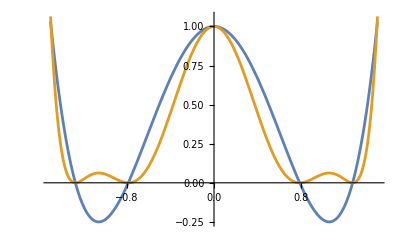

```mathematica
Plot[{f@x,f2@x},{x,-xyLim,xyLim}]
```

```mathematica
(* The cubic and heptic as f' *)
FullSimplify[f'@x/.φRep]
fpxRoots=octSym/@Union@N@Solve[f'@x==0]
N[%/.φRep]
```

4 x^3-2 √5 x

{{x→-1.05737},{x→0.},{x→1.05737}}

{{x→-1.05737},{x→0.},{x→1.05737}}

```mathematica
FullSimplify[f2'@x/.φRep]
Expand@%
```

-4 x (-2 x^6+3 √5 x^4-7 x^2+√5)

8 x^7-12 √5 x^5+28 x^3-4 √5 x

```mathematica
f2pxRoots=octSym/@Union@N@Solve[f2'@x==0]
N[%/.φRep]
```

{{x→-√φ},{x→-1.05737},{x→-√(1/φ)},{x→0.},{x→√(1/φ)},{x→1.05737},{x→√φ}}

{{x→-1.27202},{x→-1.05737},{x→-0.786151},{x→0.},{x→0.786151},{x→1.05737},{x→1.27202}}

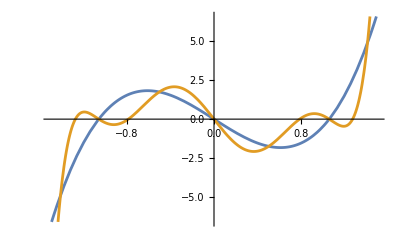

```mathematica
Plot[{f'@x,f2'@x},{x,-xyLim,xyLim}]
```

```mathematica
(* The quadratic and sextic as f'' *)
FullSimplify[f''@x/.φRep]
fppxRoots=octSym/@Union@N@Solve[f''@x==0]
N[%/.φRep]
```

-2 (√5-6 x^2)

{{x→-0.61047},{x→0.61047}}

{{x→-0.61047},{x→0.61047}}

```mathematica
FullSimplify[f2''@x/.φRep]
```

56 x^6-60 √5 x^4+84 x^2-4 √5

```mathematica
f2ppxRoots=octSym/@Union@N@Solve[f2''@x==0]
N[%/.φRep]
```

{{x→-1.1901},{x→-0.91988},{x→-0.36506},{x→0.36506},{x→0.91988},{x→1.1901}}

{{x→-1.1901},{x→-0.91988},{x→-0.36506},{x→0.36506},{x→0.91988},{x→1.1901}}

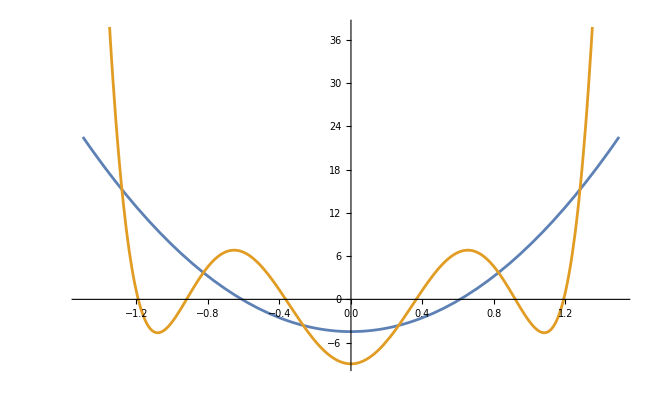

```mathematica
Plot[{f''@x,
f2''@x},
{x,-xyLim,xyLim},(*)PlotRange->{{-xyLim,xyLim},{-5 xyLim,5 xyLim}},**)
ImageSize->1imageSize]
```

```mathematica
(* The quadratic and sextic as f'' *)
Expand@FullSimplify[f'''@x/.φRep]
```

24 x

```mathematica
Expand@FullSimplify[f2'''@x/.φRep]
```

336 x^5-240 √5 x^3+168 x

```mathematica
fpppxRoots=octSym/@Union@N@Solve[f'''@x==0]
```

{{x→0.}}

```mathematica
f2pppxRoots=octSym/@Union@N@Solve[f2'''@x==0]
```

{{x→-1.08155},{x→-0.65379},{x→0.},{x→0.65379},{x→1.08155}}

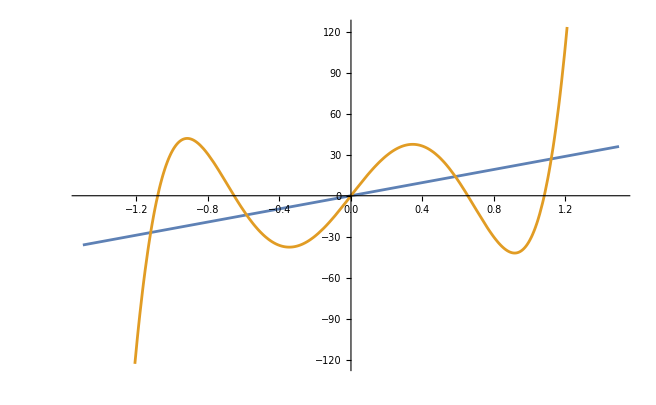

```mathematica
Plot[{f'''@x,
f2'''@x},
{x,-xyLim,xyLim},(*)PlotRange->{{-xyLim,xyLim},{-5 xyLim,5 xyLim}},**)
ImageSize->1imageSize]
```

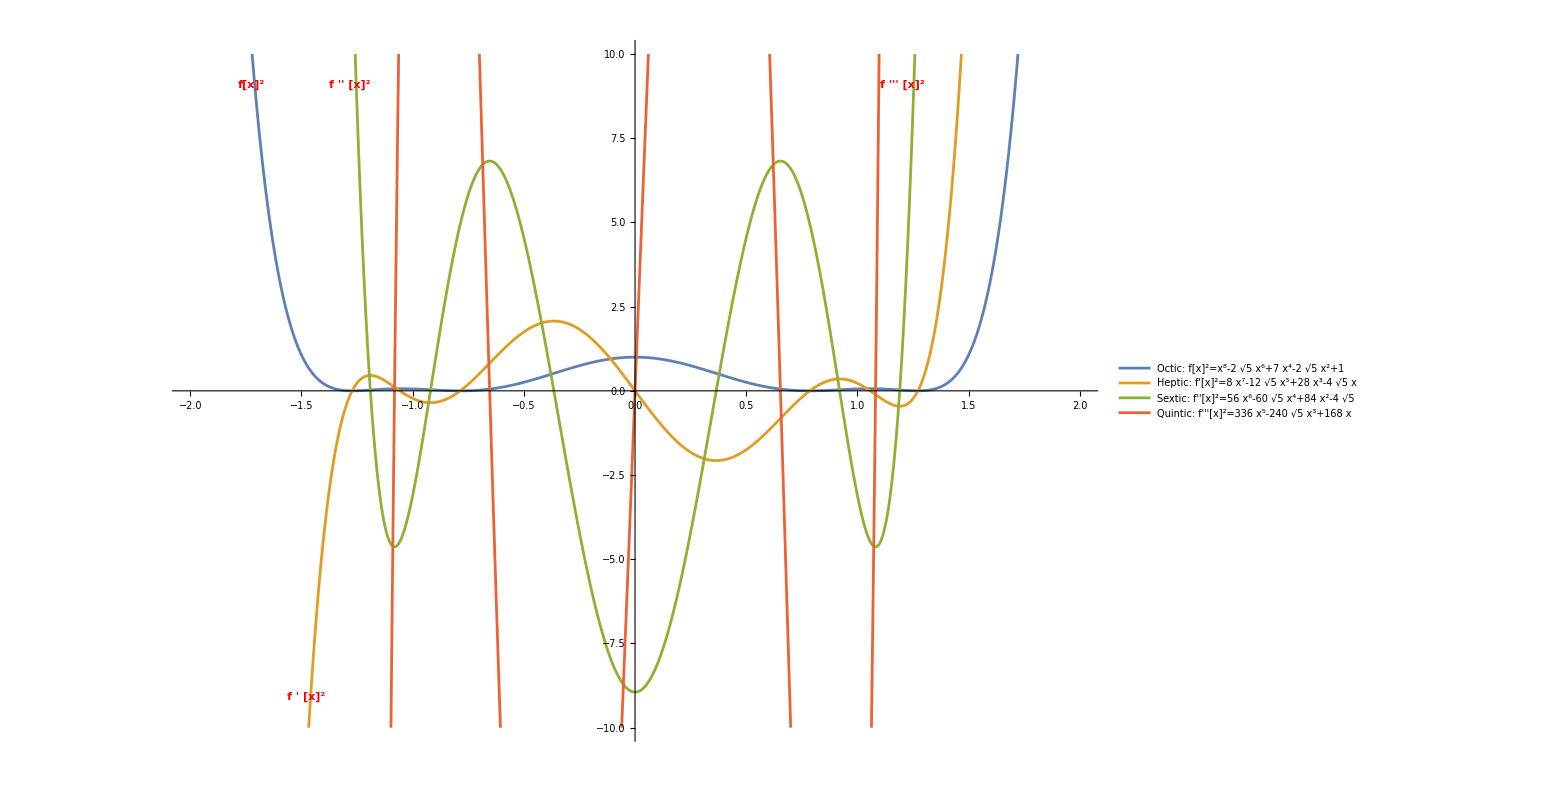

```mathematica
xyLim=2;
Plot[{
(**)
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify@f2@x/.φRep,
         (*)"Dropline",**)
(*){Placed[{"XSlice","Ball"},#]&/@({#,0}&/@f2xRoots⟦All,1,2⟧),**)
Placed[{"Ball"},#]&/@Select[Chop[{#,f2@#/.φRep}&/@f2pxRoots⟦All,1,2⟧],#⟦2⟧!=0&]],
   Style["f[x]^2",Bold,Red],Left],              "Octic:        f[x]^2="<>ToString[Expand@FullSimplify@f2@x/.φRep,TraditionalForm]]
(**),
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify[f2'@x/.φRep],
      (*)"Dropline",**)
Placed[{"Ball"},#]&/@Select[Chop[{#,f2'@#/.φRep}&/@f2ppxRoots⟦All,1,2⟧],#⟦2⟧!=0&]],
   Style["f ' [x]^2",Bold,Red],Bottom],  "Heptic:      f'[x]^2="<>ToString[Expand@FullSimplify[f2'@x/.φRep],TraditionalForm]]
(**),
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify[f2''@x/.φRep],
   (*)"Dropline",**)
Placed[{"Ball"},#]&/@Select[Chop[{#,f2''@#/.φRep}&/@f2pppxRoots⟦All,1,2⟧],#⟦2⟧!=0&]],
   Style["f '' [x]^2",Bold,Red],Top],       "Sextic:      f''[x]^2="<>ToString[Expand@FullSimplify[f2''@x/.φRep],TraditionalForm]]
(**),
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify[f2'''@x/.φRep],
(**)"Dropline"(*),
Placed[{"XSlice","Ball"},#]&/@({#,0}&/@f2pppxRoots⟦All,1,2⟧)**)],
     Style["f ''' [x]^2",Bold,Red],Right],"Quintic:     f'''[x]^2="<>ToString[Expand@FullSimplify[f2'''@x/.φRep],TraditionalForm]]
},
{x,-xyLim,xyLim},PlotRange->(xyLim{{-1,1},{-1,1}5}/.slRep),
PlotPoints->10^3,(*)ColorFunction->"BrightBands",**)
ImageSize->2imageSize]
```

```mathematica
xyLim=7/5;
RevolutionPlot3D[f2@x/.φRep,{x,0,xyLim}]
```

-Graphics3D-

```mathematica
xyLim=13/10;
RevolutionPlot3D[f2'@x/.φRep,{x,0,xyLim}]
```

-Graphics3D-

```mathematica
xyLim=6/5;
RevolutionPlot3D[f2''@x/.φRep,{x,0,xyLim}]
```

-Graphics3D-

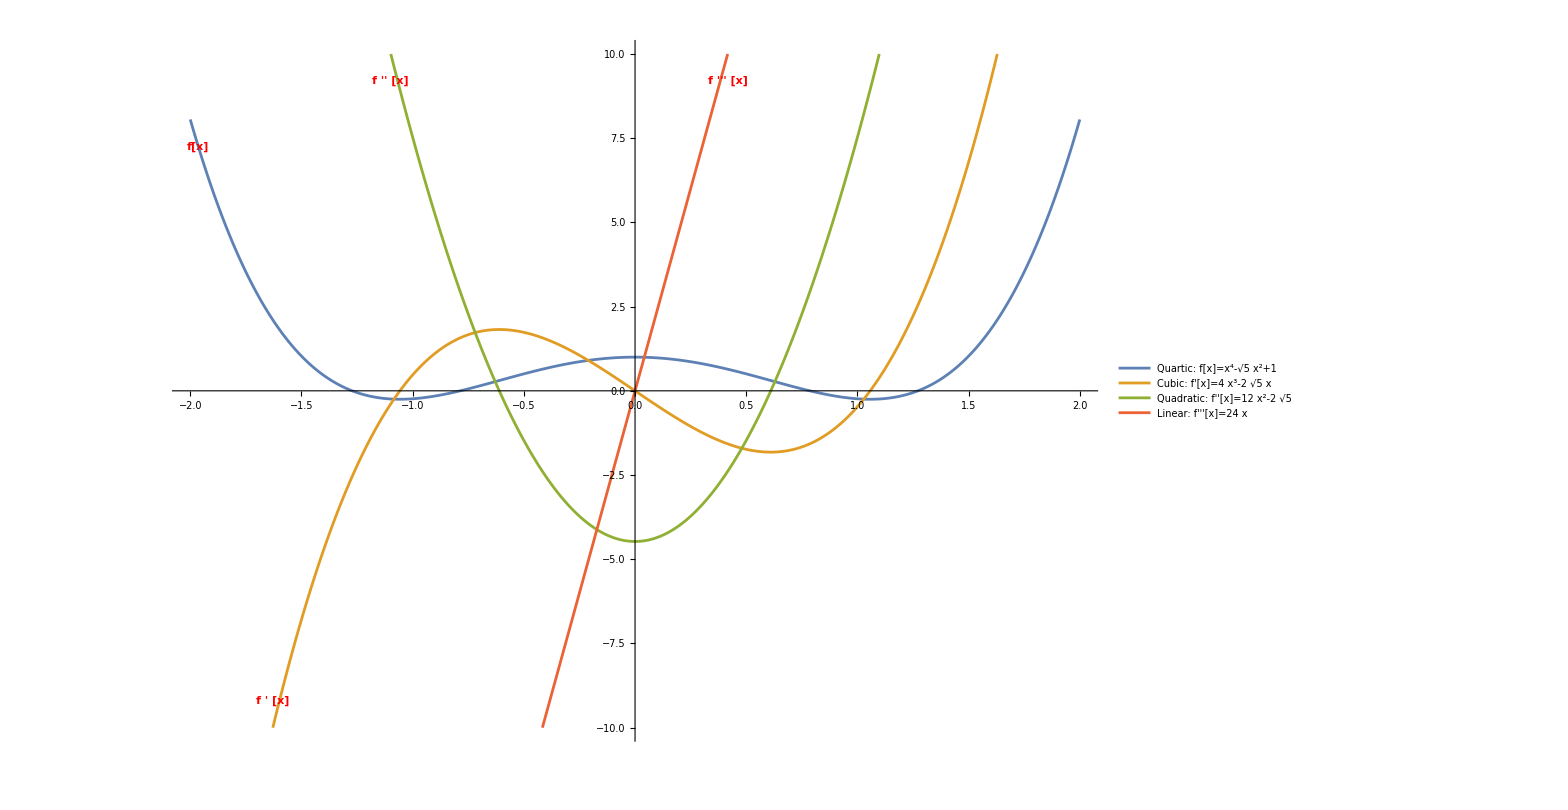

```mathematica
xyLim=2;
Plot[{
Legended[Labeled[(*)Tooltip@**)Highlighted[FullSimplify@f@x/.φRep,
                            (*)"Dropline",**)
Placed[{"Ball"},#]&/@Select[Chop[{#,f@#/.φRep}&/@fpxRoots⟦All,1,2⟧],#⟦2⟧!=0&]],
   Style["f[x]",Bold,Red],Left],                "Quartic:     f[x]="<>ToString[FullSimplify@f@x/.φRep,TraditionalForm]]
(**),
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify[f'@x/.φRep],
       (*)"Dropline",**)
Placed[{"Ball"},#]&/@Select[Chop[{#,f'@#/.φRep}&/@fppxRoots⟦All,1,2⟧],#⟦2⟧!=0&]],
    Style["f ' [x]",Bold,Red],Bottom],      "Cubic:       f'[x]="<>ToString[Expand@FullSimplify[f'@x/.φRep],TraditionalForm]]
(**),
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify[f''@x/.φRep],
     (*)"Dropline",**)
Placed[{"Ball"},#]&/@Select[Chop[{#,f''@#/.φRep}&/@fpppxRoots⟦All,1,2⟧],#⟦2⟧!=0&]],
  Style["f '' [x]",Bold,Red],Top],          "Quadratic: f''[x]="<>ToString[Expand@FullSimplify[f''@x/.φRep],TraditionalForm]]
(**),
Legended[Labeled[(*)Tooltip@**)Highlighted[Expand@FullSimplify[f'''@x/.φRep],
  (*)"Dropline",**)
(**)"Dropline"(*),
Placed[{"XSlice","Ball"},#]&/@({#,0}&/@fpppxRoots⟦All,1,2⟧)**)],
Style["f ''' [x]",Bold,Red],Right],    "Linear:       f'''[x]="<>ToString[Expand@FullSimplify[f'''@x/.φRep],TraditionalForm]]
(**)
},
{x,-xyLim,xyLim},PlotRange->(xyLim{{-1,1},{-1,1}5}/.slRep),
PlotPoints->10^3,(*)ColorFunction->"BrightBands",**)
ImageSize->2imageSize]
```

```mathematica
xyLim=7/5;
RevolutionPlot3D[f@x/.φRep,{x,0,xyLim}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[f'@x/.φRep,{x,0,xyLim}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[f''@x/.φRep,{x,0,xyLim}]
```

-Graphics3D-